### Numerical Results

#### ======================================================== 3 + 1 Case ======================================================================

```mathematica
ClearAll[U,an,dm21,dm32,s12,s13,s23,c12,c13,c23,θ12,θ13,θ23,deltaCPdeg,deltaCPrad,En,aMatter,δk];
wp =35;
δk[i_,j_]:=KroneckerDelta[i,j];
s12=0.308;           
s13=0.02215;          
s23=0.470;           
deltaCPdeg=212;     
dm21=Rationalize[7.49*10^-5,10^(-wp)];      
dm32=Rationalize[2.438*10^-3,10^(-wp)];      
dm31=dm32+dm21;
dm42 = 10; (*m4^2*)

θ12=ArcSin[Sqrt[s12]];
θ13=ArcSin[Sqrt[s13]];
θ23=ArcSin[Sqrt[s23]];
deltaCPrad=deltaCPdeg Degree;

c12=Cos[θ12];s12r=Sin[θ12];
c13=Cos[θ13];s13r=Sin[θ13];
c23=Cos[θ23];s23r=Sin[θ23];

GF = Rationalize[1.16 * 10^(-8),10^(-wp)]; (* not true eV^-2*) 
energy = 10^6; (*1 MeV*)
U[α_,pt_]:=Rationalize[Umat[[α,pt]],10^(-wp)];

Umat={{c12 c13,s12r c13,s13r Exp[-I deltaCPrad],0},{-s12r c23-c12 s23r s13r Exp[I deltaCPrad],c12 c23-s12r s23r s13r Exp[I deltaCPrad],s23r c13,0},{s12r s23r-c12 c23 s13r Exp[I deltaCPrad],-c12 s23r-s12r c23 s13r Exp[I deltaCPrad],c23 c13,0},{0,0,0,1}};

(*----------Matter term:you can choose any numeric value for (2 E A) in eV^2----------*)
(*Here I just pick a small,nonzero example.Replace with your model's value.*)
aMatter[x_]:=Rationalize[1*x*GF,10^(-wp)];   (*this stands for (A) in your formula,in eV^2*)
aMatter2[y_]:=Rationalize[1*y*GF,10^(-wp)]*y;
(*----------Your a_ij (I’m naming it an[i,j])----------*)
an[i_,j_,x_,y_,En_]:=N[Refine[(1/4) (dm21-dm32-dm42) δk[i,j]-dm21 U[i,1] Conjugate[U[j,1]]+dm32 U[i,3] Conjugate[U[j,3]]+dm42 U[i,4] Conjugate[U[j,4]]+(1/4) En*aMatter[x] (2 δk[i,1] δk[j,1]-δk[i,2] δk[j,2]-δk[i,3] δk[j,3]-δk[i,4] δk[j,4])+(1/4) En*aMatter[y] (3δk[i,1] δk[j,1]+3δk[i,2] δk[j,2]+3δk[i,3] δk[j,3]-δk[i,4] δk[j,4]),Element[{x,y},Reals]],wp];

(*----------Build Hermitian matrix A from an[i,j]----------*)
n=4;Atilde[x_,y_,En_]:=N[Refine[Table[Which[i==j,an[i,j,x,y,En],i<j,an[i,j,x,y,En],i>j,Conjugate[an[j,i,x,y,En]]],{i,n},{j,n}],Element[{x,y},Reals]],wp];
```

```mathematica
(*---your 3-flavor angles/phases---*)θ12=ArcSin[Sqrt[s12]];
θ13=ArcSin[Sqrt[s13]];
θ23=ArcSin[Sqrt[s23]];
δ13=deltaCPdeg Degree;

c12=Cos[θ12];s12r=Sin[θ12];
c13=Cos[θ13];s13r=Sin[θ13];
c23=Cos[θ23];s23r=Sin[θ23];

U3={{c12 c13,s12r c13,s13r Exp[-I δ13]},{-s12r c23-c12 s23r s13r Exp[I δ13],c12 c23-s12r s23r s13r Exp[I δ13],s23r c13},{s12r s23r-c12 c23 s13r Exp[I δ13],-c12 s23r-s12r c23 s13r Exp[I δ13],c23 c13}};

(*U3 is 3x3*)U0=IdentityMatrix[4];
U0[[1;;3,1;;3]]=U3;   (*embed U3 into upper-left*)
(*now U0 is U_PMNS⊕1*)

(*---sterile angles/phases (set these)---*)
θ14=3 Degree;δ14=Pi/2;
θ24=2 Degree;δ24=Pi/3;
θ34=2 Degree;   (*usually taken real in this convention*)

(*---complex rotation matrices in ij plane---*)
R14[th_,del_]:=Module[{R=IdentityMatrix[4],c=Cos[th],s=Sin[th]},R[[1,1]]=c;R[[4,4]]=c;
R[[1,4]]=s Exp[-I del];
R[[4,1]]=-s Exp[I del];
R];

R24[th_,del_]:=Module[{R=IdentityMatrix[4],c=Cos[th],s=Sin[th]},R[[2,2]]=c;R[[4,4]]=c;
R[[2,4]]=s Exp[-I del];
R[[4,2]]=-s Exp[I del];
R];

R34[th_]:=Module[{R=IdentityMatrix[4],c=Cos[th],s=Sin[th]},R[[3,3]]=c;R[[4,4]]=c;
R[[3,4]]=s;
R[[4,3]]=-s;
R];

Umat4=R34[θ34].R24[θ24,δ24].R14[θ14,δ14].U0;
```

```mathematica
Umat4
```

(0.821474+0. ⅈ | 0.548045+0. ⅈ | -0.126041+0.0787591 ⅈ | 0.-0.052336 ⅈ
-0.333149+0.0441992 ⅈ | 0.652362+0.0294874 ⅈ | 0.677789-9.48692×10^-6 ⅈ | 0.0174258-0.0301824 ⅈ
0.456881+0.0465548 ⅈ | -0.519354+0.0301358 ⅈ | 0.719196-0.00048469 ⅈ | 0.0348304+0. ⅈ
-0.00879667-0.0354207 ⅈ | 0.00763112-0.0500653 ⅈ | -0.0328242-0.0138797 ⅈ | 0.997413+0. ⅈ)

```mathematica
(*unitarity*)Max[Abs[Flatten[ConjugateTranspose[Umat4].Umat4-IdentityMatrix[4]]]]

(*sterile magnitudes*)
Abs/@Umat4[[;;,4]]

(*CP-odd invariants*)
J[i_,j_,α_,β_]:=Im[Umat4[[α,i]] Conjugate[Umat4[[α,j]]] Conjugate[Umat4[[β,i]]] Umat4[[β,j]]];
N[J[1,4,1,2],20]
Total[Abs[Umat4[[;;,4]]]^2]//N
```

1.11022×10^-16

{0.052336,0.0348517,0.0348304,0.997413}

-0.000306943

1.

```mathematica
(*===========================================================================   Jarlskogg    ================================================================*)
Umat4[[1,4]] Conjugate[Umat4[[3,4]]] Conjugate[Umat4[[4,4]]] Umat4[[1,4]] Conjugate[Umat4[[4,4]]] Umat4[[3,4]]
Im[Umat4[[2,4]] Conjugate[Umat4[[3,4]]] Conjugate[Umat4[[4,4]]] Umat4[[2,4]] Conjugate[Umat4[[4,4]]] Umat4[[3,4]]]
Umat4[[1,4]] Conjugate[Umat4[[4,4]]] Conjugate[Umat4[[2,4]]] Umat4[[1,4]] Conjugate[Umat4[[4,4]]] Umat4[[2,4]]
Im[Umat4[[2,4]] Conjugate[Umat4[[3,4]]] Conjugate[Umat4[[4,4]]] Umat4[[2,4]] Conjugate[Umat4[[4,4]]] Umat4[[3,4]]]
Umat4[[4,4]] Conjugate[Umat4[[1,4]]] Conjugate[Umat4[[2,3]]] Umat4[[1,3]] Conjugate[Umat4[[2,4]]] Umat4[[1,4]]//Im
```

-3.30574×10^-6+0. ⅈ

-1.26954×10^-6

-3.30977×10^-6+0. ⅈ

-1.26954×10^-6

-4.50304×10^-6

```mathematica
Clear[dm21,dm32,dm42]
```

```mathematica
an4[i_,j_,x_,y_,En_]:=N[Refine[(1/4) (dm21-dm32-dm42) δk[i,j]-dm21 Umat4[[i,1]] Conjugate[Umat4[[j,1]]]+dm32 Umat4[[i,3]] Conjugate[Umat4[[j,3]]]+dm42 Umat4[[i,4]] Conjugate[Umat4[[j,4]]]+(1/4) En*aMatter[x] (2 δk[i,1] δk[j,1]-δk[i,2] δk[j,2]-δk[i,3] δk[j,3]-δk[i,4] δk[j,4])+ aMatter2[y],Element[{x,y},Reals]],wp];
```

```mathematica
an4[1,2,0,0,0]
```

0.0156085-0.00898711 ⅈ

```mathematica
tex=Im[Conjugate[an4[1,3,0,0,4]] * an4[1,4,0,0,4]* Conjugate[an4[3,4,0,0,4]]]
```

Im(((0.00722623-0.0290972 ⅈ) dm21+(0.00304404-0.00433462 ⅈ) dm32-(0.+0.0522006 ⅈ) dm42) (-(0.0906863+0.0565821 ⅈ) Conjugate[dm32]+(0.+0.00182288 ⅈ) Conjugate[dm42]+(-0.375315-0.0382435 ⅈ) Conjugate[dm21]) ((0.00566803+0.0157735 ⅈ) Conjugate[dm21]-(0.0236003+0.00999813 ⅈ) Conjugate[dm32]+(0.0347403+0. ⅈ) Conjugate[dm42]))

```mathematica
dm21=Re[dm211]+I*0;  (*Force real*)
dm32=Re[dm321]+I*0;
dm42=Re[dm421]+I*0;
```

```mathematica
simplified=ComplexExpand[tex,{dm21,dm32,dm42},TargetFunctions->{Re,Im}]//Expand;

(*Collect terms by monomials*)
finalResult=Collect[simplified,{dm21^3,dm21^2*dm32,dm21^2*dm42,dm21*dm32^2,dm21*dm32*dm42,dm21*dm42^2,dm32^3,dm32^2*dm42,dm32*dm42^2,dm42^3}];

(*Display the result*)
Print["Im(p*q*r) = "];
finalResult
```

Im(p*q*r) =

6.77626×10^-21 dm211^3-0.000248708 dm211^2 dm321+0.000450254 dm211^2 dm421-0.00005915 dm211 dm321^2-0.000332914 dm211 dm321 dm421+0.00068258 dm211 dm421^2-8.47033×10^-22 dm321^3-0.0000747277 dm321^2 dm421+0.000163698 dm321 dm421^2+0.

```mathematica
Im[Refine[Conjugate[an4[1,3,0,0,0]]an4[1,4,0,0,0]Conjugate[an4[3,4,0,0,0]],Element[{dm21,dm32,dm42},Reals]]]//ComplexExpand
Im[Refine[Conjugate[an4[1,4,0,0,0]]an4[1,2,0,0,0]an4[2,4,0,0,0],Element[{dm21,dm32,dm42},Reals]]]//ComplexExpand
```

6.77626×10^-21 dm211^3-0.000248708 dm211^2 dm321+0.000450254 dm211^2 dm421-0.00005915 dm211 dm321^2-0.000332914 dm211 dm321 dm421+0.00068258 dm211 dm421^2-8.47033×10^-22 dm321^3-0.0000747277 dm321^2 dm421+0.000163698 dm321 dm421^2+0.

3.38813×10^-21 dm211^3-0.000191457 dm211^2 dm321+0.0000730402 dm211^2 dm421-1.89996×10^-6 dm211 dm321^2-0.000332914 dm211 dm321 dm421+0.000305367 dm211 dm421^2+8.47033×10^-22 dm321^3+0.000084173 dm321^2 dm421+4.79721×10^-6 dm321 dm421^2+0.

```mathematica
Im[Refine[Conjugate[an4[2,3,0,0,0]]an4[2,4,0,0,0]Conjugate[an4[3,4,0,0,0]],Element[{dm21,dm32,dm42},Reals]]]//ComplexExpand
Im[Refine[Conjugate[an4[1,2,0,0,0]]an4[1,4,0,0,0]Conjugate[an4[2,4,0,0,0]],Element[{dm21,dm32,dm42},Reals]]]//ComplexExpand
```

1.69407×10^-21 dm21^3-0.0000668823 dm21^2 dm32+0.0000977235 dm21^2 dm42-0.00025644 dm21 dm32^2+0.000332914 dm21 dm32 dm42-0.000134603 dm21 dm42^2+1.35525×10^-20 dm32^3+0.000422066 dm32^2 dm42-0.000511036 dm32 dm42^2+0.

-3.38813×10^-21 dm21^3+0.000191457 dm21^2 dm32-0.0000730402 dm21^2 dm42+1.89996×10^-6 dm21 dm32^2+0.000332914 dm21 dm32 dm42-0.000305367 dm21 dm42^2-8.47033×10^-22 dm32^3-0.000084173 dm32^2 dm42-4.79721×10^-6 dm32 dm42^2+0.

```mathematica
Atilde[0,0,g]
```

(-0.25058745604778000002130343114416324 | -0.00018814712601767217527973499915154594+0.0001331224975860546832124094849246859 ⅈ | -0.00024967257633835283641269476716798149+0.0001413645330243541150678314870021366 ⅈ | 0
-0.00018814712601767217527973499915154594-0.0001331224975860546832124094849246859 ⅈ | -0.24947870559251556808556103972012708 | 0.0012010543038707797429524533493015702-2.7271359990246516961897096452095×10^-6 ⅈ | 0
-0.00024967257633835283641269476716798149-0.0001413645330243541150678314870021366 ⅈ | 0.0012010543038707797429524533493015702+2.7271359990246516961897096452095×10^-6 ⅈ | -0.24934306335970443239885257214961832 | 0
0 | 0 | 0 | 0.749409225)

```mathematica
Eigenvectors[Atilde[0,0,En]]
Eigenvalues[Atilde[0,0,En]]
```

(0 | 0 | 0 | 1.
0.82260087527305730433340710575149029 | -0.33205011909985804495368250679876247+0.044977835241570907886572598588535479 ⅈ | 0.4569094560606586099040274495847312+0.047762555470842310412463398863551378 ⅈ | 0
0.54821928489782225384258234276868196-0.025167750517684748654943744290614521 ⅈ | 0.65431659977624913285794018043231819 | -0.51729630377131673728583518779935239+0.055646395766315236566441547825783757 ⅈ | 0
-0.12621394713219705158252137647441742+0.078867227346414071732704931018992147 ⅈ | 0.67793030615248349646567107629849846+1.7804732852176495865016110807667769×10^-19 ⅈ | 0.71990311848192462265631815532019826 | 0)

{0.749409225,-0.25066567500000000000253893413120629+2.5436070965945442127789825761126196×10^-56 ⅈ,-0.250590775-2.6182743932601542322184971345128625×10^-56 ⅈ,-0.24815277500000000050317810888270235+9.0598215776934542209803362377919947×10^-58 ⅈ}

```mathematica
lami=Eigenvalues[SetPrecision[Atilde[x,y,En],35]];
```

```mathematica
λ1[x_,y_,En_]:=Evaluate[lami[[1]]];
λ2[x_,y_,En_]:=Evaluate[lami[[2]]];
λ3[x_,y_,En_]:=Evaluate[lami[[3]]];
λ4[x_,y_,En_]:=Evaluate[lami[[4]]];
```

```mathematica
Plot3D[{λ1[x,y,energy],λ2[x,y,energy],λ3[x,y,energy],λ4[x,y,energy]},{x,0,1},{y,0,1}]
```

-Graphics3D-

```mathematica
J=Im[U[1,1] U[2,2] Conjugate[U[1,2]] Conjugate[U[2,1]]];
N[J]
Im[U[2,1] Conjugate[U[2,3]] Conjugate[U[3,1]] U[3,3]]
```

-0.0177699

778908548867598499482141724874748961989817315239/43833120365498628904568493934433602953778944954182

```mathematica
energy=4;
```

```mathematica
Clear[ut11,ut12,ut13,ut14,ut21,ut22,ut23,ut24,ut31,ut32,ut33,ut34,ut41,ut42,ut43,ut44]
```

```mathematica
ut11[x_,y_,En_]:=(-Conjugate[an[1,2,x,y,En]]Conjugate[an[2,3,x,y,En]]Conjugate[an[3,4,x,y,En]]) +Conjugate[an[1,2,x,y,En]]Conjugate[an[2,4,x,y,En]](an[3,3,x,y,En]-λ1[x,y,En])+Conjugate[an[1,3,x,y,En]]Conjugate[an[3,4,x,y,En]](an[2,2,x,y,En]-λ1[x,y,En])-Conjugate[an[1,3,x,y,En]]an[2,3,x,y,En]Conjugate[an[2,4,x,y,En]]-(Conjugate[an[1,4,x,y,En]](an[2,2,x,y,En]-λ1[x,y,En])(an[3,3,x,y,En]-λ1[x,y,En]))+(Conjugate[an[1,4,x,y,En]]an[2,3,x,y,En]Conjugate[an[2,3,x,y,En]]);

ut21[x_,y_,En_]:= -(Conjugate[an[1,1,x,y,En]]-λ1[x,y,En])Conjugate[an[2,3,x,y,En]]Conjugate[an[3,4,x,y,En]] + (an[1,1,x,y,En]- λ1[x,y,En] )Conjugate[an[2,4,x,y,En]](an[3,3,x,y,En]- λ1[x,y,En] )+an[1,2,x,y,En]Conjugate[an[1,3,x,y,En]]Conjugate[an[3,4,x,y,En]]-an[1,2,x,y,En]Conjugate[an[1,4,x,y,En]](an[3,3,x,y,En]- λ1[x,y,En] )+an[1,3,x,y,En]Conjugate[an[1,4,x,y,En]]Conjugate[an[2,3,x,y,En]]-an[1,3,x,y,En]Conjugate[an[1,3,x,y,En]]Conjugate[an[2,4,x,y,En]]

ut31[x_,y_,En_]:= -(an[1,1,x,y,En]- λ1[x,y,En] )Conjugate[an[3,4,x,y,En]](an[2,2,x,y,En]- λ1[x,y,En] ) + an[2,3,x,y,En]Conjugate[an[2,4,x,y,En]](an[1,1,x,y,En]- λ1[x,y,En] ) - an[1,3,x,y,En]Conjugate[an[1,2,x,y,En]]Conjugate[an[2,4,x,y,En]]- an[1,2,x,y,En]an[2,3,x,y,En]Conjugate[an[1,4,x,y,En]]+an[1,2,x,y,En]Conjugate[an[1,2,x,y,En]]Conjugate[an[3,4,x,y,En]]+(Conjugate[an[2,2,x,y,En]]-λ1[x,y,En])Conjugate[an[1,4,x,y,En]]an[1,3,x,y,En]

ut41[x_,y_,En_]:= -(an[1,1,x,y,En]- λ1[x,y,En] )(an[2,2,x,y,En]- λ1[x,y,En] )(an[3,3,x,y,En]- λ1[x,y,En] ) - (an[1,1,x,y,En]- λ1[x,y,En] )Conjugate[an[2,3,x,y,En]]an[2,3,x,y,En] + an[1,2,x,y,En]an[2,3,x,y,En]Conjugate[an[1,3,x,y,En]]+an[1,3,x,y,En]Conjugate[an[1,2,x,y,En]]Conjugate[an[2,3,x,y,En]] - Conjugate[an[1,2,x,y,En]]an[1,2,x,y,En](an[3,3,x,y,En]- λ1[x,y,En] )- Conjugate[an[1,3,x,y,En]]an[1,3,x,y,En](an[2,2,x,y,En]- λ1[x,y,En] )
```

```mathematica
ut12[x_,y_,En_]:=(-Conjugate[an[1,2,x,y,En]]Conjugate[an[2,3,x,y,En]]Conjugate[an[3,4,x,y,En]]) +Conjugate[an[1,2,x,y,En]]Conjugate[an[2,4,x,y,En]](an[3,3,x,y,En]-λ2[x,y,En])+Conjugate[an[1,3,x,y,En]]Conjugate[an[3,4,x,y,En]](an[2,2,x,y,En]-λ2[x,y,En])-Conjugate[an[1,3,x,y,En]]an[2,3,x,y,En]Conjugate[an[2,4,x,y,En]]-(Conjugate[an[1,4,x,y,En]](an[2,2,x,y,En]-λ2[x,y,En])(an[3,3,x,y,En]-λ2[x,y,En]))+(Conjugate[an[1,4,x,y,En]]an[2,3,x,y,En]Conjugate[an[2,3,x,y,En]]);

ut22[x_,y_,En_]:= -(Conjugate[an[1,1,x,y,En]]-λ2[x,y,En])Conjugate[an[2,3,x,y,En]]Conjugate[an[3,4,x,y,En]] + (an[1,1,x,y,En]- λ2[x,y,En] )Conjugate[an[2,4,x,y,En]](an[3,3,x,y,En]- λ2[x,y,En] )+an[1,2,x,y,En]Conjugate[an[1,3,x,y,En]]Conjugate[an[3,4,x,y,En]]-an[1,2,x,y,En]Conjugate[an[1,4,x,y,En]](an[3,3,x,y,En]- λ2[x,y,En] )+an[1,3,x,y,En]Conjugate[an[1,4,x,y,En]]Conjugate[an[2,3,x,y,En]]-an[1,3,x,y,En]Conjugate[an[1,3,x,y,En]]Conjugate[an[2,4,x,y,En]]

ut32[x_,y_,En_]:= -(an[1,1,x,y,En]- λ2[x,y,En] )Conjugate[an[3,4,x,y,En]](an[2,2,x,y,En]- λ2[x,y,En] ) + an[2,3,x,y,En]Conjugate[an[2,4,x,y,En]](an[1,1,x,y,En]- λ2[x,y,En] ) - an[1,3,x,y,En]Conjugate[an[1,2,x,y,En]]Conjugate[an[2,4,x,y,En]]- an[1,2,x,y,En]an[2,3,x,y,En]Conjugate[an[1,4,x,y,En]]+an[1,2,x,y,En]Conjugate[an[1,2,x,y,En]]Conjugate[an[3,4,x,y,En]]+(Conjugate[an[2,2,x,y,En]]-λ2[x,y,En])Conjugate[an[1,4,x,y,En]]an[1,3,x,y,En]

ut42[x_,y_,En_]:= -(an[1,1,x,y,En]- λ2[x,y,En] )(an[2,2,x,y,En]- λ2[x,y,En] )(an[3,3,x,y,En]- λ2[x,y,En] ) - (an[1,1,x,y,En]- λ2[x,y,En] )Conjugate[an[2,3,x,y,En]]an[2,3,x,y,En] + an[1,2,x,y,En]an[2,3,x,y,En]Conjugate[an[1,3,x,y,En]]+an[1,3,x,y,En]Conjugate[an[1,2,x,y,En]]Conjugate[an[2,3,x,y,En]] - Conjugate[an[1,2,x,y,En]]an[1,2,x,y,En](an[3,3,x,y,En]- λ2[x,y,En] )- Conjugate[an[1,3,x,y,En]]an[1,3,x,y,En](an[2,2,x,y,En]- λ2[x,y,En] )
```

```mathematica
ut13[x_,y_,En_]:=(-Conjugate[an[1,2,x,y,En]]Conjugate[an[2,3,x,y,En]]Conjugate[an[3,4,x,y,En]]) +Conjugate[an[1,2,x,y,En]]Conjugate[an[2,4,x,y,En]](an[3,3,x,y,En]-λ3[x,y,En])+Conjugate[an[1,3,x,y,En]]Conjugate[an[3,4,x,y,En]](an[2,2,x,y,En]-λ3[x,y,En])-Conjugate[an[1,3,x,y,En]]an[2,3,x,y,En]Conjugate[an[2,4,x,y,En]]-(Conjugate[an[1,4,x,y,En]](an[2,2,x,y,En]-λ3[x,y,En])(an[3,3,x,y,En]-λ3[x,y,En]))+(Conjugate[an[1,4,x,y,En]]an[2,3,x,y,En]Conjugate[an[2,3,x,y,En]]);

ut23[x_,y_,En_]:= -(Conjugate[an[1,1,x,y,En]]-λ3[x,y,En])Conjugate[an[2,3,x,y,En]]Conjugate[an[3,4,x,y,En]] + (an[1,1,x,y,En]- λ3[x,y,En] )Conjugate[an[2,4,x,y,En]](an[3,3,x,y,En]- λ3[x,y,En] )+an[1,2,x,y,En]Conjugate[an[1,3,x,y,En]]Conjugate[an[3,4,x,y,En]]-an[1,2,x,y,En]Conjugate[an[1,4,x,y,En]](an[3,3,x,y,En]- λ3[x,y,En] )+an[1,3,x,y,En]Conjugate[an[1,4,x,y,En]]Conjugate[an[2,3,x,y,En]]-an[1,3,x,y,En]Conjugate[an[1,3,x,y,En]]Conjugate[an[2,4,x,y,En]]

ut33[x_,y_,En_]:= -(an[1,1,x,y,En]- λ3[x,y,En] )Conjugate[an[3,4,x,y,En]](an[2,2,x,y,En]- λ3[x,y,En] ) + an[2,3,x,y,En]Conjugate[an[2,4,x,y,En]](an[1,1,x,y,En]- λ3[x,y,En] ) - an[1,3,x,y,En]Conjugate[an[1,2,x,y,En]]Conjugate[an[2,4,x,y,En]]- an[1,2,x,y,En]an[2,3,x,y,En]Conjugate[an[1,4,x,y,En]]+an[1,2,x,y,En]Conjugate[an[1,2,x,y,En]]Conjugate[an[3,4,x,y,En]]+(Conjugate[an[2,2,x,y,En]]-λ3[x,y,En])Conjugate[an[1,4,x,y,En]]an[1,3,x,y,En]

ut43[x_,y_,En_]:= -(an[1,1,x,y,En]- λ3[x,y,En] )(an[2,2,x,y,En]- λ3[x,y,En] )(an[3,3,x,y,En]- λ3[x,y,En] ) - (an[1,1,x,y,En]- λ3[x,y,En] )Conjugate[an[2,3,x,y,En]]an[2,3,x,y,En] + an[1,2,x,y,En]an[2,3,x,y,En]Conjugate[an[1,3,x,y,En]]+an[1,3,x,y,En]Conjugate[an[1,2,x,y,En]]Conjugate[an[2,3,x,y,En]] - Conjugate[an[1,2,x,y,En]]an[1,2,x,y,En](an[3,3,x,y,En]- λ3[x,y,En] )- Conjugate[an[1,3,x,y,En]]an[1,3,x,y,En](an[2,2,x,y,En]- λ3[x,y,En] )
```

```mathematica
ut14[x_,y_,En_]:=(-Conjugate[an[1,2,x,y,En]]Conjugate[an[2,3,x,y,En]]Conjugate[an[3,4,x,y,En]]) +Conjugate[an[1,2,x,y,En]]Conjugate[an[2,4,x,y,En]](an[3,3,x,y,En]-λ4[x,y,En])+Conjugate[an[1,3,x,y,En]]Conjugate[an[3,4,x,y,En]](an[2,2,x,y,En]-λ4[x,y,En])-Conjugate[an[1,3,x,y,En]]an[2,3,x,y,En]Conjugate[an[2,4,x,y,En]]-(Conjugate[an[1,4,x,y,En]](an[2,2,x,y,En]-λ4[x,y,En])(an[3,3,x,y,En]-λ4[x,y,En]))+(Conjugate[an[1,4,x,y,En]]an[2,3,x,y,En]Conjugate[an[2,3,x,y,En]]);

ut24[x_,y_,En_]:= -(Conjugate[an[1,1,x,y,En]]-λ4[x,y,En])Conjugate[an[2,3,x,y,En]]Conjugate[an[3,4,x,y,En]] + (an[1,1,x,y,En]- λ4[x,y,En] )Conjugate[an[2,4,x,y,En]](an[3,3,x,y,En]- λ4[x,y,En] )+an[1,2,x,y,En]Conjugate[an[1,3,x,y,En]]Conjugate[an[3,4,x,y,En]]-an[1,2,x,y,En]Conjugate[an[1,4,x,y,En]](an[3,3,x,y,En]- λ4[x,y,En] )+an[1,3,x,y,En]Conjugate[an[1,4,x,y,En]]Conjugate[an[2,3,x,y,En]]-an[1,3,x,y,En]Conjugate[an[1,3,x,y,En]]Conjugate[an[2,4,x,y,En]]

ut34[x_,y_,En_]:= -(an[1,1,x,y,En]- λ4[x,y,En] )Conjugate[an[3,4,x,y,En]](an[2,2,x,y,En]- λ4[x,y,En] ) + an[2,3,x,y,En]Conjugate[an[2,4,x,y,En]](an[1,1,x,y,En]- λ4[x,y,En] ) - an[1,3,x,y,En]Conjugate[an[1,2,x,y,En]]Conjugate[an[2,4,x,y,En]]- an[1,2,x,y,En]an[2,3,x,y,En]Conjugate[an[1,4,x,y,En]]+an[1,2,x,y,En]Conjugate[an[1,2,x,y,En]]Conjugate[an[3,4,x,y,En]]+(Conjugate[an[2,2,x,y,En]]-λ4[x,y,En])Conjugate[an[1,4,x,y,En]]an[1,3,x,y,En]

ut44[x_,y_,En_]:= -(an[1,1,x,y,En]- λ4[x,y,En] )(an[2,2,x,y,En]- λ4[x,y,En] )(an[3,3,x,y,En]- λ4[x,y,En] ) - (an[1,1,x,y,En]- λ4[x,y,En] )Conjugate[an[2,3,x,y,En]]an[2,3,x,y,En] + an[1,2,x,y,En]an[2,3,x,y,En]Conjugate[an[1,3,x,y,En]]+an[1,3,x,y,En]Conjugate[an[1,2,x,y,En]]Conjugate[an[2,3,x,y,En]] - Conjugate[an[1,2,x,y,En]]an[1,2,x,y,En](an[3,3,x,y,En]- λ4[x,y,En] )- Conjugate[an[1,3,x,y,En]]an[1,3,x,y,En](an[2,2,x,y,En]- λ4[x,y,En] )
```

```mathematica
Ut1[x_,y_,En_]:=Refine[(1/Ni)*{ut11[x,y,En], ut21[x,y,En],ut31[x,y,En],ut41[x,y,En] },Element[{x,y},Reals]];
Ut2[x_,y_,En_]:=Refine[(1/Ni)*{ut12[x,y,En], ut22[x,y,En],ut32[x,y,En],ut42[x,y,En] },Element[{x,y},Reals]];
Ut3[x_,y_,En_]:=Refine[(1/Ni)*{ut13[x,y,En], ut23[x,y,En],ut33[x,y,En],ut43[x,y,En] },Element[{x,y},Reals]];
Ut4[x_,y_,En_]:=Refine[(1/Ni)*{ut14[x,y,En], ut24[x,y,En],ut34[x,y,En],ut44[x,y,En] },Element[{x,y},Reals]];
```

```mathematica
Ut2[2,1,1]
Ut1[2,1,1]
Ut3[2,1,1]
Ut4[2,1,1]
```

{0,0,0,-(2.4560484094605124422×10^-10+0. ⅈ)/Ni}

{0,0,0,(999.7637145144904567638189677959479+0. ⅈ)/Ni}

{0,0,0,-(9.244029799723170258×10^-12+0. ⅈ)/Ni}

{0,0,0,(7.6849718325803251166352×10^-9+0. ⅈ)/Ni}

```mathematica
norm1[x_,y_,En_]:=Refine[Conjugate[Ni*Ut1[x,y,En]].(Ni*Ut1[x,y,En]),Element[{x,y},Reals]]
norm2[x_,y_,En_]:=Refine[Conjugate[Ni*Ut2[x,y,En]].(Ni*Ut2[x,y,En]),Element[{x,y},Reals]]
norm3[x_,y_,En_]:=Refine[Conjugate[Ni*Ut3[x,y,En]].(Ni*Ut3[x,y,En]),Element[{x,y},Reals]]
norm4[x_,y_,En_]:=Refine[Conjugate[Ni*Ut4[x,y,En]].(Ni*Ut4[x,y,En]),Element[{x,y},Reals]]
```

```mathematica
norm1[0,0,4]-norm1[1,1,4]
norm1[0,0,4]-norm1[0,1,4]
norm1[0,0,4]-norm1[1,0,4]
norm1[0,0,4]
```

0.034785750526322191595024805+0. ⅈ

0.027829037033106160101682658+0. ⅈ

0.006956713654627031750994469+0. ⅈ

999527.49529542770498098033416334+0. ⅈ

```mathematica
1/norm1[1,0,4] + 1/norm1[1,1,4]-1/norm1[0,1,4]-1/norm1[0,0,4]
```

1.392658527692571136092191×10^-14+0. ⅈ

```mathematica
norm1N=Refine[Conjugate[Ni*Ut1[x,y,En]].(Ni*Ut1[x,y,En]),Element[{x,y},Reals]]/.En->energy //ComplexExpand;
norm2N=Refine[Conjugate[Ni*Ut2[x,y,En]].(Ni*Ut2[x,y,En]),Element[{x,y},Reals]]/.En->energy //ComplexExpand;
norm3N=Refine[Conjugate[Ni*Ut3[x,y,En]].(Ni*Ut3[x,y,En]),Element[{x,y},Reals]]/.En->energy //ComplexExpand;
norm4N=Refine[Conjugate[Ni*Ut4[x,y,En]].(Ni*Ut4[x,y,En]),Element[{x,y},Reals]]/.En->energy //ComplexExpand;
(*Line Integral*)
prefactor1N=1/norm1N;
prefactor2N=1/norm2N;
prefactor3N=1/norm3N;
prefactor4N=1/norm4N;
```

```mathematica
norm1[x,y,energy] /.{x->1,y->1}
norm2[x,y,energy] /.{x->1,y->1}
norm3[x,y,energy] /.{x->1,y->1}
norm4[x,y,energy] /.{x->1,y->1}
```

4.01956984150934676318315520445+0. ⅈ

3.99270438665677818499767736186+0. ⅈ

1.8406481481594713279098292285406+0. ⅈ

3327.210933542319249075700431597+0. ⅈ

```mathematica
firstterm[x_,y_,En_] := Refine[an[2,2,x,y,En]^2 *Im[an[1,4,x,y,En]Conjugate[an[1,3,x,y,En] ]Conjugate[an[3,4,x,y,En] ] ],Element[{x,y},Reals]]
secondterm[x_,y_,En_] := Refine[an[3,3,x,y,En]^2 *Im[an[1,4,x,y,En]Conjugate[an[1,2,x,y,En] ]Conjugate[an[2,4,x,y,En] ] ],Element[{x,y},Reals]]
thirdterm[x_,y_,En_] := Refine[an[1,1,x,y,En]^2 *Im[an[2,4,x,y,En]Conjugate[an[2,3,x,y,En] ]Conjugate[an[3,4,x,y,En] ] ],Element[{x,y},Reals]]
fourthterm1[x_,y_,En_] := Refine[an[2,2,x,y,En](Im[an[1,3,x,y,En]Conjugate[an[1,2,x,y,En] ]Conjugate[an[2,4,x,y,En] ]an[3,4,x,y,En] ]-Im[an[1,4,x,y,En]Conjugate[an[1,2,x,y,En] ]Conjugate[an[2,3,x,y,En] ]Conjugate[an[3,4,x,y,En] ]]+Im[an[1,3,x,y,En]Conjugate[an[1,4,x,y,En] ]Conjugate[an[2,3,x,y,En] ]an[2,4,x,y,En] ] - 2λ1[x,y,En]Im[an[1,4,x,y,En]Conjugate[an[1,3,x,y,En] ]Conjugate[an[3,4,x,y,En] ] ] ),Element[{x,y},Reals]]

fifthterm1[x_,y_,En_] := Refine[an[3,3,x,y,En](Im[an[1,2,x,y,En]Conjugate[an[1,3,x,y,En] ]Conjugate[an[3,4,x,y,En] ]an[2,4,x,y,En] ]-Im[an[1,4,x,y,En]Conjugate[an[1,2,x,y,En] ]Conjugate[an[2,3,x,y,En] ]Conjugate[an[3,4,x,y,En] ]]+Im[an[1,3,x,y,En]Conjugate[an[1,4,x,y,En] ]Conjugate[an[2,3,x,y,En] ]an[2,4,x,y,En] ] - 2λ1[x,y,En]Im[an[1,4,x,y,En]Conjugate[an[1,2,x,y,En] ]Conjugate[an[2,4,x,y,En] ] ] ),Element[{x,y},Reals]]

sixthterm1[x_,y_,En_] := Refine[an[1,1,x,y,En](Im[an[1,3,x,y,En]Conjugate[an[1,2,x,y,En] ]Conjugate[an[2,4,x,y,En] ]an[3,4,x,y,En] ]-Im[an[1,4,x,y,En]Conjugate[an[1,2,x,y,En] ]Conjugate[an[2,3,x,y,En] ]Conjugate[an[3,4,x,y,En] ]]-Im[an[1,3,x,y,En]Conjugate[an[1,4,x,y,En] ]Conjugate[an[2,3,x,y,En] ]an[2,4,x,y,En] ] - 2λ1[x,y,En]Im[an[2,4,x,y,En]Conjugate[an[2,3,x,y,En] ]Conjugate[an[3,4,x,y,En] ] ] ),Element[{x,y},Reals]]



seventhterm1[x_,y_,En_] :=Refine[2λ1[x,y,En]^2(Im[an[1,4,x,y,En]Conjugate[an[1,3,x,y,En] ]Conjugate[an[3,4,x,y,En] ]] -Im[an[1,2,x,y,En]Conjugate[an[1,4,x,y,En] ]an[2,4,x,y,En] ] )+4λ1[x,y,En](Im[an[1,4,x,y,En]Conjugate[an[1,2,x,y,En] ]Conjugate[an[3,4,x,y,En] ]Conjugate[an[2,3,x,y,En]] ]-Im[an[1,3,x,y,En]Conjugate[an[1,4,x,y,En] ]Conjugate[an[2,3,x,y,En] ]Conjugate[an[2,4,x,y,En]] ])-2 Conjugate[an[2,3,x,y,En]]an[2,3,x,y,En](Im[an[1,2,x,y,En]Conjugate[an[1,4,x,y,En] ]an[2,4,x,y,En] ]-Im[an[1,3,x,y,En]Conjugate[an[1,4,x,y,En] ]an[3,4,x,y,En] ])-2 Conjugate[an[1,2,x,y,En]]an[1,2,x,y,En](Im[an[2,3,x,y,En]Conjugate[an[2,4,x,y,En] ]an[3,4,x,y,En] ])-2 Conjugate[an[1,3,x,y,En]]an[1,3,x,y,En](Im[an[2,4,x,y,En]Conjugate[an[2,3,x,y,En] ]Conjugate[an[3,4,x,y,En]] ])+2 (Conjugate[an[3,4,x,y,En]]an[3,4,x,y,En]-Conjugate[an[2,4,x,y,En]]an[2,4,x,y,En])(Im[an[1,3,x,y,En]Conjugate[an[1,2,x,y,En] ]Conjugate[an[2,3,x,y,En]] ]),Element[{x,y},Reals]]

eigthterm1[x_,y_,En_] := Refine[2λ1[x,y,En]^2(Im[an[2,4,x,y,En]Conjugate[an[2,3,x,y,En] ]Conjugate[an[3,4,x,y,En] ]] -Im[an[1,4,x,y,En]Conjugate[an[1,2,x,y,En] ]Conjugate[an[2,4,x,y,En]] ] )+4λ1[x,y,En](Im[an[1,2,x,y,En]Conjugate[an[1,3,x,y,En] ]Conjugate[an[3,4,x,y,En] ]an[2,4,x,y,En] ]+Im[an[1,3,x,y,En]Conjugate[an[1,4,x,y,En] ]Conjugate[an[2,3,x,y,En] ]Conjugate[an[2,4,x,y,En]] ])+2 Conjugate[an[1,3,x,y,En]]an[1,3,x,y,En](Im[an[2,4,x,y,En]Conjugate[an[2,3,x,y,En] ]Conjugate[an[3,4,x,y,En]] ]-Im[an[1,4,x,y,En]Conjugate[an[1,2,x,y,En] ]Conjugate[an[2,4,x,y,En]] ])+2 Conjugate[an[2,3,x,y,En]]an[2,3,x,y,En](Im[an[1,3,x,y,En]Conjugate[an[1,4,x,y,En] ]an[3,4,x,y,En] ])-2 Conjugate[an[1,2,x,y,En]]an[1,2,x,y,En](Im[an[1,3,x,y,En]Conjugate[an[1,4,x,y,En] ]an[3,4,x,y,En] ])+2 (Conjugate[an[1,4,x,y,En]]an[1,4,x,y,En]-Conjugate[an[3,4,x,y,En]]an[3,4,x,y,En])(Im[an[1,2,x,y,En]Conjugate[an[1,3,x,y,En] ]Conjugate[an[2,3,x,y,En]] ]),Element[{x,y},Reals]]
```

```mathematica
fourthterm2[x_,y_,En_] := Refine[an[2,2,x,y,En](Im[an[1,3,x,y,En]Conjugate[an[1,2,x,y,En] ]Conjugate[an[2,4,x,y,En] ]an[3,4,x,y,En] ]-Im[an[1,4,x,y,En]Conjugate[an[1,2,x,y,En] ]Conjugate[an[2,3,x,y,En] ]Conjugate[an[3,4,x,y,En] ]]+Im[an[1,3,x,y,En]Conjugate[an[1,4,x,y,En] ]Conjugate[an[2,3,x,y,En] ]an[2,4,x,y,En] ] - 2λ2[x,y,En]Im[an[1,4,x,y,En]Conjugate[an[1,3,x,y,En] ]Conjugate[an[3,4,x,y,En] ] ] ),Element[{x,y},Reals]]

fifthterm2[x_,y_,En_] := Refine[an[3,3,x,y,En](Im[an[1,2,x,y,En]Conjugate[an[1,3,x,y,En] ]Conjugate[an[3,4,x,y,En] ]an[2,4,x,y,En] ]-Im[an[1,4,x,y,En]Conjugate[an[1,2,x,y,En] ]Conjugate[an[2,3,x,y,En] ]Conjugate[an[3,4,x,y,En] ]]+Im[an[1,3,x,y,En]Conjugate[an[1,4,x,y,En] ]Conjugate[an[2,3,x,y,En] ]an[2,4,x,y,En] ] - 2λ2[x,y,En]Im[an[1,4,x,y,En]Conjugate[an[1,2,x,y,En] ]Conjugate[an[2,4,x,y,En] ] ] ),Element[{x,y},Reals]]

sixthterm2[x_,y_,En_] := Refine[an[1,1,x,y,En](Im[an[1,3,x,y,En]Conjugate[an[1,2,x,y,En] ]Conjugate[an[2,4,x,y,En] ]an[3,4,x,y,En] ]-Im[an[1,4,x,y,En]Conjugate[an[1,2,x,y,En] ]Conjugate[an[2,3,x,y,En] ]Conjugate[an[3,4,x,y,En] ]]-Im[an[1,3,x,y,En]Conjugate[an[1,4,x,y,En] ]Conjugate[an[2,3,x,y,En] ]an[2,4,x,y,En] ] - 2λ2[x,y,En]Im[an[2,4,x,y,En]Conjugate[an[2,3,x,y,En] ]Conjugate[an[3,4,x,y,En] ] ] ),Element[{x,y},Reals]]



seventhterm2[x_,y_,En_] :=Refine[2λ2[x,y,En]^2(Im[an[1,4,x,y,En]Conjugate[an[1,3,x,y,En] ]Conjugate[an[3,4,x,y,En] ]] -Im[an[1,2,x,y,En]Conjugate[an[1,4,x,y,En] ]an[2,4,x,y,En] ] )+4λ2[x,y,En](Im[an[1,4,x,y,En]Conjugate[an[1,2,x,y,En] ]Conjugate[an[3,4,x,y,En] ]Conjugate[an[2,3,x,y,En]] ]-Im[an[1,3,x,y,En]Conjugate[an[1,4,x,y,En] ]Conjugate[an[2,3,x,y,En] ]Conjugate[an[2,4,x,y,En]] ])-2 Conjugate[an[2,3,x,y,En]]an[2,3,x,y,En](Im[an[1,2,x,y,En]Conjugate[an[1,4,x,y,En] ]an[2,4,x,y,En] ]-Im[an[1,3,x,y,En]Conjugate[an[1,4,x,y,En] ]an[3,4,x,y,En] ])-2 Conjugate[an[1,2,x,y,En]]an[1,2,x,y,En](Im[an[2,3,x,y,En]Conjugate[an[2,4,x,y,En] ]an[3,4,x,y,En] ])-2 Conjugate[an[1,3,x,y,En]]an[1,3,x,y,En](Im[an[2,4,x,y,En]Conjugate[an[2,3,x,y,En] ]Conjugate[an[3,4,x,y,En]] ])+2 (Conjugate[an[3,4,x,y,En]]an[3,4,x,y,En]-Conjugate[an[2,4,x,y,En]]an[2,4,x,y,En])(Im[an[1,3,x,y,En]Conjugate[an[1,2,x,y,En] ]Conjugate[an[2,3,x,y,En]] ]),Element[{x,y},Reals]]

eigthterm2[x_,y_,En_] := Refine[2λ2[x,y,En]^2(Im[an[2,4,x,y,En]Conjugate[an[2,3,x,y,En] ]Conjugate[an[3,4,x,y,En] ]] -Im[an[1,4,x,y,En]Conjugate[an[1,2,x,y,En] ]Conjugate[an[2,4,x,y,En]] ] )+4λ2[x,y,En](Im[an[1,2,x,y,En]Conjugate[an[1,3,x,y,En] ]Conjugate[an[3,4,x,y,En] ]an[2,4,x,y,En] ]+Im[an[1,3,x,y,En]Conjugate[an[1,4,x,y,En] ]Conjugate[an[2,3,x,y,En] ]Conjugate[an[2,4,x,y,En]] ])+2 Conjugate[an[1,3,x,y,En]]an[1,3,x,y,En](Im[an[2,4,x,y,En]Conjugate[an[2,3,x,y,En] ]Conjugate[an[3,4,x,y,En]] ]-Im[an[1,4,x,y,En]Conjugate[an[1,2,x,y,En] ]Conjugate[an[2,4,x,y,En]] ])+2 Conjugate[an[2,3,x,y,En]]an[2,3,x,y,En](Im[an[1,3,x,y,En]Conjugate[an[1,4,x,y,En] ]an[3,4,x,y,En] ])-2 Conjugate[an[1,2,x,y,En]]an[1,2,x,y,En](Im[an[1,3,x,y,En]Conjugate[an[1,4,x,y,En] ]an[3,4,x,y,En] ])+2 (Conjugate[an[1,4,x,y,En]]an[1,4,x,y,En]-Conjugate[an[3,4,x,y,En]]an[3,4,x,y,En])(Im[an[1,2,x,y,En]Conjugate[an[1,3,x,y,En] ]Conjugate[an[2,3,x,y,En]] ]),Element[{x,y},Reals]]
```

```mathematica
fourthterm3[x_,y_,En_] := Refine[an[2,2,x,y,En](Im[an[1,3,x,y,En]Conjugate[an[1,2,x,y,En] ]Conjugate[an[2,4,x,y,En] ]an[3,4,x,y,En] ]-Im[an[1,4,x,y,En]Conjugate[an[1,2,x,y,En] ]Conjugate[an[2,3,x,y,En] ]Conjugate[an[3,4,x,y,En] ]]+Im[an[1,3,x,y,En]Conjugate[an[1,4,x,y,En] ]Conjugate[an[2,3,x,y,En] ]an[2,4,x,y,En] ] - 2λ3[x,y,En]Im[an[1,4,x,y,En]Conjugate[an[1,3,x,y,En] ]Conjugate[an[3,4,x,y,En] ] ] ),Element[{x,y},Reals]]

fifthterm3[x_,y_,En_] := Refine[an[3,3,x,y,En](Im[an[1,2,x,y,En]Conjugate[an[1,3,x,y,En] ]Conjugate[an[3,4,x,y,En] ]an[2,4,x,y,En] ]-Im[an[1,4,x,y,En]Conjugate[an[1,2,x,y,En] ]Conjugate[an[2,3,x,y,En] ]Conjugate[an[3,4,x,y,En] ]]+Im[an[1,3,x,y,En]Conjugate[an[1,4,x,y,En] ]Conjugate[an[2,3,x,y,En] ]an[2,4,x,y,En] ] - 2λ3[x,y,En]Im[an[1,4,x,y,En]Conjugate[an[1,2,x,y,En] ]Conjugate[an[2,4,x,y,En] ] ] ),Element[{x,y},Reals]]

sixthterm3[x_,y_,En_] := Refine[an[1,1,x,y,En](Im[an[1,3,x,y,En]Conjugate[an[1,2,x,y,En] ]Conjugate[an[2,4,x,y,En] ]an[3,4,x,y,En] ]-Im[an[1,4,x,y,En]Conjugate[an[1,2,x,y,En] ]Conjugate[an[2,3,x,y,En] ]Conjugate[an[3,4,x,y,En] ]]-Im[an[1,3,x,y,En]Conjugate[an[1,4,x,y,En] ]Conjugate[an[2,3,x,y,En] ]an[2,4,x,y,En] ] - 2λ3[x,y,En]Im[an[2,4,x,y,En]Conjugate[an[2,3,x,y,En] ]Conjugate[an[3,4,x,y,En] ] ] ),Element[{x,y},Reals]]



seventhterm3[x_,y_,En_] := Refine[2λ3[x,y,En]^2(Im[an[1,4,x,y,En]Conjugate[an[1,3,x,y,En] ]Conjugate[an[3,4,x,y,En] ]] -Im[an[1,2,x,y,En]Conjugate[an[1,4,x,y,En] ]an[2,4,x,y,En] ] )+4λ3[x,y,En](Im[an[1,4,x,y,En]Conjugate[an[1,2,x,y,En] ]Conjugate[an[3,4,x,y,En] ]Conjugate[an[2,3,x,y,En]] ]-Im[an[1,3,x,y,En]Conjugate[an[1,4,x,y,En] ]Conjugate[an[2,3,x,y,En] ]Conjugate[an[2,4,x,y,En]] ])-2 Conjugate[an[2,3,x,y,En]]an[2,3,x,y,En](Im[an[1,2,x,y,En]Conjugate[an[1,4,x,y,En] ]an[2,4,x,y,En] ]-Im[an[1,3,x,y,En]Conjugate[an[1,4,x,y,En] ]an[3,4,x,y,En] ])-2 Conjugate[an[1,2,x,y,En]]an[1,2,x,y,En](Im[an[2,3,x,y,En]Conjugate[an[2,4,x,y,En] ]an[3,4,x,y,En] ])-2 Conjugate[an[1,3,x,y,En]]an[1,3,x,y,En](Im[an[2,4,x,y,En]Conjugate[an[2,3,x,y,En] ]Conjugate[an[3,4,x,y,En]] ])+2 (Conjugate[an[3,4,x,y,En]]an[3,4,x,y,En]-Conjugate[an[2,4,x,y,En]]an[2,4,x,y,En])(Im[an[1,3,x,y,En]Conjugate[an[1,2,x,y,En] ]Conjugate[an[2,3,x,y,En]] ]),Element[{x,y},Reals]]

eigthterm3[x_,y_,En_] := Refine[2λ3[x,y,En]^2(Im[an[2,4,x,y,En]Conjugate[an[2,3,x,y,En] ]Conjugate[an[3,4,x,y,En] ]] -Im[an[1,4,x,y,En]Conjugate[an[1,2,x,y,En] ]Conjugate[an[2,4,x,y,En]] ] )+4λ3[x,y,En](Im[an[1,2,x,y,En]Conjugate[an[1,3,x,y,En] ]Conjugate[an[3,4,x,y,En] ]an[2,4,x,y,En] ]+Im[an[1,3,x,y,En]Conjugate[an[1,4,x,y,En] ]Conjugate[an[2,3,x,y,En] ]Conjugate[an[2,4,x,y,En]] ])+2 Conjugate[an[1,3,x,y,En]]an[1,3,x,y,En](Im[an[2,4,x,y,En]Conjugate[an[2,3,x,y,En] ]Conjugate[an[3,4,x,y,En]] ]-Im[an[1,4,x,y,En]Conjugate[an[1,2,x,y,En] ]Conjugate[an[2,4,x,y,En]] ])+2 Conjugate[an[2,3,x,y,En]]an[2,3,x,y,En](Im[an[1,3,x,y,En]Conjugate[an[1,4,x,y,En] ]an[3,4,x,y,En] ])-2 Conjugate[an[1,2,x,y,En]]an[1,2,x,y,En](Im[an[1,3,x,y,En]Conjugate[an[1,4,x,y,En] ]an[3,4,x,y,En] ])+2 (Conjugate[an[1,4,x,y,En]]an[1,4,x,y,En]-Conjugate[an[3,4,x,y,En]]an[3,4,x,y,En])(Im[an[1,2,x,y,En]Conjugate[an[1,3,x,y,En] ]Conjugate[an[2,3,x,y,En]] ]),Element[{x,y},Reals]]
```

```mathematica
fourthterm4[x_,y_,En_] := Refine[an[2,2,x,y,En](Im[an[1,3,x,y,En]Conjugate[an[1,2,x,y,En] ]Conjugate[an[2,4,x,y,En] ]an[3,4,x,y,En] ]-Im[an[1,4,x,y,En]Conjugate[an[1,2,x,y,En] ]Conjugate[an[2,3,x,y,En] ]Conjugate[an[3,4,x,y,En] ]]+Im[an[1,3,x,y,En]Conjugate[an[1,4,x,y,En] ]Conjugate[an[2,3,x,y,En] ]an[2,4,x,y,En] ] - 2λ4[x,y,En]Im[an[1,4,x,y,En]Conjugate[an[1,3,x,y,En] ]Conjugate[an[3,4,x,y,En] ] ] ),Element[{x,y},Reals]]

fifthterm4[x_,y_,En_] := Refine[an[3,3,x,y,En](Im[an[1,2,x,y,En]Conjugate[an[1,3,x,y,En] ]Conjugate[an[3,4,x,y,En] ]an[2,4,x,y,En] ]-Im[an[1,4,x,y,En]Conjugate[an[1,2,x,y,En] ]Conjugate[an[2,3,x,y,En] ]Conjugate[an[3,4,x,y,En] ]]+Im[an[1,3,x,y,En]Conjugate[an[1,4,x,y,En] ]Conjugate[an[2,3,x,y,En] ]an[2,4,x,y,En] ] - 2λ4[x,y,En]Im[an[1,4,x,y,En]Conjugate[an[1,2,x,y,En] ]Conjugate[an[2,4,x,y,En] ] ] ),Element[{x,y},Reals]]

sixthterm4[x_,y_,En_] := Refine[an[1,1,x,y,En](Im[an[1,3,x,y,En]Conjugate[an[1,2,x,y,En] ]Conjugate[an[2,4,x,y,En] ]an[3,4,x,y,En] ]-Im[an[1,4,x,y,En]Conjugate[an[1,2,x,y,En] ]Conjugate[an[2,3,x,y,En] ]Conjugate[an[3,4,x,y,En] ]]-Im[an[1,3,x,y,En]Conjugate[an[1,4,x,y,En] ]Conjugate[an[2,3,x,y,En] ]an[2,4,x,y,En] ] - 2λ4[x,y,En]Im[an[2,4,x,y,En]Conjugate[an[2,3,x,y,En] ]Conjugate[an[3,4,x,y,En] ] ] ),Element[{x,y},Reals]]



seventhterm4[x_,y_,En_] := Refine[2λ4[x,y,En]^2(Im[an[1,4,x,y,En]Conjugate[an[1,3,x,y,En] ]Conjugate[an[3,4,x,y,En] ]] -Im[an[1,2,x,y,En]Conjugate[an[1,4,x,y,En] ]an[2,4,x,y,En] ] )+4λ4[x,y,En](Im[an[1,4,x,y,En]Conjugate[an[1,2,x,y,En] ]Conjugate[an[3,4,x,y,En] ]Conjugate[an[2,3,x,y,En]] ]-Im[an[1,3,x,y,En]Conjugate[an[1,4,x,y,En] ]Conjugate[an[2,3,x,y,En] ]Conjugate[an[2,4,x,y,En]] ])-2 Conjugate[an[2,3,x,y,En]]an[2,3,x,y,En](Im[an[1,2,x,y,En]Conjugate[an[1,4,x,y,En] ]an[2,4,x,y,En] ]-Im[an[1,3,x,y,En]Conjugate[an[1,4,x,y,En] ]an[3,4,x,y,En] ])-2 Conjugate[an[1,2,x,y,En]]an[1,2,x,y,En](Im[an[2,3,x,y,En]Conjugate[an[2,4,x,y,En] ]an[3,4,x,y,En] ])-2 Conjugate[an[1,3,x,y,En]]an[1,3,x,y,En](Im[an[2,4,x,y,En]Conjugate[an[2,3,x,y,En] ]Conjugate[an[3,4,x,y,En]] ])+2 (Conjugate[an[3,4,x,y,En]]an[3,4,x,y,En]-Conjugate[an[2,4,x,y,En]]an[2,4,x,y,En])(Im[an[1,3,x,y,En]Conjugate[an[1,2,x,y,En] ]Conjugate[an[2,3,x,y,En]] ]),Element[{x,y},Reals]]

eigthterm4[x_,y_,En_] :=Refine[2λ4[x,y,En]^2(Im[an[2,4,x,y,En]Conjugate[an[2,3,x,y,En] ]Conjugate[an[3,4,x,y,En] ]] -Im[an[1,4,x,y,En]Conjugate[an[1,2,x,y,En] ]Conjugate[an[2,4,x,y,En]] ] )+4λ4[x,y,En](Im[an[1,2,x,y,En]Conjugate[an[1,3,x,y,En] ]Conjugate[an[3,4,x,y,En] ]an[2,4,x,y,En] ]+Im[an[1,3,x,y,En]Conjugate[an[1,4,x,y,En] ]Conjugate[an[2,3,x,y,En] ]Conjugate[an[2,4,x,y,En]] ])+2 Conjugate[an[1,3,x,y,En]]an[1,3,x,y,En](Im[an[2,4,x,y,En]Conjugate[an[2,3,x,y,En] ]Conjugate[an[3,4,x,y,En]] ]-Im[an[1,4,x,y,En]Conjugate[an[1,2,x,y,En] ]Conjugate[an[2,4,x,y,En]] ])+2 Conjugate[an[2,3,x,y,En]]an[2,3,x,y,En](Im[an[1,3,x,y,En]Conjugate[an[1,4,x,y,En] ]an[3,4,x,y,En] ])-2 Conjugate[an[1,2,x,y,En]]an[1,2,x,y,En](Im[an[1,3,x,y,En]Conjugate[an[1,4,x,y,En] ]an[3,4,x,y,En] ])+2 (Conjugate[an[1,4,x,y,En]]an[1,4,x,y,En]-Conjugate[an[3,4,x,y,En]]an[3,4,x,y,En])(Im[an[1,2,x,y,En]Conjugate[an[1,3,x,y,En] ]Conjugate[an[2,3,x,y,En]] ]),Element[{x,y},Reals]]
```

```mathematica
grad13[x_,y_] :=  Grad[an[1,1,x,y,energy]-an[3,3,x,y,energy],{x,y}];
grad12[x_,y_] :=  Grad[an[1,1,x,y,energy]-an[2,2,x,y,energy],{x,y}];grad23[x_,y_] :=  Grad[an[2,2,x,y,energy]-an[3,3,x,y,energy],{x,y}];
```

```mathematica
grad13[x,y]
grad12[x,y]
grad23[x,y]
```

{3.4800000000000002854907505600000234×10^-23,0}

{3.4800000000000002854907505600000234×10^-23,0}

{0.,0}

```mathematica
(*Line Integral*)
lineint1[x_,y_,En_]:=Refine[-1/norm1[x,y,En](firstterm[x,y,En]*grad13[x,y]+secondterm[x,y,En]*grad12[x,y]-thirdterm[x,y,En]*grad12[x,y]+ fourthterm1[x,y,En]*grad13[x,y]+fifthterm1[x,y,En]*grad12[x,y]+sixthterm1[x,y,En]*grad13[x,y]+1/2seventhterm1[x,y,En]*grad13[x,y]+1/2eigthterm1[x,y,En]*grad23[x,y]),Element[{x,y},Reals]];
lineint2[x_,y_,En_]:=Refine[-1/norm2[x,y,En](firstterm[x,y,En]*grad13[x,y]+secondterm[x,y,En]*grad12[x,y]-thirdterm[x,y,En]*grad12[x,y]+ fourthterm2[x,y,En]*grad13[x,y]+fifthterm2[x,y,En]*grad12[x,y]+sixthterm2[x,y,En]*grad13[x,y]+1/2seventhterm2[x,y,En]*grad13[x,y]+1/2eigthterm2[x,y,En]*grad23[x,y]),Element[{x,y},Reals]];
lineint3[x_,y_,En_]:=Refine[-1/norm3[x,y,En](firstterm[x,y,En]*grad13[x,y]+secondterm[x,y,En]*grad12[x,y]-thirdterm[x,y,En]*grad12[x,y]+ fourthterm3[x,y,En]*grad13[x,y]+fifthterm3[x,y,En]*grad12[x,y]+sixthterm3[x,y,En]*grad13[x,y]+1/2seventhterm3[x,y,En]*grad13[x,y]+1/2eigthterm3[x,y,En]*grad23[x,y]),Element[{x,y},Reals]];
lineint4[x_,y_,En_]:=Refine[-1/norm4[x,y,En](firstterm[x,y,En]*grad13[x,y]+secondterm[x,y,En]*grad12[x,y]-thirdterm[x,y,En]*grad12[x,y]+ fourthterm4[x,y,En]*grad13[x,y]+fifthterm4[x,y,En]*grad12[x,y]+sixthterm4[x,y,En]*grad13[x,y]+1/2seventhterm4[x,y,En]*grad13[x,y]+1/2eigthterm4[x,y,En]*grad23[x,y]),Element[{x,y},Reals]];
```

```mathematica
firstterm[1,1,1]
secondterm[1,1,1]
thirdterm[1,1,1]
fourthterm1[1,1,1]
fifthterm1[1,1,1]
sixthterm1[1,1,1]
 seventhterm1[1,1,1]
eigthterm1[1,1,1]
```

-0.00007962812705243178256910665783383

-0.00007501264191273409344150125375711

1.5316118317949483092727522149×10^-6

0.000159267002791273258332196097506

0.000150013041808401423111097135278

-3.064650832606933165836926143×10^-6

0.00025753868575376971445102566382+0. ⅈ

0.00015306690234076928903223882123+0. ⅈ

```mathematica
norm1[x,y,energy]/.{x->1,y->2}
```

256.625657551007040679887175088+0. ⅈ

```mathematica
accgoal2=10;
```

```mathematica
xlim=010000;xlow=0.00010;
ylim=010000;ylow=0.00010;
```

```mathematica
lineIntegral1=NIntegrate[(lineint1[x,y,energy].{1,0}/. y->ylow),{x,xlow,xlim},AccuracyGoal->accgoal2]+NIntegrate[(lineint1[x,y,energy].{0,1}/. x->xlim),{y,ylow,ylim},AccuracyGoal->accgoal2]-NIntegrate[(lineint1[x,y,energy].{1,0}/. y->ylim),{x,xlow,xlim},AccuracyGoal->accgoal2]-NIntegrate[(lineint1[x,y,energy].{0,1}/. x->xlow),{y,ylow,ylim},AccuracyGoal->accgoal2]
lineIntegral2=NIntegrate[(lineint2[x,y,energy].{1,0}/. y->ylow),{x,xlow,xlim},AccuracyGoal->accgoal2]+NIntegrate[(lineint2[x,y,energy].{0,1}/. x->xlim),{y,ylow,ylim},AccuracyGoal->accgoal2]-NIntegrate[(lineint2[x,y,energy].{1,0}/. y->ylim),{x,xlow,xlim},AccuracyGoal->accgoal2]-NIntegrate[(lineint2[x,y,energy].{0,1}/. x->xlow),{y,ylow,ylim},AccuracyGoal->accgoal2]
lineIntegral3=NIntegrate[(lineint3[x,y,energy].{1,0}/. y->ylow),{x,xlow,xlim},AccuracyGoal->accgoal2]+NIntegrate[(lineint3[x,y,energy].{0,1}/. x->xlim),{y,ylow,ylim},AccuracyGoal->accgoal2]-NIntegrate[(lineint3[x,y,energy].{1,0}/. y->ylim),{x,xlow,xlim},AccuracyGoal->accgoal2]-NIntegrate[(lineint3[x,y,energy].{0,1}/. x->xlow),{y,ylow,ylim},AccuracyGoal->accgoal2]
lineIntegral4=NIntegrate[(lineint4[x,y,energy].{1,0}/. y->ylow),{x,xlow,xlim},AccuracyGoal->accgoal2]+NIntegrate[(lineint4[x,y,energy].{0,1}/. x->xlim),{y,ylow,ylim},AccuracyGoal->accgoal2]-NIntegrate[(lineint4[x,y,energy].{1,0}/. y->ylim),{x,xlow,xlim},AccuracyGoal->accgoal2]-NIntegrate[(lineint4[x,y,energy].{0,1}/. x->xlow),{y,ylow,ylim},AccuracyGoal->accgoal2]
```

7.63777×10^-15-4.52576×10^-64 ⅈ

7.24691×10^-13-2.11858×10^-69 ⅈ

2.25484×10^-17+0. ⅈ

9.50477×10^-31

```mathematica
lineIntegralTri=NIntegrate[(lineint1[x,y,energy].{1,0}/. y->ylow),{x,xlow,xlim},AccuracyGoal->accgoal2]+NIntegrate[(lineint1[x,y,energy].{0,1}/. x->xlim),{y,ylow,ylim},AccuracyGoal->accgoal2]+NIntegrate[Module[{t,x,y,dxdt,dydt},x=xlim+(xlow-xlim) t;
y=ylim+(ylow-ylim) t;
dxdt=xlow-xlim;
dydt=ylow-ylim;
lineint1[x,y,energy].{dxdt,dydt}],{t,0,1},AccuracyGoal->accgoal2];
```

NIntegrate::inumr: The integrand (-(«9»+1/2 ∇_{10000+«1»,«1»} (-«23»+«19» Plus[«1»]) («1»))/(( (-(Plus[«2»] Plus[«2»] Plus[«2»])+Plus[«2»] Plus[«2»] Plus[«2»]+Plus[«2»] Plus[«2»] Plus[«2»]+Plus[«2»] Plus[«2»] Plus[«4»]+Plus[«2»] Plus[«2»] Plus[«4»]-Plus[«2»] Plus[«4»] Plus[«4»])+«1»+«1»+(«1»)^* («1»+«7»+«1»))).{-10000.,-10000.} has evaluated to non-numerical values for all sampling points in the region with boundaries (0 | 1).

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

```mathematica
BP = -1*lineIntegral1
```

-7.63777×10^-15+4.52576×10^-64 ⅈ

#### ======================================================== 3 Case ========================================================================

```mathematica
(*================================================================ Numerical =================================================================================  *)
ClearAll[U,an,dm21,dm32,s12,s13,s23,c12,c13,c23,θ12,θ13,θ23,deltaCPdeg,deltaCPrad,En,aMatter,δk];
wp =35;
δk[i_,j_]:=KroneckerDelta[i,j];
s12=0.308;           
s13=0.02215;          
s23=0.470;           
deltaCPdeg=212;     
dm21=Rationalize[7.49*10^-5,10^(-wp)];      
dm32=Rationalize[2.438*10^-3,10^(-wp)];      
dm31=dm32+dm21;

θ12=ArcSin[Sqrt[s12]];
θ13=ArcSin[Sqrt[s13]];
θ23=ArcSin[Sqrt[s23]];
deltaCPrad=deltaCPdeg Degree;

c12=Cos[θ12];s12r=Sin[θ12];
c13=Cos[θ13];s13r=Sin[θ13];
c23=Cos[θ23];s23r=Sin[θ23];

GF = Rationalize[1.16 * 10^(-23),10^(-wp)]; (*eV^-2*) 
energy = 10^6; (*1 MeV*)
U[α_,pt_]:=Rationalize[Umat[[α,pt]],10^(-wp)];

Umat={{c12 c13,s12r c13,s13r Exp[-I deltaCPrad]},{-s12r c23-c12 s23r s13r Exp[I deltaCPrad],c12 c23-s12r s23r s13r Exp[I deltaCPrad],s23r c13},{s12r s23r-c12 c23 s13r Exp[I deltaCPrad],-c12 s23r-s12r c23 s13r Exp[I deltaCPrad],c23 c13}};

(*----------Matter term:you can choose any numeric value for (2 E A) in eV^2----------*)
(*Here I just pick a small,nonzero example.Replace with your model's value.*)
aMatter[x_]:=Rationalize[1*x*GF,10^(-wp)];   (*this stands for (A) in your formula,in eV^2*)
aMatter2[y_]:=Rationalize[1,10^(-wp)]*y;
(*----------Your a_ij (I’m naming it an[i,j])----------*)
an3[i_,j_,x_,y_,En_]:=N[Refine[(1/3) (dm21-dm32) δk[i,j]-dm21 U[i,1] Conjugate[U[j,1]]+dm32 U[i,3] Conjugate[U[j,3]]+(2/3) En*aMatter[x] (2 δk[i,1] δk[j,1]-δk[i,2] δk[j,2]-δk[i,3] δk[j,3])+ aMatter2[y] ,Element[{x,y},Reals]],wp];

(*----------Build Hermitian matrix A from an[i,j]----------*)
n=3;Atilde3[x_,y_,En_]:=N[Refine[Table[Which[i==j,an3[i,j,x,y,En],i<j,an3[i,j,x,y,En],i>j,Conjugate[an3[j,i,x,y,En]]],{i,n},{j,n}],Element[{x,y},Reals]],wp];
sva2[x_,y_,En_]:=(Abs[an3[1,2,x,y,En]]^2+Abs[an3[1,3,x,y,En]]^2+Abs[an3[2,3,x,y,En]]^2+an3[1,1,x,y,En]^2+an3[2,2,x,y,En]^2+an3[1,1,x,y,En] an3[2,2,x,y,En])/3;
```

```mathematica
Umat
```

(0.822601 | 0.548797 | -0.126214+0.0788672 ⅈ
-0.33205+0.0449778 ⅈ | 0.653628+0.0300069 ⅈ | 0.67793
0.456909+0.0477626 ⅈ | -0.519304+0.0318647 ⅈ | 0.719903)

```mathematica
lami3=Eigenvalues[SetPrecision[Atilde3[x,y,En],35]];
an3[1,2,0,0,4]
an3[2,3,0,0,4]
an3[1,3,0,0,4]
Im[an3[1,3,0,0,4] Conjugate[an3[1,2,0,0,4]] Conjugate[an3[2,3,0,0,4]]]
```

-0.00018814712601767217527973499915154594+0.0001331224975860546832124094849246859 ⅈ

0.0012010543038707797429524533493015702-2.7271359990246516961897096452095×10^-6 ⅈ

-0.00024967257633835283641269476716798149+0.0001413645330243541150678314870021366 ⅈ

8.15407699019753771713823182319964×10^-12

```mathematica
λ13[x_,y_,En_]:=Evaluate[lami3[[1]]];
λ23[x_,y_,En_]:=Evaluate[lami3[[2]]];
λ33[x_,y_,En_]:=Evaluate[lami3[[3]]];
```

```mathematica
Ut1t3[x_,y_,En_]:=Refine[(1/Ni)*{(an3[2,2,x,y,En]-λ13[x,y,En]) an3[1,3,x,y,En]-an3[2,3,x,y,En] an3[1,2,x,y,En],(an3[1,1,x,y,En]-λ13[x,y,En])an3[2,3,x,y,En]-an3[1,3,x,y,En] Conjugate[an3[1,2,x,y,En]],an3[1,2,x,y,En] Conjugate[an3[1,2,x,y,En]]-(an3[2,2,x,y,En]-λ13[x,y,En]) (an3[1,1,x,y,En]-λ13[x,y,En])},Element[{x,y},Reals]];
Ut2t3[x_,y_,En_]:=Refine[(1/Ni)*{(an3[2,2,x,y,En]-λ23[x,y,En]) an3[1,3,x,y,En]-an3[2,3,x,y,En] an3[1,2,x,y,En],(an3[1,1,x,y,En]-λ23[x,y,En])an3[2,3,x,y,En]-an3[1,3,x,y,En] Conjugate[an3[1,2,x,y,En]],an3[1,2,x,y,En] Conjugate[an3[1,2,x,y,En]]-(an3[2,2,x,y,En]-λ23[x,y,En]) (an3[1,1,x,y,En]-λ23[x,y,En])},Element[{x,y},Reals]];
Ut3t3[x_,y_,En_]:=Refine[(1/Ni)*{(an3[2,2,x,y,En]-λ33[x,y,En]) an3[1,3,x,y,En]-an3[2,3,x,y,En] an3[1,2,x,y,En],(an3[1,1,x,y,En]-λ33[x,y,En])an3[2,3,x,y,En]-an3[1,3,x,y,En] Conjugate[an3[1,2,x,y,En]],an3[1,2,x,y,En] Conjugate[an3[1,2,x,y,En]]-(an3[2,2,x,y,En]-λ33[x,y,En]) (an3[1,1,x,y,En]-λ33[x,y,En])},Element[{x,y},Reals]];

norm1t3[x_,y_,En_]:=Refine[Conjugate[Ni*Ut1t3[x,y,En]].(Ni*Ut1t3[x,y,En]),Element[{x,y},Reals]]
norm2t3[x_,y_,En_]:=Refine[Conjugate[Ni*Ut2t3[x,y,En]].(Ni*Ut2t3[x,y,En]),Element[{x,y},Reals]]
norm3t3[x_,y_,En_]:=Refine[Conjugate[Ni*Ut3t3[x,y,En]].(Ni*Ut3t3[x,y,En]),Element[{x,y},Reals]]
```

```mathematica
norm1t3[0,0,1]
norm2t3[0,0,1]
norm3t3[0,0,1]
```

7.476430255274645×10^-15+0. ⅈ

9.0262308870721×10^-15+0. ⅈ

1.94520745321252723×10^-11+0. ⅈ

```mathematica
ClearAll[U,an,dm21,dm32,s12,s13,s23,c12,c13,c23,θ12,θ13,θ23,deltaCPdeg,deltaCPrad,En,aMatter,δk];
wp =35;
δk[i_,j_]:=KroneckerDelta[i,j];
s12=0.308;           
s13=0.02215;          
s23=0.470;           
deltaCPdeg=212;     
dm21=Rationalize[7.49*10^-5,10^(-wp)];      
dm32=Rationalize[2.438*10^-3,10^(-wp)];      
dm31=dm32+dm21;

θ12=ArcSin[Sqrt[s12]];
θ13=ArcSin[Sqrt[s13]];
θ23=ArcSin[Sqrt[s23]];
deltaCPrad=deltaCPdeg Degree;

c12=Cos[θ12];s12r=Sin[θ12];
c13=Cos[θ13];s13r=Sin[θ13];
c23=Cos[θ23];s23r=Sin[θ23];

GF = Rationalize[1.16 * 10^(-23),10^(-wp)]; (*eV^-2*) 
energy = 10^6; (*1 MeV*)
U[α_,pt_]:=Rationalize[Umat[[α,pt]],10^(-wp)];

Umat={{c12 c13,s12r c13,s13r Exp[-I deltaCPrad]},{-s12r c23-c12 s23r s13r Exp[I deltaCPrad],c12 c23-s12r s23r s13r Exp[I deltaCPrad],s23r c13},{s12r s23r-c12 c23 s13r Exp[I deltaCPrad],-c12 s23r-s12r c23 s13r Exp[I deltaCPrad],c23 c13}};

(*----------Matter term:you can choose any numeric value for (2 E A) in eV^2----------*)
(*Here I just pick a small,nonzero example.Replace with your model's value.*)
aMatter[x_]:=Rationalize[1*x*GF,10^(-wp)];   (*this stands for (A) in your formula,in eV^2*)
aMatter2[y_]:=Rationalize[1,10^(-wp)]*y;
(*----------Your a_ij (I’m naming it an[i,j])----------*)
an3[i_,j_,x_,y_,En_]:=N[Refine[(1/3) (dm21-dm32) δk[i,j]-dm21 U[i,1] Conjugate[U[j,1]]+dm32 U[i,3] Conjugate[U[j,3]]+(2/3) En*aMatter[x] (2 δk[i,1] δk[j,1]-δk[i,2] δk[j,2]-δk[i,3] δk[j,3])+ aMatter2[y] ,Element[{x,y},Reals]],wp];

(*----------Build Hermitian matrix A from an[i,j]----------*)
n=3;Atilde3[x_,y_,En_]:=N[Refine[Table[Which[i==j,an3[i,j,x,y,En],i<j,an3[i,j,x,y,En],i>j,Conjugate[an3[j,i,x,y,En]]],{i,n},{j,n}],Element[{x,y},Reals]],wp];
sva2[x_,y_,En_]:=(Abs[an3[1,2,x,y,En]]^2+Abs[an3[1,3,x,y,En]]^2+Abs[an3[2,3,x,y,En]]^2+an3[1,1,x,y,En]^2+an3[2,2,x,y,En]^2+an3[1,1,x,y,En] an3[2,2,x,y,En])/3;
```

```mathematica
an3[2,2,x,y,energy]
```

-7.7333333333333339677572234666667187×10^-18 x+y+0.00032436940748443191443896027987291742

```mathematica
U[1,1]
```

76537412/93043193

```mathematica
Atilde3[0,0,g]
```

(-0.00078438104778000002130343114416324031 | -0.00018814712601767217527973499915154594+0.0001331224975860546832124094849246859 ⅈ | -0.00024967257633835283641269476716798149+0.0001413645330243541150678314870021366 ⅈ
-0.00018814712601767217527973499915154594-0.0001331224975860546832124094849246859 ⅈ | 0.00032436940748443191443896027987291742 | 0.0012010543038707797429524533493015702-2.7271359990246516961897096452095×10^-6 ⅈ
-0.00024967257633835283641269476716798149-0.0001413645330243541150678314870021366 ⅈ | 0.0012010543038707797429524533493015702+2.7271359990246516961897096452095×10^-6 ⅈ | 0.0004600116402955676011474278503816833)

```mathematica
(dm21+dm31)/3//N
(dm21-dm32)/3//N
(dm31+dm32)/3//N
```

0.0008626

-0.0007877

0.0016503

```mathematica
Eigenvectors[Atilde3[0,0,En]]
Eigenvalues[Atilde3[0,0,En]]
```

(-0.12621394713219705158252137647441742+0.078867227346414071732704931018992147 ⅈ | 0.67793030615248349646567107629849846+1.7804732852176495862514160177755663×10^-19 ⅈ | 0.71990311848192462265631815532019826
0.82260087527305730433340710575149658 | -0.33205011909985804495368250679875497+0.044977835241570907886572598588535822 ⅈ | 0.45690945606065860990402744958472525+0.047762555470842310412463398863551743 ⅈ
0.54821928489782225384258234276868196-0.025167750517684748654943744290614521 ⅈ | 0.65431659977624913285794018043231819 | -0.51729630377131673728583518779935239+0.055646395766315236566441547825783757 ⅈ)

{0.0016502999999999994968218911172976486+6.2593322632701855248183147885213248×10^-58 ⅈ,-0.00086260000000000000253893413120628823+2.539619111288495194829482366867007×10^-56 ⅈ,-0.0007877-2.6181433530325215728479543187298974×10^-56 ⅈ}

```mathematica
Umat
```

(0.822601 | 0.548797 | -0.126214+0.0788672 ⅈ
-0.33205+0.0449778 ⅈ | 0.653628+0.0300069 ⅈ | 0.67793
0.456909+0.0477626 ⅈ | -0.519304+0.0318647 ⅈ | 0.719903)

```mathematica
lami3=Eigenvalues[SetPrecision[Atilde3[x,y,En],35]];
```

```mathematica
λ13[x_,y_,En_]:=Evaluate[lami3[[1]]];
λ23[x_,y_,En_]:=Evaluate[lami3[[2]]];
λ33[x_,y_,En_]:=Evaluate[lami3[[3]]];
```

```mathematica
λ13[2,1,3]
```

-0.00081390710468088698510312816972854

```mathematica
Plot3D[{λ13[x,y,1],λ23[x,y,1],λ33[x,y,1]},{x,0,1},{y,0,1}]
```

-Graphics3D-

```mathematica
J=Im[U[1,1] U[2,2] Conjugate[U[1,2]] Conjugate[U[2,1]]];
N[J]
Im[U[2,1] Conjugate[U[2,3]] Conjugate[U[3,1]] U[3,3]]//N
```

-0.0177699

0.0177699

```mathematica
Grad[Evaluate[an3[1,1,x,y,15]],{x,y}]
```

{2.3200000000000001903271670400000156×10^-22,1}

```mathematica
Ut1t3[x_,y_,En_]:=Refine[(1/Ni)*{(an3[2,2,x,y,En]-λ13[x,y,En]) an3[1,3,x,y,En]-an3[2,3,x,y,En] an3[1,2,x,y,En],(an3[1,1,x,y,En]-λ13[x,y,En])an3[2,3,x,y,En]-an3[1,3,x,y,En] Conjugate[an3[1,2,x,y,En]],an3[1,2,x,y,En] Conjugate[an3[1,2,x,y,En]]-(an3[2,2,x,y,En]-λ13[x,y,En]) (an3[1,1,x,y,En]-λ13[x,y,En])},Element[{x,y},Reals]];
Ut2t3[x_,y_,En_]:=Refine[(1/Ni)*{(an3[2,2,x,y,En]-λ23[x,y,En]) an3[1,3,x,y,En]-an3[2,3,x,y,En] an3[1,2,x,y,En],(an3[1,1,x,y,En]-λ23[x,y,En])an3[2,3,x,y,En]-an3[1,3,x,y,En] Conjugate[an3[1,2,x,y,En]],an3[1,2,x,y,En] Conjugate[an3[1,2,x,y,En]]-(an3[2,2,x,y,En]-λ23[x,y,En]) (an3[1,1,x,y,En]-λ23[x,y,En])},Element[{x,y},Reals]];
Ut3t3[x_,y_,En_]:=Refine[(1/Ni)*{(an3[2,2,x,y,En]-λ33[x,y,En]) an3[1,3,x,y,En]-an3[2,3,x,y,En] an3[1,2,x,y,En],(an3[1,1,x,y,En]-λ33[x,y,En])an3[2,3,x,y,En]-an3[1,3,x,y,En] Conjugate[an3[1,2,x,y,En]],an3[1,2,x,y,En] Conjugate[an3[1,2,x,y,En]]-(an3[2,2,x,y,En]-λ33[x,y,En]) (an3[1,1,x,y,En]-λ33[x,y,En])},Element[{x,y},Reals]];
```

```mathematica
Ut1t3[1,1,energy]
Ut2t3[1,1,energy]
Ut3t3[1,1,energy]
```

{-(0.000124361826583210327803670151517-0.000010969682913450690098189557472 ⅈ)/Ni,(0.001668369731548042242966394931426-0.000010975891665228311169293143448 ⅈ)/Ni,-(0.001544077308978248178021060043523+0. ⅈ)/Ni}

{-(0.001242561479936257124638964625931-0.000010811569665084369145391233706 ⅈ)/Ni,(0.0005485474707798619249338400939179-0.000010972841421137254513846561126 ⅈ)/Ni,(0.0006929356722241419696897338140476+0. ⅈ)/Ni}

{-(3.0006982561274066111568180686647+0.000413310975704580590400938615662 ⅈ)/Ni,-(3.0032596248732318840887566675931+2.790875006150301157366338239×10^-6 ⅈ)/Ni,-(3.0033338449150826377370464331206+0. ⅈ)/Ni}

```mathematica
norm1t3[x_,y_,En_]:=Refine[Conjugate[Ni*Ut1t3[x,y,En]].(Ni*Ut1t3[x,y,En]),Element[{x,y},Reals]]
norm2t3[x_,y_,En_]:=Refine[Conjugate[Ni*Ut2t3[x,y,En]].(Ni*Ut2t3[x,y,En]),Element[{x,y},Reals]]
norm3t3[x_,y_,En_]:=Refine[Conjugate[Ni*Ut3t3[x,y,En]].(Ni*Ut3t3[x,y,En]),Element[{x,y},Reals]]
```

```mathematica
norm1N3t=Refine[Conjugate[Ni*Ut1t3[x,y,En]].(Ni*Ut1t3[x,y,En]),Element[{x,y},Reals]]/.En->energy //ComplexExpand;
norm2N3t=Refine[Conjugate[Ni*Ut2t3[x,y,En]].(Ni*Ut2t3[x,y,En]),Element[{x,y},Reals]]/.En->energy //ComplexExpand;
norm3N3t=Refine[Conjugate[Ni*Ut3t3[x,y,En]].(Ni*Ut3t3[x,y,En]),Element[{x,y},Reals]]/.En->energy //ComplexExpand;
(*Line Integral*)
prefactor1N3t=1/norm1N3t;
prefactor2N3t=1/norm2N3t;
prefactor3N3t=1/norm3N3t;
```

```mathematica
pf=I*dm21 dm31 dm32*Im[U[2,1] Conjugate[U[2,3]] Conjugate[U[3,1]] U[3,3]]//N
```

0.+8.15408×10^-12 ⅈ

```mathematica
lineint3t= Grad[an3[2,2,x,y,energy]-an3[1,1,x,y,energy],{x,y}];
```

```mathematica
lineint3t
```

{-2.3200000000000001903271670400000156×10^-17,0}

```mathematica
prefactor1N3t/.{y->2,x->2}
norm1N3t/.{y->2,x->2}
```

48230.816547444652064044375551031+0. ⅈ

0.000020733631971921935948735544736202+0. ⅈ

```mathematica
lint1N3t=prefactor1N3t*lineint3t;
lint2N3t=prefactor2N3t*lineint3t;
lint3N3t=prefactor3N3t*lineint3t;
```

```mathematica
lint1N3t/.{y->2,x->0}
```

{-1.1189549439007801336386741316407×10^-12+0. ⅈ,0}

```mathematica
ylow=0.000;ylim=10000;
xlow=0.000;xlim=10000;
```

```mathematica
(*Define lint1N3t as a proper function first*)lint1N3tFunction[x_,y_]=lint1N3t(*your actual expression*);
```

```mathematica
NIntegrate[(lint1N3t.{1,0}/. y->ylow),{x,xlow,xlim},AccuracyGoal->5]
```

-31.0309+0. ⅈ

```mathematica
NIntegrate[(lint1N3t.{0,1}/. x->xlim),{y,ylow,ylim},AccuracyGoal->5]
```

0.

```mathematica
NIntegrate[lint1N3tFunction[xlim+(xlow-xlim) t,ylim+(ylow-ylim) t].{xlow-xlim,ylow-ylim},{t,0,1},AccuracyGoal->accgoal2]
```

1.67053×10^-13

```mathematica
(*Then do the integration*)
lineIntegralTri=NIntegrate[(lint1N3t.{1,0}/. y->ylow),{x,xlow,xlim},AccuracyGoal->5]+NIntegrate[(lint1N3t.{0,1}/. x->xlim),{y,ylow,ylim},AccuracyGoal->5]+NIntegrate[lint1N3tFunction[xlim+(xlow-xlim) t,ylim+(ylow-ylim) t].{xlow-xlim,ylow-ylim},{t,0,1},AccuracyGoal->accgoal2]
```

-31.0309+0. ⅈ

```mathematica
lineIntegral1N3t=NIntegrate[(lint1N3t.{1,0}/. y->ylow),{x,xlow,xlim},AccuracyGoal->5]+NIntegrate[(lint1N3t.{0,1}/. x->xlim),{y,ylow,ylim},AccuracyGoal->5]+NIntegrate[(lint1N3t.{1,0}/. y->ylim),{x,xlim,xlow},AccuracyGoal->5]+NIntegrate[(lint1N3t.{0,1}/. x->xlow),{y,ylim,ylow},AccuracyGoal->5]
lineIntegral2N3t=NIntegrate[(lint2N3t.{1,0}/. y->ylow),{x,xlow,xlim},AccuracyGoal->5]+NIntegrate[(lint2N3t.{0,1}/. x->xlim),{y,ylow,ylim},AccuracyGoal->5]+NIntegrate[(lint2N3t.{1,0}/. y->ylim),{x,xlim,xlow},AccuracyGoal->5]+NIntegrate[(lint2N3t.{0,1}/. x->xlow),{y,ylim,ylow},AccuracyGoal->5]
lineIntegral3N3t=NIntegrate[(lint3N3t.{1,0}/. y->ylow),{x,xlow,xlim},AccuracyGoal->5]+NIntegrate[(lint3N3t.{0,1}/. x->xlim),{y,ylow,ylim},AccuracyGoal->5]+NIntegrate[(lint3N3t.{1,0}/. y->ylim),{x,xlim,xlow},AccuracyGoal->5]+NIntegrate[(lint3N3t.{0,1}/. x->xlow),{y,ylim,ylow},AccuracyGoal->5]
```

-31.0309+0. ⅈ

-25.7029+0. ⅈ

-0.0119267+0. ⅈ

```mathematica
lineIntegral1N3t*pf
lineIntegral2N3t*pf
lineIntegral3N3t*pf
```

0.-2.53028×10^-10 ⅈ

0.-2.09583×10^-10 ⅈ

0.-9.72516×10^-14 ⅈ

#### ================================================================ Test ==================================================================

```mathematica
ClearAll[U,an,dm21,dm32,s12,s13,s23,c12,c13,c23,θ12,θ13,θ23,deltaCPdeg,deltaCPrad,En,aMatter,δk];
wp =35;
δk[i_,j_]:=KroneckerDelta[i,j];
s12=0.308;           
s13=0.02215;          
s23=0.470;           
deltaCPdeg=212;     
dm21=Rationalize[7.49*10^-5,10^(-wp)];      
dm32=Rationalize[2.438*10^-3,10^(-wp)];      
dm31=dm32+dm21;

θ12=ArcSin[Sqrt[s12]];
θ13=ArcSin[Sqrt[s13]];
θ23=ArcSin[Sqrt[s23]];
deltaCPrad=deltaCPdeg Degree;

c12=Cos[θ12];s12r=Sin[θ12];
c13=Cos[θ13];s13r=Sin[θ13];
c23=Cos[θ23];s23r=Sin[θ23];

GF = Rationalize[1.16 * 10^(-23),10^(-wp)]; (*eV^-2*) 
energy = 10^6; (*1 MeV*)
U[α_,pt_]:=Rationalize[Umat[[α,pt]],10^(-wp)];

Umat={{c12 c13,s12r c13,s13r Exp[-I deltaCPrad]},{-s12r c23-c12 s23r s13r Exp[I deltaCPrad],c12 c23-s12r s23r s13r Exp[I deltaCPrad],s23r c13},{s12r s23r-c12 c23 s13r Exp[I deltaCPrad],-c12 s23r-s12r c23 s13r Exp[I deltaCPrad],c23 c13}};

(*----------Matter term:you can choose any numeric value for (2 E A) in eV^2----------*)
(*Here I just pick a small,nonzero example.Replace with your model's value.*)
aMatter[x_]:=Rationalize[1*x*GF*10^(-10),10^(-wp)];   (*this stands for (A) in your formula,in eV^2*)
aMatter2[y_]:=Rationalize[1*y*GF*10^(-10),10^(-wp)]*y;
(*----------Your a_ij (I’m naming it an[i,j])----------*)
an3[i_,j_,x_,y_,En_]:=N[Refine[(1/3) (dm21-dm32) δk[i,j]-dm21 U[i,1] Conjugate[U[j,1]]+dm32 U[i,3] Conjugate[U[j,3]]+(2/3) En*aMatter[x] (2 δk[i,1] δk[j,1]-δk[i,2] δk[j,2]-δk[i,3] δk[j,3])+ En*aMatter2[y] (- δk[i,1] δk[j,1]-δk[i,2] δk[j,2]-δk[i,3] δk[j,3]),Element[{x,y},Reals]],wp];

(*----------Build Hermitian matrix A from an[i,j]----------*)
n=3;Atilde3[x_,y_,En_]:=N[Refine[Table[Which[i==j,an3[i,j,x,y,En],i<j,an3[i,j,x,y,En],i>j,Conjugate[an3[j,i,x,y,En]]],{i,n},{j,n}],Element[{x,y},Reals]],wp];
sva2[x_,y_,En_]:=(Abs[an3[1,2,x,y,En]]^2+Abs[an3[1,3,x,y,En]]^2+Abs[an3[2,3,x,y,En]]^2+an3[1,1,x,y,En]^2+an3[2,2,x,y,En]^2+an3[1,1,x,y,En] an3[2,2,x,y,En])/3;
```

```mathematica
Eigenvalues[Atilde3[1,2,4]]
```

{0.0016502999999999994968218911172762009+6.5475569820824292722279764048232127×10^-58 ⅈ,-0.00086260000000000000253893413122166205+2.5366050434232922108950145257715548×10^-56 ⅈ,-0.0007877000000000000000000000000188584-2.6180115323554410263875830937974641×10^-56 ⅈ}

```mathematica
evc=Eigenvectors[Atilde3[1,2,4]]
```

(-0.12621394713219705158252137647487781+0.078867227346414071732704931019279152 ⅈ | 0.67793030615248349646567107629843772+1.7804732852177056967399644831756765×10^-19 ⅈ | 0.7199031184819246226563181553201433
0.82260087527305730433340710572073354 | -0.33205011909985804495368250683505432+0.044977835241570907886572598587019874 ⅈ | 0.45690945606065860990402744961404741+0.047762555470842310412463398861941938 ⅈ
0.54821928489782225384258234281446433-0.02516775051768474865494374429562826 ⅈ | 0.65431659977624913285794018041406427 | -0.51729630377131673728583518777321053+0.055646395766315236566441547830132132 ⅈ)

```mathematica
lami3=Eigenvalues[SetPrecision[Atilde3[x,y,En],35]];
```

```mathematica
λ13[x_,y_,En_]:=Evaluate[lami3[[1]]];
λ23[x_,y_,En_]:=Evaluate[lami3[[2]]];
λ33[x_,y_,En_]:=Evaluate[lami3[[3]]];
```

```mathematica
λ13[1,2,4]
λ23[1,2,4]
λ33[1,2,4]
```

-0.0008626

-0.0007877

0.0016502999999999995

```mathematica
Ut1t3[x_,y_,En_]:=Refine[(1/Ni)*{(an3[2,2,x,y,En]-λ13[x,y,En]) an3[1,3,x,y,En]-an3[2,3,x,y,En] an3[1,2,x,y,En],(an3[1,1,x,y,En]-λ13[x,y,En])an3[2,3,x,y,En]-an3[1,3,x,y,En] Conjugate[an3[1,2,x,y,En]],an3[1,2,x,y,En] Conjugate[an3[1,2,x,y,En]]-(an3[2,2,x,y,En]-λ13[x,y,En]) (an3[1,1,x,y,En]-λ13[x,y,En])},Element[{x,y},Reals]];
Wt1t3[x_,y_,En_]:=Refine[(1/Ni)*{an3[2,3,x,y,En] Conjugate[an3[2,3,x,y,En]]-(an3[2,2,x,y,En]-λ13[x,y,En]) (an3[3,3,x,y,En]-λ13[x,y,En]),(an3[3,3,x,y,En]-λ13[x,y,En]) Conjugate[an3[1,2,x,y,En]]-an3[2,3,x,y,En] Conjugate[an3[1,3,x,y,En]],(an3[2,2,x,y,En]-λ13[x,y,En])Conjugate[an3[1,3,x,y,En]]-Conjugate[an3[1,2,x,y,En]] Conjugate[an3[2,3,x,y,En]]},Element[{x,y},Reals]];
```

```mathematica
utest=Ut1t3[1,2,4]*Ni*10^3
wtest=Wt1t3[1,2,4]*Ni*10^3
```

{-0.00007074183769245014+7.394924534996727×10^-6 ⅈ,0.0000281512318183166-6.8530200519490467×10^-6 ⅈ,-0.0000397225629783675+0. ⅈ}

{-0.000127360676896362+0. ⅈ,0.00005141026371755025-6.96377515985259×10^-6 ⅈ,-0.00007074183769245014-7.394924534996727×10^-6 ⅈ}

```mathematica
Normalize[utest]
Normalize[wtest]
```

{-0.818142953667167+0.0855237239879297 ⅈ,0.325574408306115-0.0792564944554768 ⅈ,-0.459399077864499}

{-0.8226008752730573,0.332050119099858-0.04497783524157091 ⅈ,-0.4569094560606586-0.04776255547084231 ⅈ}

```mathematica
test=Atilde3[1,2,4].Ut1t3[1,2,4]*Ni
test2=Atilde3[1,2,4].Wt1t3[1,2,4]*Ni
```

{6.102190919350749×10^-11-6.37886190388818×10^-12 ⅈ,-2.42832525664799×10^-11+5.911415096811248×10^-12 ⅈ,3.42646828251398×10^-11+0. ⅈ}

{1.098613198908018×10^-10+0. ⅈ,-4.434649348275884×10^-11+6.00695245288884×10^-12 ⅈ,6.102190919350749×10^-11+6.37886190388818×10^-12 ⅈ}

```mathematica
evc[[3,1]]/utest[[1]]
```

-7702.597495244913-449.414062740686 ⅈ

```mathematica
test[[1]]/Ut1t3[1,2,4][[1]]/Ni
test[[2]]/Ut1t3[1,2,4][[2]]/Ni
test[[3]]/Ut1t3[1,2,4][[3]]/Ni
test2[[1]]/Wt1t3[1,2,4][[1]]/Ni
test2[[2]]/Wt1t3[1,2,4][[2]]/Ni
test2[[3]]/Wt1t3[1,2,4][[3]]/Ni
```

-0.0008626+0. ⅈ

-0.0008626+0. ⅈ

-0.0008626+0. ⅈ

«3 more identical outputs»

```mathematica
(a33-l1) ((a11-l1) (l1-a22)+a12^2)+a23 (a23 (a11-l1)-a12 a13)+a13 (a13 (a22-l1)-a12 a23)/.{a12->an3[1,2,4]}
```

a23 (a23 (a11-l1)-a13 an3(1,2,4))+(a33-l1) ((an3(1,2,4))^2+(a11-l1) (l1-a22))+a13 (a13 (a22-l1)-a23 an3(1,2,4))

```mathematica
eps=10^(-0);ener=10^6;
```

```mathematica
evec[x_,y_]:=Eigenvectors[Atilde3[x,y,ener]];
```

```mathematica
dudx2=Ni*(Ut1t3[x+eps,y,ener]-Ut1t3[x-eps,y,ener])/(2 eps) /.{x->010,y->5}
```

{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}

```mathematica
dudx= (evec[x+eps,y]-evec[x-eps,y])/(2eps) /.{x->010,y->5}
```

(0.+0. ⅈ | 0.+0. ⅈ | 0.
0.+0. ⅈ | 0.+0. ⅈ | 0.
0.+0. ⅈ | 0.+0. ⅈ | 0.)

```mathematica
xl=1;yl=5;
```

```mathematica
an3[1,1,xl,yl,ener]
an3[2,2,xl,yl,ener]
an3[3,3,xl,yl,ener]
```

-0.00078438104778000002130345859749657364

0.00032436940748443191443893050653958409

0.00046001164029556760114739807704834996

```mathematica
an3[1,2,xl,yl,ener]
an3[2,3,xl,yl,ener]
an3[1,3,xl,yl,ener]
```

-0.00018814712601767217527973499915154594+0.0001331224975860546832124094849246859 ⅈ

0.0012010543038707797429524533493015702-2.7271359990246516961897096452095×10^-6 ⅈ

-0.00024967257633835283641269476716798149+0.0001413645330243541150678314870021366 ⅈ

```mathematica
λ13[xl,yl,ener]
λ23[xl,yl,ener]
λ33[xl,yl,ener]
```

-0.0008626

-0.0007877

0.0016502999999999995

#### ==================================================================== Extra ===============================================================

```mathematica
surfacecurl1N=Curl[lineint/norm1N,{x,y}] ;
```

```mathematica
surfacecurl1N/.{x->.10,y->.10} //ComplexExpand
norm1N/.{x->2,y->4}
```

-8.95509×10^-9+0. ⅈ

0.000082935080144765259662598343839113+0. ⅈ

```mathematica
xlim=100;ylim=100;
xlow=01.00;ylow=01.00;
```

```mathematica
surfacecurl1N/.{x->.10,y->.10} //ComplexExpand

surfacecurl1N/.{x->.10,y->.10}
```

-8.95509×10^-9+0. ⅈ

(-0.00863927+0. ⅈ) ((1.03657×10^-6+0. ⅈ)-(8.7507×10^-12+0. ⅈ) Re'(-0.000813916))

```mathematica
lineint[[1]]/norm1N /.{x->1,y->4}
```

-2.7973687322065023963153733825715×10^-13+0. ⅈ

```mathematica
(*1. Black-box numeric function*)PblackBox[xx_?NumericQ,yy_?NumericQ]:=lineint[[1]]/(norm1N)/.{x->xx,y->yy}

(*2. Curl via finite differences*)
curlNum[x_?NumericQ,y_?NumericQ]:=10^(13)*Module[{eps=10^-15},-(PblackBox[x,y+eps]-PblackBox[x,y-eps])/(2*eps)];

(*4. Integrate*)
result=NIntegrate[Abs[curlNum[x,y]],{x,1,xlim},{y,1,ylim},AccuracyGoal->15]
```

0.

```mathematica
(*Method 1:Force dense sampling*)result=NIntegrate[Abs[curlNum[x,y]],{x,xlow,2},{y,ylow,ylim},Method->"LocalAdaptive",MinRecursion->5,MaxRecursion->15,MaxPoints->10000]
```

```mathematica
(*Method 2:Monte Carlo integration*)
nSamples=5000;  (*More samples*)
samples=Table[{RandomReal[{xlow,2}],RandomReal[{ylow,ylim}]},nSamples];
curlSum=Total[curlNum[#[[1]],#[[2]]]&/@samples];
mcResult=curlSum/nSamples*(2-xlow)*(ylim-ylow)
```

-43.8507+0. ⅈ

```mathematica
mcResult
```

-43.8507+0. ⅈ

```mathematica
result
```

0.

```mathematica
Abs[curlNum[1,2]]
```

11.189623948082718

```mathematica
result1=NIntegrate[Abs[curlNum[x,y]],{x,xlow,2},{y,ylow,ylim},AccuracyGoal->15,MinRecursion->3,MaxRecursion->10];
Print["With more sampling: ",result1];
```

With more sampling: 0.

```mathematica
(*Monte Carlo sampling to check typical magnitude*)nSamples=10000;
samples=Table[{RandomReal[{xlow,2}],RandomReal[{ylow,ylim}]},{nSamples}];
curlVals=Abs[curlNum[#[[1]],#[[2]]]]&/@samples;
Print["Mean |curl|: ",Mean[curlVals]];
Print["Max |curl|: ",Max[curlVals]];
Print["Estimated integral (mean × area): ",Mean[curlVals]*(2-xlow)*(ylim-ylow)];
```

Mean |curl|: 0.520429

Max |curl|: 84.8183

Estimated integral (mean × area): 51.5225

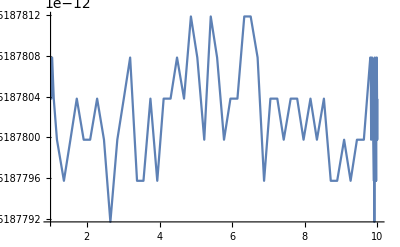

```mathematica
Plot[Abs[curlNum[x,1]],{x,1,10},PlotRange->All]
```

```mathematica
PblackBox[1,2]
```

-1.1189549439007480766604252090319×10^-12+0. ⅈ

```mathematica
lineint
```

{-2.3200000000000001903271670400000156×10^-17,0}

```mathematica
I*dm21 dm31 dm32*Im[U[2,1] Conjugate[U[2,3]] Conjugate[U[3,1]] U[3,3]]//N
```

0.+8.15408×10^-12 ⅈ

```mathematica
(*Line Integral*)
prefactor1[x_,y_]:=I*dm21 dm31 dm32*Im[U[2,1] Conjugate[U[2,3]] Conjugate[U[3,1]] U[3,3]]/norm1[x,y,energy];
prefactor2[x_,y_]:=I*dm21 dm31 dm32*Im[U[2,1] Conjugate[U[2,3]] Conjugate[U[3,1]] U[3,3]]/norm2[x,y,energy];
prefactor3[x_,y_]:=I*dm21 dm31 dm32*Im[U[2,1] Conjugate[U[2,3]] Conjugate[U[3,1]] U[3,3]]/norm3[x,y,energy];
lineint[x_,y_]:= Grad[an[2,2,x,y,energy]-an[1,1,x,y,energy],{x,y}];
(*Surface Integral*)
v1=Grad[an[2,2,x,y,energy],{x,y}]//Rationalize
v2=Grad[an[1,1,x,y,energy],{x,y}]//Rationalize
Cross[Append[v1,0],Append[v2,0]]
surfint[x_,y_]:= Det[{v1,v2}];
```

{-1/3750,1/2}

{1/1875,1/2}

{0,0,-1/2500}

```mathematica
lineint[x,y]
```

{-0.0008,0}

```mathematica
(*(*Define the vector field*)F[x_,y_]:={y^2,x^2}; (*P=0,Q=x^2*)
fh=1

(*Define a square that DOES NOT contain the origin*)
xmin=1;xmax=3;
ymin=1;ymax=3;

(*1. Compute the LINE INTEGRAL around the square (counterclockwise)*)
lineInt=NIntegrate[1/fh*F[x,ymin].{1,0},{x,xmin,xmax}]+(*Bottom edge*)NIntegrate[1/fh*F[xmax,y].{0,1},{y,ymin,ymax}]+(*Right edge*)NIntegrate[1/fh*F[x,ymax].{-1,0},{x,xmax,xmin}]+(*Top edge (reversed)*)NIntegrate[1/fh*F[xmin,y].{0,-1},{y,ymax,ymin}];   
lineInt=NIntegrate[1/fh*F[x,ymin].{1,0},{x,xmin,xmax}]+(*Bottom edge*)NIntegrate[1/fh*F[xmax,y].{0,1},{y,ymin,ymax}]+(*Right edge*)NIntegrate[1/fh*F[x,ymax].{-1,0},{x,xmin,xmax}]+(*Top edge (reversed)*)NIntegrate[1/fh*F[xmin,y].{0,-1},{y,xmin,ymax}];   (*Left edge (reversed)*)

(*2. Compute the CURL (in 2D,the scalar curl)*)
scalarCurl[x_,y_]=Curl[1/fh*F[x,y],{x,y}]; (*This gives a scalar in Mathematica*)

(*3. Compute the SURFACE INTEGRAL of the curl over the square*)
surfaceInt=NIntegrate[scalarCurl[x,y],{x,xmin,xmax},{y,ymin,ymax},AccuracyGoal->5];

(*Print results*)
Print["Line integral (circulation): ",lineInt];
Print["Surface integral (flux of curl): ",surfaceInt];*)
```

```mathematica
λ1[0.2,0.4,energy]
sva2[0.2,0.4,energy]
surf1[0.2,0.3]
prefactor2[x,y] norm2[x,y,energy]
```

-0.000866803

0.0800211-6.3406×10^-22 ⅈ

-0.00380105-1.20387×10^-22 ⅈ

0.+8.15408×10^-12 ⅈ

```mathematica
accgoal=Infinity;
```

```mathematica
surf1[x_,y_] := surfint[x,y]*λ1[x,y,energy]/(λ1[x,y,energy]^2 - sva2[x,y,energy])^3;
surf2[x_,y_] := surfint[x,y]*λ2[x,y,energy]/(λ2[x,y,energy]^2 - sva2[x,y,energy])^3;
surf3[x_,y_] := surfint[x,y]*λ3[x,y,energy]/(λ3[x,y,energy]^2 - sva2[x,y,energy])^3;
```

```mathematica
xlim=01;xlow=0.;
ylim=01;ylow=0.;
BPSurface1N=(2/3) prefactor1[x,y] norm1[x,y,energy] NIntegrate[surf1[x,y],{x,xlow,xlim},{y,ylow,ylim},AccuracyGoal->accgoal]
BPSurface2N=(2/3) prefactor2[x,y] norm2[x,y,energy] NIntegrate[surf2[x,y],{x,xlow,xlim},{y,ylow,ylim},AccuracyGoal->accgoal]
BPSurface3N=(2/3) prefactor3[x,y] norm3[x,y,energy] NIntegrate[surf3[x,y],{x,xlow,xlim},{y,ylow,ylim},AccuracyGoal->accgoal]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.461295,0.00156237}. NIntegrate obtained -1.34343×10^23-5.7051×10^10 ⅈ and 5.03033×10^23 for the integral and error estimates.

0.310132-7.30296×10^11 ⅈ

-1.83021×10^-18-0.0484294 ⅈ

1.23366×10^-22-0.000223195 ⅈ

```mathematica
Plot3D[{Abs[surf3[x,y]],Abs[surf2[x,y]],Abs[surf1[x,y]]},{x,0.5,1},{y,0.5,1},PlotRange->All]
```

-Graphics3D-

```mathematica
Plot3D[{Abs[norm1[x,y,energy]]},{x,0.,10},{y,0.,10},PlotRange->All]
```

-Graphics3D-

```mathematica
v12=v1-v2
```

{-1/1250,0}

```mathematica
norm1[1,2,energy]
```

0.0000115893+0. ⅈ

```mathematica
xlim=100;xlow=0.1;
ylim=100;ylow=0.1;
```

```mathematica
lineIntegral1=NIntegrate[(v12.{1,0}/norm1[x,y,energy]/. y->ylow),{x,xlow,xlim},AccuracyGoal->accgoal2]+NIntegrate[(v12.{0,1}/norm1[x,y,energy]/. x->xlim),{y,ylow,ylim},AccuracyGoal->accgoal2]+NIntegrate[(v12.{1,0}/norm1[x,y,energy]/. y->ylim),{x,xlim,xlow},AccuracyGoal->accgoal2]+NIntegrate[(v12.{0,1}/norm1[x,y,energy]/. x->xlow),{y,ylim,ylow},AccuracyGoal->accgoal2]
```

-113484.+0. ⅈ

```mathematica
lineint[x,y]
```

{-0.0008,0}

```mathematica
lint1[x_,y_]:=prefactor1[x,y]*lineint[x,y];
lint2[x_,y_]:=prefactor2[x,y]*lineint[x,y];
lint3[x_,y_]:=prefactor3[x,y]*lineint[x,y];
```

```mathematica
lint1[x,y]/.{x->0,y->2.}
```

{0.-1.25851×10^-9 ⅈ,0.+0. ⅈ}

```mathematica
NIntegrate[lint1[x,y]/.{x->0},{y,0,1},AccuracyGoal->6]
NIntegrate[lint1[x,y]/.{x->0},{y,1,0},AccuracyGoal->6]
```

{0.-0.000112089 ⅈ,0.+0. ⅈ}

{0.+0.000112089 ⅈ,0.+0. ⅈ}

```mathematica
accgoal2=10;
```

```mathematica
lineIntegral1=NIntegrate[(lint1[x,y].{1,0}/. y->ylow),{x,xlow,xlim},AccuracyGoal->accgoal2]+NIntegrate[(lint1[x,y].{0,1}/. x->xlim),{y,ylow,ylim},AccuracyGoal->accgoal2]+NIntegrate[(lint1[x,y].{1,0}/. y->ylim),{x,xlim,xlow},AccuracyGoal->accgoal2]+NIntegrate[(lint1[x,y].{0,1}/. x->xlow),{y,ylim,ylow},AccuracyGoal->accgoal2]
lineIntegral2=NIntegrate[(lint2[x,y].{1,0}/. y->ylow),{x,xlow,xlim},AccuracyGoal->accgoal2]+NIntegrate[(lint2[x,y].{0,1}/. x->xlim),{y,ylow,ylim},AccuracyGoal->accgoal2]+NIntegrate[(lint2[x,y].{1,0}/. y->ylim),{x,xlim,xlow},AccuracyGoal->accgoal2]+NIntegrate[(lint2[x,y].{0,1}/. x->xlow),{y,ylim,ylow},AccuracyGoal->accgoal2]
lineIntegral3=NIntegrate[(lint3[x,y].{1,0}/. y->ylow),{x,xlow,xlim},AccuracyGoal->accgoal2]+NIntegrate[(lint3[x,y].{0,1}/. x->xlim),{y,ylow,ylim},AccuracyGoal->accgoal2]+NIntegrate[(lint3[x,y].{1,0}/. y->ylim),{x,xlim,xlow},AccuracyGoal->accgoal2]+NIntegrate[(lint3[x,y].{0,1}/. x->xlow),{y,ylim,ylow},AccuracyGoal->accgoal2]
```

0.-9.2536×10^-7 ⅈ

0.-2.48275×10^-6 ⅈ

0.-4.23215×10^-9 ⅈ

```mathematica
BPSurface1N
BPSurface2N
BPSurface3N
```

0.310132-7.30296×10^11 ⅈ

-1.83021×10^-18-0.0484294 ⅈ

1.23366×10^-22-0.000223195 ⅈ

```mathematica
surfacecurl1[x_,y_] :=Curl[Append[Refine[Re[lineint[x,y]]/Re[norm1[x,y,energy]],Element[{x,y},Reals]],0],{x,y,z}];
surfacecurl2[x_,y_] :=Curl[Append[Refine[lineint[x,y]/norm2[x,y,energy],Element[{x,y},Reals]],0],{x,y,z}]//ComplexExpand;
surfacecurl3[x_,y_] :=Curl[Append[Refine[lineint[x,y]/norm3[x,y,energy],Element[{x,y},Reals]],0],{x,y,z}]//ComplexExpand;
```

```mathematica
surfacecurl1[x,y][[3]]/.{x->1,y->2}//ComplexExpand
```

-69.0015+0.169459 ⅈ

```mathematica
NIntegrate[surfacecurl1[x,y][[3]],{x,xlow,xlim},{y,ylow,ylim},AccuracyGoal->5]
NIntegrate[surfacecurl2[x,y][[3]],{x,xlow,xlim},{y,ylow,ylim},AccuracyGoal->5]
NIntegrate[surfacecurl3[x,y][[3]],{x,xlow,xlim},{y,ylow,ylim},AccuracyGoal->5]
```

-113483.+203.51 ⅈ

-304471.+1292.25 ⅈ

-519.022-0.223524 ⅈ

```mathematica
surfacecurl1N =prefactor1[x,y] norm1[x,y,energy]NIntegrate[surfacecurl1[x,y][[3]],{x,xlow,xlim},{y,ylow,ylim},AccuracyGoal->5]
surfacecurl2N =prefactor2[x,y] norm2[x,y,energy]NIntegrate[surfacecurl2[x,y][[3]],{x,xlow,xlim},{y,ylow,ylim},AccuracyGoal->5]
surfacecurl3N =prefactor3[x,y] norm3[x,y,energy]NIntegrate[surfacecurl3[x,y][[3]],{x,xlow,xlim},{y,ylow,ylim},AccuracyGoal->5]
```

-1.65944×10^-9-9.25349×10^-7 ⅈ

-1.05371×10^-8-2.48268×10^-6 ⅈ

1.82263×10^-12-4.23215×10^-9 ⅈ

```mathematica
lineIntegral1
lineIntegral2
lineIntegral3
```

0.-2.6093×10^-15 ⅈ

0.-2.6093×10^-15 ⅈ

0.-2.6093×10^-15 ⅈ

### 3(3a + 0s) case

```mathematica
ClearAll[a11,a12,a13,a22,a23,λi,Ni,x]
```

```mathematica
Uti=(1/Ni)*{(a22[x]-λi[x]) a13-a23 a12,(a11[x]-λi[x]) a23-a13 Conjugate[a12],a12 Conjugate[a12]-(a22[x]-λi[x]) (a11[x]-λi[x])};
```

```mathematica
Utii=(1/Ni)*{-(a22[x]-λi[x])(a33[x]-λi[x])+a23 Conjugate[a23],(a33[x]-λi[x]) Conjugate[a12]-a23 Conjugate[a13],(a22[x]-λi[x]) Conjugate[a13] - Conjugate[a12]Conjugate[a23]}
```

{((λi(x)-a22(x)) (a33(x)-λi(x))+a23 Conjugate[a23])/Ni,(Conjugate[a12] (a33(x)-λi(x))-a23 Conjugate[a13])/Ni,(Conjugate[a13] (a22(x)-λi(x))-Conjugate[a12] Conjugate[a23])/Ni}

```mathematica
norm=Conjugate[Ni*Uti].(Ni*Uti)//Simplify//Distribute//Expand
```

-a13 Conjugate[a12] Conjugate[a23] Conjugate[a11(x)]-a12 a23 a11(x) Conjugate[a13]-a12 a11(x) Conjugate[a12] a22(x)-a12 Conjugate[a12] Conjugate[a11(x)] Conjugate[a22(x)]+a12 Conjugate[a12] Conjugate[a11(x)] Conjugate[λi(x)]+a12 a11(x) Conjugate[a12] λi(x)+a11(x) a22(x) (Conjugate[λi(x)])^2+(λi(x))^2 Conjugate[a11(x)] Conjugate[a22(x)]-a11(x) a22(x) Conjugate[a11(x)] Conjugate[λi(x)]-a11(x) a22(x) Conjugate[a22(x)] Conjugate[λi(x)]-a11(x) λi(x) Conjugate[a11(x)] Conjugate[a22(x)]-a22(x) λi(x) Conjugate[a11(x)] Conjugate[a22(x)]+a22(x) λi(x) Conjugate[a11(x)] Conjugate[λi(x)]+a11(x) λi(x) Conjugate[a22(x)] Conjugate[λi(x)]+a11(x) a22(x) Conjugate[a11(x)] Conjugate[a22(x)]-a23 a11(x) Conjugate[a23] Conjugate[λi(x)]-a23 Conjugate[a23] λi(x) Conjugate[a11(x)]+a23 a11(x) Conjugate[a23] Conjugate[a11(x)]-(λi(x))^2 Conjugate[a11(x)] Conjugate[λi(x)]-a11(x) λi(x) (Conjugate[λi(x)])^2+a11(x) λi(x) Conjugate[a11(x)] Conjugate[λi(x)]+a12^2 (Conjugate[a12])^2+a12 a23 Conjugate[(a12 a23-a13 a22(x)+a13 λi(x))]-a13 a22(x) Conjugate[(a12 a23-a13 a22(x)+a13 λi(x))]+a13 λi(x) Conjugate[(a12 a23-a13 a22(x)+a13 λi(x))]+a13 Conjugate[a12] Conjugate[a23] Conjugate[λi(x)]+a12 a23 Conjugate[a13] λi(x)+a12 a13 Conjugate[a12] Conjugate[a13]+a12 Conjugate[a12] Conjugate[a22(x)] Conjugate[λi(x)]+a12 Conjugate[a12] a22(x) λi(x)-a12 Conjugate[a12] (Conjugate[λi(x)])^2-a12 Conjugate[a12] (λi(x))^2-(λi(x))^2 Conjugate[a22(x)] Conjugate[λi(x)]-a22(x) λi(x) (Conjugate[λi(x)])^2+a22(x) λi(x) Conjugate[a22(x)] Conjugate[λi(x)]+a23 Conjugate[a23] λi(x) Conjugate[λi(x)]+(λi(x))^2 (Conjugate[λi(x)])^2

```mathematica
norm2=Simplify[norm,Assumptions->{Element[λi[x],Reals],Element[a11[x],Reals],Element[a22[x],Reals]}]//Expand
```

-a12 a23 a11(x) Conjugate[a13]-a13 a11(x) Conjugate[a12] Conjugate[a23]-2 a12 a11(x) Conjugate[a12] a22(x)+2 a12 a11(x) Conjugate[a12] λi(x)+4 a11(x) a22(x) (λi(x))^2-2 a11(x) (a22(x))^2 λi(x)-2 (a11(x))^2 a22(x) λi(x)+(a11(x))^2 (a22(x))^2-2 a23 a11(x) Conjugate[a23] λi(x)+a23 (a11(x))^2 Conjugate[a23]-2 a11(x) (λi(x))^3+(a11(x))^2 (λi(x))^2+a12^2 (Conjugate[a12])^2+a13 λi(x) Conjugate[(a12 a23-a13 a22(x)+a13 λi(x))]+a12 a23 Conjugate[(a12 a23-a13 a22(x)+a13 λi(x))]-a13 a22(x) Conjugate[(a12 a23-a13 a22(x)+a13 λi(x))]+a12 a23 Conjugate[a13] λi(x)+a13 Conjugate[a12] Conjugate[a23] λi(x)+a12 a13 Conjugate[a12] Conjugate[a13]+2 a12 Conjugate[a12] a22(x) λi(x)-2 a12 Conjugate[a12] (λi(x))^2-2 a22(x) (λi(x))^3+(a22(x))^2 (λi(x))^2+a23 Conjugate[a23] (λi(x))^2+(λi(x))^4

```mathematica
Collect[norm2,λi[x]]
```

λi(x) (2 a12 a11(x) Conjugate[a12]-2 (a11(x))^2 a22(x)-2 a11(x) (a22(x))^2-2 a23 a11(x) Conjugate[a23]+a13 Conjugate[(a12 a23-a13 a22(x)+a13 λi(x))]+a12 a23 Conjugate[a13]+a13 Conjugate[a12] Conjugate[a23]+2 a12 Conjugate[a12] a22(x))-a12 a23 a11(x) Conjugate[a13]-a13 a11(x) Conjugate[a12] Conjugate[a23]+(λi(x))^2 (4 a11(x) a22(x)+(a11(x))^2-2 a12 Conjugate[a12]+(a22(x))^2+a23 Conjugate[a23])-2 a12 a11(x) Conjugate[a12] a22(x)+(λi(x))^3 (-2 a11(x)-2 a22(x))+(a11(x))^2 (a22(x))^2+a23 (a11(x))^2 Conjugate[a23]+a12^2 (Conjugate[a12])^2+a12 a23 Conjugate[(a12 a23-a13 a22(x)+a13 λi(x))]-a13 a22(x) Conjugate[(a12 a23-a13 a22(x)+a13 λi(x))]+a12 a13 Conjugate[a12] Conjugate[a13]+(λi(x))^4

```mathematica
normi=Conjugate[Ni*Utii].(Ni*Utii)//Simplify//Distribute//Expand
```

-a13 Conjugate[a12] Conjugate[a23] Conjugate[a22(x)]-a12 a23 Conjugate[a13] a22(x)-a13 Conjugate[a12] Conjugate[a23] a33(x)-a12 a23 Conjugate[a13] Conjugate[a33(x)]+a13 Conjugate[a12] Conjugate[a23] Conjugate[λi(x)]+a13 Conjugate[a12] Conjugate[a23] λi(x)+a12 a23 Conjugate[a13] Conjugate[λi(x)]+a12 a23 Conjugate[a13] λi(x)+a12 a23 Conjugate[a12] Conjugate[a23]-a12 Conjugate[a12] a33(x) Conjugate[λi(x)]-a12 Conjugate[a12] λi(x) Conjugate[a33(x)]+a12 Conjugate[a12] a33(x) Conjugate[a33(x)]+a12 Conjugate[a12] λi(x) Conjugate[λi(x)]-a13 Conjugate[a13] a22(x) Conjugate[λi(x)]-a13 Conjugate[a13] λi(x) Conjugate[a22(x)]+a13 Conjugate[a13] a22(x) Conjugate[a22(x)]+a13 a23 Conjugate[a13] Conjugate[a23]+a13 Conjugate[a13] λi(x) Conjugate[λi(x)]-a23 a22(x) Conjugate[a23] a33(x)-a23 Conjugate[a23] Conjugate[a22(x)] Conjugate[a33(x)]+a23 Conjugate[a23] Conjugate[a22(x)] Conjugate[λi(x)]+a23 a22(x) Conjugate[a23] λi(x)+a22(x) a33(x) (Conjugate[λi(x)])^2+(λi(x))^2 Conjugate[a22(x)] Conjugate[a33(x)]-a22(x) a33(x) Conjugate[a22(x)] Conjugate[λi(x)]-a22(x) a33(x) Conjugate[a33(x)] Conjugate[λi(x)]-a22(x) λi(x) Conjugate[a22(x)] Conjugate[a33(x)]-a33(x) λi(x) Conjugate[a22(x)] Conjugate[a33(x)]+a33(x) λi(x) Conjugate[a22(x)] Conjugate[λi(x)]+a22(x) λi(x) Conjugate[a33(x)] Conjugate[λi(x)]+a22(x) a33(x) Conjugate[a22(x)] Conjugate[a33(x)]-(λi(x))^2 Conjugate[a22(x)] Conjugate[λi(x)]-a22(x) λi(x) (Conjugate[λi(x)])^2+a22(x) λi(x) Conjugate[a22(x)] Conjugate[λi(x)]+a23^2 (Conjugate[a23])^2+a23 Conjugate[a23] Conjugate[a33(x)] Conjugate[λi(x)]+a23 Conjugate[a23] a33(x) λi(x)-a23 Conjugate[a23] (Conjugate[λi(x)])^2-a23 Conjugate[a23] (λi(x))^2-(λi(x))^2 Conjugate[a33(x)] Conjugate[λi(x)]-a33(x) λi(x) (Conjugate[λi(x)])^2+a33(x) λi(x) Conjugate[a33(x)] Conjugate[λi(x)]+(λi(x))^2 (Conjugate[λi(x)])^2

```mathematica
normi2=Simplify[normi,Assumptions->{Element[λi[x],Reals],Element[a33[x],Reals],Element[a22[x],Reals]}]//Expand
```

-a12 a23 Conjugate[a13] a22(x)-a13 Conjugate[a12] a22(x) Conjugate[a23]-a12 a23 Conjugate[a13] a33(x)-a13 Conjugate[a12] Conjugate[a23] a33(x)+2 a12 a23 Conjugate[a13] λi(x)+2 a13 Conjugate[a12] Conjugate[a23] λi(x)+a12 a23 Conjugate[a12] Conjugate[a23]-2 a12 Conjugate[a12] a33(x) λi(x)+a12 Conjugate[a12] (a33(x))^2+a12 Conjugate[a12] (λi(x))^2-2 a13 Conjugate[a13] a22(x) λi(x)+a13 Conjugate[a13] (a22(x))^2+a13 a23 Conjugate[a13] Conjugate[a23]+a13 Conjugate[a13] (λi(x))^2-2 a23 a22(x) Conjugate[a23] a33(x)+2 a23 a22(x) Conjugate[a23] λi(x)+4 a22(x) a33(x) (λi(x))^2-2 a22(x) (a33(x))^2 λi(x)-2 (a22(x))^2 a33(x) λi(x)+(a22(x))^2 (a33(x))^2-2 a22(x) (λi(x))^3+(a22(x))^2 (λi(x))^2+a23^2 (Conjugate[a23])^2+2 a23 Conjugate[a23] a33(x) λi(x)-2 a23 Conjugate[a23] (λi(x))^2-2 a33(x) (λi(x))^3+(a33(x))^2 (λi(x))^2+(λi(x))^4

```mathematica
Collect[normi2,λi[x]]
```

(λi(x))^2 (a12 Conjugate[a12]+a13 Conjugate[a13]+4 a22(x) a33(x)+(a22(x))^2-2 a23 Conjugate[a23]+(a33(x))^2)+λi(x) (2 a12 a23 Conjugate[a13]+2 a13 Conjugate[a12] Conjugate[a23]-2 a12 Conjugate[a12] a33(x)-2 a13 Conjugate[a13] a22(x)+2 a23 a22(x) Conjugate[a23]-2 (a22(x))^2 a33(x)-2 a22(x) (a33(x))^2+2 a23 Conjugate[a23] a33(x))-a12 a23 Conjugate[a13] a22(x)-a13 Conjugate[a12] a22(x) Conjugate[a23]-a12 a23 Conjugate[a13] a33(x)-a13 Conjugate[a12] Conjugate[a23] a33(x)+a12 a23 Conjugate[a12] Conjugate[a23]+a12 Conjugate[a12] (a33(x))^2+a13 Conjugate[a13] (a22(x))^2+a13 a23 Conjugate[a13] Conjugate[a23]-2 a23 a22(x) Conjugate[a23] a33(x)+(λi(x))^3 (-2 a22(x)-2 a33(x))+(a22(x))^2 (a33(x))^2+a23^2 (Conjugate[a23])^2+(λi(x))^4

```mathematica
dnorm=Collect[D[norm2,x],λi[x]]
```

λi(x) (2 a12 Conjugate[a12] a11'(x)-4 a11(x) a22(x) a11'(x)-2 (a22(x))^2 a11'(x)-2 a23 Conjugate[a23] a11'(x)-2 (a11(x))^2 a22'(x)-4 a11(x) a22(x) a22'(x)+8 a11(x) a22(x) λi'(x)+2 (a11(x))^2 λi'(x)+a13 (a13 λi'(x)-a13 a22'(x)) Conjugate'(a12 a23-a13 a22(x)+a13 λi(x))+2 a12 Conjugate[a12] a22'(x)-4 a12 Conjugate[a12] λi'(x)+2 (a22(x))^2 λi'(x)+2 a23 Conjugate[a23] λi'(x))-a12 a23 Conjugate[a13] a11'(x)-a13 Conjugate[a12] Conjugate[a23] a11'(x)-2 a12 Conjugate[a12] a22(x) a11'(x)+(λi(x))^3 (-2 a11'(x)-2 a22'(x)+4 λi'(x))+(λi(x))^2 (4 a22(x) a11'(x)+2 a11(x) a11'(x)+4 a11(x) a22'(x)-6 a11(x) λi'(x)+2 a22(x) a22'(x)-6 a22(x) λi'(x))+2 a11(x) (a22(x))^2 a11'(x)+2 a23 a11(x) Conjugate[a23] a11'(x)-2 a12 a11(x) Conjugate[a12] a22'(x)+2 a12 a11(x) Conjugate[a12] λi'(x)+2 (a11(x))^2 a22(x) a22'(x)-2 a11(x) (a22(x))^2 λi'(x)-2 (a11(x))^2 a22(x) λi'(x)-2 a23 a11(x) Conjugate[a23] λi'(x)+a12 a23 (a13 λi'(x)-a13 a22'(x)) Conjugate'(a12 a23-a13 a22(x)+a13 λi(x))-a13 a22(x) (a13 λi'(x)-a13 a22'(x)) Conjugate'(a12 a23-a13 a22(x)+a13 λi(x))-a13 a22'(x) Conjugate[(a12 a23-a13 a22(x)+a13 λi(x))]+a13 λi'(x) Conjugate[(a12 a23-a13 a22(x)+a13 λi(x))]+a12 a23 Conjugate[a13] λi'(x)+a13 Conjugate[a12] Conjugate[a23] λi'(x)+2 a12 Conjugate[a12] a22(x) λi'(x)

```mathematica
sq=(Abs[a12]^2+Abs[a13]^2+Abs[a23]^2+a11^2+a22^2+a11 a22)
```

a11^2+a11 a22+Abs[a12]^2+Abs[a13]^2+a22^2+Abs[a23]^2

```mathematica
sq^2//Expand
```

a11^4+2 a11^3 a22+2 a11^2 Abs[a12]^2+2 a11^2 Abs[a13]^2+3 a11^2 a22^2+2 a11^2 Abs[a23]^2+2 a11 a22 Abs[a12]^2+2 a11 a22 Abs[a13]^2+2 a11 a22^3+2 a11 a22 Abs[a23]^2+2 Abs[a12]^2 Abs[a13]^2+2 a22^2 Abs[a12]^2+2 Abs[a12]^2 Abs[a23]^2+Abs[a12]^4+2 a22^2 Abs[a13]^2+2 Abs[a13]^2 Abs[a23]^2+Abs[a13]^4+a22^4+2 a22^2 Abs[a23]^2+Abs[a23]^4

```mathematica
dUti=D[Uti,x];
expr=Simplify[Uti.Conjugate[dUti]]
```

1/(Ni Conjugate[Ni])(Conjugate[a23] (Conjugate[a11'(x)]-Conjugate[λi'(x)]) (a23 a11(x)-a13 Conjugate[a12]-a23 λi(x))-((a11(x)-λi(x)) (λi(x)-a22(x))+a12 Conjugate[a12]) Conjugate[((a22(x)-λi(x)) (a11'(x)-λi'(x))+(a11(x)-λi(x)) (a22'(x)-λi'(x)))]-Conjugate[a13] (Conjugate[a22'(x)]-Conjugate[λi'(x)]) (a12 a23-a13 a22(x)+a13 λi(x)))

```mathematica
exprc= Simplify[dUti.Conjugate[Uti]]
```

1/(Ni Conjugate[Ni])(a23 (a11'(x)-λi'(x)) (Conjugate[a23] (Conjugate[a11(x)]-Conjugate[λi(x)])-a12 Conjugate[a13])+(-((a22(x)-λi(x)) (a11'(x)-λi'(x)))-(a11(x)-λi(x)) (a22'(x)-λi'(x))) ((Conjugate[a11(x)]-Conjugate[λi(x)]) (Conjugate[λi(x)]-Conjugate[a22(x)])+a12 Conjugate[a12])+a13 (a22'(x)-λi'(x)) Conjugate[(-a12 a23+a13 a22(x)-a13 λi(x))])

```mathematica
expr2c=-(expr-exprc)//Simplify
```

1/(Ni Conjugate[Ni])(-Conjugate[a23] (Conjugate[a11'(x)]-Conjugate[λi'(x)]) (a23 a11(x)-a13 Conjugate[a12]-a23 λi(x))+a23 (a11'(x)-λi'(x)) (Conjugate[a23] (Conjugate[a11(x)]-Conjugate[λi(x)])-a12 Conjugate[a13])+((a11(x)-λi(x)) (λi(x)-a22(x))+a12 Conjugate[a12]) Conjugate[((a22(x)-λi(x)) (a11'(x)-λi'(x))+(a11(x)-λi(x)) (a22'(x)-λi'(x)))]+(-((a22(x)-λi(x)) (a11'(x)-λi'(x)))-(a11(x)-λi(x)) (a22'(x)-λi'(x))) ((Conjugate[a11(x)]-Conjugate[λi(x)]) (Conjugate[λi(x)]-Conjugate[a22(x)])+a12 Conjugate[a12])+Conjugate[a13] (Conjugate[a22'(x)]-Conjugate[λi'(x)]) (a12 a23-a13 a22(x)+a13 λi(x))+a13 (a22'(x)-λi'(x)) Conjugate[(-a12 a23+a13 a22(x)-a13 λi(x))])

```mathematica
expr2=-expr+Conjugate[expr]//Simplify
```

1/(Ni Conjugate[Ni])(-Conjugate[a23] (Conjugate[a11'(x)]-Conjugate[λi'(x)]) (a23 a11(x)-a13 Conjugate[a12]-a23 λi(x))+a23 (a11'(x)-λi'(x)) (Conjugate[(a23 a11(x)-a23 λi(x))]-a12 Conjugate[a13])+((a11(x)-λi(x)) (λi(x)-a22(x))+a12 Conjugate[a12]) Conjugate[((a22(x)-λi(x)) (a11'(x)-λi'(x))+(a11(x)-λi(x)) (a22'(x)-λi'(x)))]-((a22(x)-λi(x)) (a11'(x)-λi'(x))+(a11(x)-λi(x)) (a22'(x)-λi'(x))) ((Conjugate[a11(x)]-Conjugate[λi(x)]) (Conjugate[λi(x)]-Conjugate[a22(x)])+a12 Conjugate[a12])+Conjugate[a13] (Conjugate[a22'(x)]-Conjugate[λi'(x)]) (a12 a23-a13 a22(x)+a13 λi(x))-a13 (a22'(x)-λi'(x)) Conjugate[(a12 a23-a13 a22(x)+a13 λi(x))])

```mathematica
cexp2c=ComplexExpand[expr2c,{a23,a12,a13}]
```

ⅈ (-(2 Re(a12) Re(a13) Im(a23) a11'(x))/Ni^2+(2 Re(a12) Im(a13) Re(a23) a11'(x))/Ni^2-(2 Im(a12) Re(a13) Re(a23) a11'(x))/Ni^2-(2 Im(a12) Im(a13) Im(a23) a11'(x))/Ni^2+(2 Re(a12) Re(a13) Im(a23) a22'(x))/Ni^2-(2 Re(a12) Im(a13) Re(a23) a22'(x))/Ni^2+(2 Im(a12) Re(a13) Re(a23) a22'(x))/Ni^2+(2 Im(a12) Im(a13) Im(a23) a22'(x))/Ni^2)

```mathematica
cexp2=ComplexExpand[expr2,{a23,a13,a12}]
```

ⅈ (-(2 Re(a12) Re(a13) Im(a23) a11'(x))/Ni^2+(2 Re(a12) Im(a13) Re(a23) a11'(x))/Ni^2-(2 Im(a12) Re(a13) Re(a23) a11'(x))/Ni^2-(2 Im(a12) Im(a13) Im(a23) a11'(x))/Ni^2+(2 Re(a12) Re(a13) Im(a23) a22'(x))/Ni^2-(2 Re(a12) Im(a13) Re(a23) a22'(x))/Ni^2+(2 Im(a12) Re(a13) Re(a23) a22'(x))/Ni^2+(2 Im(a12) Im(a13) Im(a23) a22'(x))/Ni^2)

```mathematica
Uti=(1/Ni)*{(a22[x]-λi[x]) a13[x]-a23[x] *a12[x],(a11[x]-λi[x]) a23[x]-a13[x] Conjugate[a12[x]],a12[x] Conjugate[a12[x]]-(a22[x]-λi[x]) (a11[x]-λi[x])};
```

```mathematica
dUti=D[Uti,x];
expr=Simplify[Uti.Conjugate[dUti]]
```

1/(Ni Conjugate[Ni])((-a11(x) a23(x)+a13(x) Conjugate[a12(x)]+a23(x) λi(x)) (a12(x) Conjugate[a13'(x)]-Conjugate[((a11(x)-λi(x)) a23'(x)-a13(x) a12'(x) Conjugate'(a12(x))+a23(x) (a11'(x)-λi'(x)))])+((a11(x)-λi(x)) (λi(x)-a22(x))+a12(x) Conjugate[a12(x)]) (Conjugate[(a12(x) a12'(x) Conjugate'(a12(x))-(a22(x)-λi(x)) (a11'(x)-λi'(x))-(a11(x)-λi(x)) (a22'(x)-λi'(x)))]+a12(x) Conjugate[a12'(x)])+(a13(x) (a22(x)-λi(x))-a12(x) a23(x)) Conjugate[(-a23(x) a12'(x)+(a22(x)-λi(x)) a13'(x)-a12(x) a23'(x)+a13(x) (a22'(x)-λi'(x)))])

```mathematica
expr2=expr-Conjugate[expr]//Simplify
```

1/(Ni Conjugate[Ni])((-a11(x) a23(x)+a13(x) Conjugate[a12(x)]+a23(x) λi(x)) (a12(x) Conjugate[a13'(x)]-Conjugate[((a11(x)-λi(x)) a23'(x)-a13(x) a12'(x) Conjugate'(a12(x))+a23(x) (a11'(x)-λi'(x)))])-(Conjugate[a23(x)] (Conjugate[λi(x)]-Conjugate[a11(x)])+a12(x) Conjugate[a13(x)]) (a23(x) (λi'(x)-a11'(x))-a11(x) a23'(x)+a13(x) a12'(x) Conjugate'(a12(x))+Conjugate[a12(x)] a13'(x)+λi(x) a23'(x))+((a11(x)-λi(x)) (λi(x)-a22(x))+a12(x) Conjugate[a12(x)]) (Conjugate[(a12(x) a12'(x) Conjugate'(a12(x))-(a22(x)-λi(x)) (a11'(x)-λi'(x))-(a11(x)-λi(x)) (a22'(x)-λi'(x)))]+a12(x) Conjugate[a12'(x)])-((Conjugate[a11(x)]-Conjugate[λi(x)]) (Conjugate[λi(x)]-Conjugate[a22(x)])+a12(x) Conjugate[a12(x)]) (-(a22(x)-λi(x)) (a11'(x)-λi'(x))-(a11(x)-λi(x)) (a22'(x)-λi'(x))+a12(x) a12'(x) Conjugate'(a12(x))+Conjugate[a12(x)] a12'(x))+(a13(x) (a22(x)-λi(x))-a12(x) a23(x)) Conjugate[(-a23(x) a12'(x)+(a22(x)-λi(x)) a13'(x)-a12(x) a23'(x)+a13(x) (a22'(x)-λi'(x)))]+Conjugate[(a13(x) (a22(x)-λi(x))-a12(x) a23(x))] (a23(x) a12'(x)+a12(x) a23'(x)-a22(x) a13'(x)+λi(x) a13'(x)-a13(x) a22'(x)+a13(x) λi'(x)))

```mathematica
cexp2mass=ComplexExpand[expr2,{a23[x],a13[x],a12[x],a23'[x],a13'[x],a12'[x]}]
```

ⅈ (-(4 Im(a12'(x)) (Re(a12(x)))^3)/Ni^2-(2 Im(a13'(x)) Re(a13(x)) (Re(a12(x)))^2)/Ni^2-(2 Im(a23'(x)) Re(a23(x)) (Re(a12(x)))^2)/Ni^2+(2 Im(a13(x)) Re(a13'(x)) (Re(a12(x)))^2)/Ni^2+(2 Im(a23(x)) Re(a23'(x)) (Re(a12(x)))^2)/Ni^2-(2 Im(a12'(x)) (Re(a13(x)))^2 Re(a12(x)))/Ni^2-(2 Im(a12'(x)) (Re(a23(x)))^2 Re(a12(x)))/Ni^2+(4 Im(a12'(x)) (λi(x))^2 Re(a12(x)))/Ni^2-(4 (Im(a12(x)))^2 Im(a12'(x)) Re(a12(x)))/Ni^2-(2 (Im(a13(x)))^2 Im(a12'(x)) Re(a12(x)))/Ni^2-(2 (Im(a23(x)))^2 Im(a12'(x)) Re(a12(x)))/Ni^2+(4 a11(x) a22(x) Im(a12'(x)) Re(a12(x)))/Ni^2+(2 a11(x) Im(a23'(x)) Re(a13(x)) Re(a12(x)))/Ni^2+(2 a22(x) Im(a23'(x)) Re(a13(x)) Re(a12(x)))/Ni^2+(2 a11(x) Im(a13'(x)) Re(a23(x)) Re(a12(x)))/Ni^2+(2 a22(x) Im(a13'(x)) Re(a23(x)) Re(a12(x)))/Ni^2-(2 a11(x) Im(a23(x)) Re(a13'(x)) Re(a12(x)))/Ni^2-(2 a22(x) Im(a23(x)) Re(a13'(x)) Re(a12(x)))/Ni^2-(2 a11(x) Im(a13(x)) Re(a23'(x)) Re(a12(x)))/Ni^2-(2 a22(x) Im(a13(x)) Re(a23'(x)) Re(a12(x)))/Ni^2-(4 a11(x) Im(a12'(x)) λi(x) Re(a12(x)))/Ni^2-(4 a22(x) Im(a12'(x)) λi(x) Re(a12(x)))/Ni^2-(4 Im(a23'(x)) Re(a13(x)) λi(x) Re(a12(x)))/Ni^2-(4 Im(a13'(x)) Re(a23(x)) λi(x) Re(a12(x)))/Ni^2+(4 Im(a23(x)) Re(a13'(x)) λi(x) Re(a12(x)))/Ni^2+(4 Im(a13(x)) Re(a23'(x)) λi(x) Re(a12(x)))/Ni^2+(2 Im(a23(x)) Re(a13(x)) a11'(x) Re(a12(x)))/Ni^2-(2 Im(a13(x)) Re(a23(x)) a11'(x) Re(a12(x)))/Ni^2-(2 Im(a23(x)) Re(a13(x)) a22'(x) Re(a12(x)))/Ni^2+(2 Im(a13(x)) Re(a23(x)) a22'(x) Re(a12(x)))/Ni^2-(2 Im(a13'(x)) Re(a13(x)) (λi(x))^2)/Ni^2-(2 Im(a23'(x)) Re(a23(x)) (λi(x))^2)/Ni^2+(2 Im(a13(x)) Re(a13'(x)) (λi(x))^2)/Ni^2+(2 Im(a23(x)) Re(a23'(x)) (λi(x))^2)/Ni^2+(2 a11(x) Im(a13(x)) Im(a23(x)) Im(a12'(x)))/Ni^2+(2 a22(x) Im(a13(x)) Im(a23(x)) Im(a12'(x)))/Ni^2-(2 a11(x) Im(a12(x)) Im(a23(x)) Im(a13'(x)))/Ni^2-(2 a22(x) Im(a12(x)) Im(a23(x)) Im(a13'(x)))/Ni^2+(2 a11(x) Im(a12(x)) Im(a13(x)) Im(a23'(x)))/Ni^2+(2 a22(x) Im(a12(x)) Im(a13(x)) Im(a23'(x)))/Ni^2-(2 (a22(x))^2 Im(a13'(x)) Re(a13(x)))/Ni^2-(2 (Im(a12(x)))^2 Im(a13'(x)) Re(a13(x)))/Ni^2-(2 (a11(x))^2 Im(a23'(x)) Re(a23(x)))/Ni^2-(2 (Im(a12(x)))^2 Im(a23'(x)) Re(a23(x)))/Ni^2+(2 a11(x) Im(a12'(x)) Re(a13(x)) Re(a23(x)))/Ni^2+(2 a22(x) Im(a12'(x)) Re(a13(x)) Re(a23(x)))/Ni^2-(2 Im(a12(x)) (Im(a13(x)))^2 Re(a12'(x)))/Ni^2+(2 Im(a12(x)) (Im(a23(x)))^2 Re(a12'(x)))/Ni^2-(2 Im(a12(x)) (Re(a13(x)))^2 Re(a12'(x)))/Ni^2+(2 Im(a12(x)) (Re(a23(x)))^2 Re(a12'(x)))/Ni^2-(2 a11(x) Im(a23(x)) Re(a13(x)) Re(a12'(x)))/Ni^2+(2 a22(x) Im(a23(x)) Re(a13(x)) Re(a12'(x)))/Ni^2+(2 a11(x) Im(a13(x)) Re(a23(x)) Re(a12'(x)))/Ni^2-(2 a22(x) Im(a13(x)) Re(a23(x)) Re(a12'(x)))/Ni^2+(2 (a22(x))^2 Im(a13(x)) Re(a13'(x)))/Ni^2+(2 (Im(a12(x)))^2 Im(a13(x)) Re(a13'(x)))/Ni^2-(2 a11(x) Im(a12(x)) Re(a23(x)) Re(a13'(x)))/Ni^2-(2 a22(x) Im(a12(x)) Re(a23(x)) Re(a13'(x)))/Ni^2+(2 (a11(x))^2 Im(a23(x)) Re(a23'(x)))/Ni^2+(2 (Im(a12(x)))^2 Im(a23(x)) Re(a23'(x)))/Ni^2+(2 a11(x) Im(a12(x)) Re(a13(x)) Re(a23'(x)))/Ni^2+(2 a22(x) Im(a12(x)) Re(a13(x)) Re(a23'(x)))/Ni^2-(4 Im(a13(x)) Im(a23(x)) Im(a12'(x)) λi(x))/Ni^2+(4 Im(a12(x)) Im(a23(x)) Im(a13'(x)) λi(x))/Ni^2-(4 Im(a12(x)) Im(a13(x)) Im(a23'(x)) λi(x))/Ni^2+(4 a22(x) Im(a13'(x)) Re(a13(x)) λi(x))/Ni^2+(4 a11(x) Im(a23'(x)) Re(a23(x)) λi(x))/Ni^2-(4 Im(a12'(x)) Re(a13(x)) Re(a23(x)) λi(x))/Ni^2-(4 a22(x) Im(a13(x)) Re(a13'(x)) λi(x))/Ni^2+(4 Im(a12(x)) Re(a23(x)) Re(a13'(x)) λi(x))/Ni^2-(4 a11(x) Im(a23(x)) Re(a23'(x)) λi(x))/Ni^2-(4 Im(a12(x)) Re(a13(x)) Re(a23'(x)) λi(x))/Ni^2+(2 Im(a12(x)) Im(a13(x)) Im(a23(x)) a11'(x))/Ni^2+(2 Im(a12(x)) Re(a13(x)) Re(a23(x)) a11'(x))/Ni^2-(2 Im(a12(x)) Im(a13(x)) Im(a23(x)) a22'(x))/Ni^2-(2 Im(a12(x)) Re(a13(x)) Re(a23(x)) a22'(x))/Ni^2)

```mathematica
Collect[cexp2mass,{λi[x]}] (*To Simplify*)
```

ⅈ ((4 Im(a12'(x)) Re(a12(x)))/Ni^2-(2 Im(a13'(x)) Re(a13(x)))/Ni^2-(2 Im(a23'(x)) Re(a23(x)))/Ni^2+(2 Im(a13(x)) Re(a13'(x)))/Ni^2+(2 Im(a23(x)) Re(a23'(x)))/Ni^2) (λi(x))^2+ⅈ (-(4 Im(a13(x)) Im(a23(x)) Im(a12'(x)))/Ni^2-(4 a11(x) Re(a12(x)) Im(a12'(x)))/Ni^2-(4 a22(x) Re(a12(x)) Im(a12'(x)))/Ni^2-(4 Re(a13(x)) Re(a23(x)) Im(a12'(x)))/Ni^2+(4 Im(a12(x)) Im(a23(x)) Im(a13'(x)))/Ni^2-(4 Im(a12(x)) Im(a13(x)) Im(a23'(x)))/Ni^2+(4 a22(x) Im(a13'(x)) Re(a13(x)))/Ni^2-(4 Im(a23'(x)) Re(a12(x)) Re(a13(x)))/Ni^2+(4 a11(x) Im(a23'(x)) Re(a23(x)))/Ni^2-(4 Im(a13'(x)) Re(a12(x)) Re(a23(x)))/Ni^2-(4 a22(x) Im(a13(x)) Re(a13'(x)))/Ni^2+(4 Im(a23(x)) Re(a12(x)) Re(a13'(x)))/Ni^2+(4 Im(a12(x)) Re(a23(x)) Re(a13'(x)))/Ni^2-(4 a11(x) Im(a23(x)) Re(a23'(x)))/Ni^2+(4 Im(a13(x)) Re(a12(x)) Re(a23'(x)))/Ni^2-(4 Im(a12(x)) Re(a13(x)) Re(a23'(x)))/Ni^2) λi(x)+ⅈ (-(4 Im(a12'(x)) (Re(a12(x)))^3)/Ni^2-(2 Im(a13'(x)) Re(a13(x)) (Re(a12(x)))^2)/Ni^2-(2 Im(a23'(x)) Re(a23(x)) (Re(a12(x)))^2)/Ni^2+(2 Im(a13(x)) Re(a13'(x)) (Re(a12(x)))^2)/Ni^2+(2 Im(a23(x)) Re(a23'(x)) (Re(a12(x)))^2)/Ni^2-(2 Im(a12'(x)) (Re(a13(x)))^2 Re(a12(x)))/Ni^2-(2 Im(a12'(x)) (Re(a23(x)))^2 Re(a12(x)))/Ni^2-(4 (Im(a12(x)))^2 Im(a12'(x)) Re(a12(x)))/Ni^2-(2 (Im(a13(x)))^2 Im(a12'(x)) Re(a12(x)))/Ni^2-(2 (Im(a23(x)))^2 Im(a12'(x)) Re(a12(x)))/Ni^2+(4 a11(x) a22(x) Im(a12'(x)) Re(a12(x)))/Ni^2+(2 a11(x) Im(a23'(x)) Re(a13(x)) Re(a12(x)))/Ni^2+(2 a22(x) Im(a23'(x)) Re(a13(x)) Re(a12(x)))/Ni^2+(2 a11(x) Im(a13'(x)) Re(a23(x)) Re(a12(x)))/Ni^2+(2 a22(x) Im(a13'(x)) Re(a23(x)) Re(a12(x)))/Ni^2-(2 a11(x) Im(a23(x)) Re(a13'(x)) Re(a12(x)))/Ni^2-(2 a22(x) Im(a23(x)) Re(a13'(x)) Re(a12(x)))/Ni^2-(2 a11(x) Im(a13(x)) Re(a23'(x)) Re(a12(x)))/Ni^2-(2 a22(x) Im(a13(x)) Re(a23'(x)) Re(a12(x)))/Ni^2+(2 Im(a23(x)) Re(a13(x)) a11'(x) Re(a12(x)))/Ni^2-(2 Im(a13(x)) Re(a23(x)) a11'(x) Re(a12(x)))/Ni^2-(2 Im(a23(x)) Re(a13(x)) a22'(x) Re(a12(x)))/Ni^2+(2 Im(a13(x)) Re(a23(x)) a22'(x) Re(a12(x)))/Ni^2+(2 a11(x) Im(a13(x)) Im(a23(x)) Im(a12'(x)))/Ni^2+(2 a22(x) Im(a13(x)) Im(a23(x)) Im(a12'(x)))/Ni^2-(2 a11(x) Im(a12(x)) Im(a23(x)) Im(a13'(x)))/Ni^2-(2 a22(x) Im(a12(x)) Im(a23(x)) Im(a13'(x)))/Ni^2+(2 a11(x) Im(a12(x)) Im(a13(x)) Im(a23'(x)))/Ni^2+(2 a22(x) Im(a12(x)) Im(a13(x)) Im(a23'(x)))/Ni^2-(2 (a22(x))^2 Im(a13'(x)) Re(a13(x)))/Ni^2-(2 (Im(a12(x)))^2 Im(a13'(x)) Re(a13(x)))/Ni^2-(2 (a11(x))^2 Im(a23'(x)) Re(a23(x)))/Ni^2-(2 (Im(a12(x)))^2 Im(a23'(x)) Re(a23(x)))/Ni^2+(2 a11(x) Im(a12'(x)) Re(a13(x)) Re(a23(x)))/Ni^2+(2 a22(x) Im(a12'(x)) Re(a13(x)) Re(a23(x)))/Ni^2-(2 Im(a12(x)) (Im(a13(x)))^2 Re(a12'(x)))/Ni^2+(2 Im(a12(x)) (Im(a23(x)))^2 Re(a12'(x)))/Ni^2-(2 Im(a12(x)) (Re(a13(x)))^2 Re(a12'(x)))/Ni^2+(2 Im(a12(x)) (Re(a23(x)))^2 Re(a12'(x)))/Ni^2-(2 a11(x) Im(a23(x)) Re(a13(x)) Re(a12'(x)))/Ni^2+(2 a22(x) Im(a23(x)) Re(a13(x)) Re(a12'(x)))/Ni^2+(2 a11(x) Im(a13(x)) Re(a23(x)) Re(a12'(x)))/Ni^2-(2 a22(x) Im(a13(x)) Re(a23(x)) Re(a12'(x)))/Ni^2+(2 (a22(x))^2 Im(a13(x)) Re(a13'(x)))/Ni^2+(2 (Im(a12(x)))^2 Im(a13(x)) Re(a13'(x)))/Ni^2-(2 a11(x) Im(a12(x)) Re(a23(x)) Re(a13'(x)))/Ni^2-(2 a22(x) Im(a12(x)) Re(a23(x)) Re(a13'(x)))/Ni^2+(2 (a11(x))^2 Im(a23(x)) Re(a23'(x)))/Ni^2+(2 (Im(a12(x)))^2 Im(a23(x)) Re(a23'(x)))/Ni^2+(2 a11(x) Im(a12(x)) Re(a13(x)) Re(a23'(x)))/Ni^2+(2 a22(x) Im(a12(x)) Re(a13(x)) Re(a23'(x)))/Ni^2+(2 Im(a12(x)) Im(a13(x)) Im(a23(x)) a11'(x))/Ni^2+(2 Im(a12(x)) Re(a13(x)) Re(a23(x)) a11'(x))/Ni^2-(2 Im(a12(x)) Im(a13(x)) Im(a23(x)) a22'(x))/Ni^2-(2 Im(a12(x)) Re(a13(x)) Re(a23(x)) a22'(x))/Ni^2)

```mathematica
cexp2
```

ⅈ (-(2 Re(a12) Re(a13) Im(a23) a11'(x))/Ni^2+(2 Re(a12) Im(a13) Re(a23) a11'(x))/Ni^2-(2 Im(a12) Re(a13) Re(a23) a11'(x))/Ni^2-(2 Im(a12) Im(a13) Im(a23) a11'(x))/Ni^2+(2 Re(a12) Re(a13) Im(a23) a22'(x))/Ni^2-(2 Re(a12) Im(a13) Re(a23) a22'(x))/Ni^2+(2 Im(a12) Re(a13) Re(a23) a22'(x))/Ni^2+(2 Im(a12) Im(a13) Im(a23) a22'(x))/Ni^2)

```mathematica
Collect[cexp2mass,{a22'[x],a11'[x]}]
```

ⅈ (-(4 Im(a12'(x)) (Re(a12(x)))^3)/Ni^2-(2 Im(a13'(x)) Re(a13(x)) (Re(a12(x)))^2)/Ni^2-(2 Im(a23'(x)) Re(a23(x)) (Re(a12(x)))^2)/Ni^2+(2 Im(a13(x)) Re(a13'(x)) (Re(a12(x)))^2)/Ni^2+(2 Im(a23(x)) Re(a23'(x)) (Re(a12(x)))^2)/Ni^2-(2 Im(a12'(x)) (Re(a13(x)))^2 Re(a12(x)))/Ni^2-(2 Im(a12'(x)) (Re(a23(x)))^2 Re(a12(x)))/Ni^2+(4 Im(a12'(x)) (λi(x))^2 Re(a12(x)))/Ni^2-(4 (Im(a12(x)))^2 Im(a12'(x)) Re(a12(x)))/Ni^2-(2 (Im(a13(x)))^2 Im(a12'(x)) Re(a12(x)))/Ni^2-(2 (Im(a23(x)))^2 Im(a12'(x)) Re(a12(x)))/Ni^2+(4 a11(x) a22(x) Im(a12'(x)) Re(a12(x)))/Ni^2+(2 a11(x) Im(a23'(x)) Re(a13(x)) Re(a12(x)))/Ni^2+(2 a22(x) Im(a23'(x)) Re(a13(x)) Re(a12(x)))/Ni^2+(2 a11(x) Im(a13'(x)) Re(a23(x)) Re(a12(x)))/Ni^2+(2 a22(x) Im(a13'(x)) Re(a23(x)) Re(a12(x)))/Ni^2-(2 a11(x) Im(a23(x)) Re(a13'(x)) Re(a12(x)))/Ni^2-(2 a22(x) Im(a23(x)) Re(a13'(x)) Re(a12(x)))/Ni^2-(2 a11(x) Im(a13(x)) Re(a23'(x)) Re(a12(x)))/Ni^2-(2 a22(x) Im(a13(x)) Re(a23'(x)) Re(a12(x)))/Ni^2-(4 a11(x) Im(a12'(x)) λi(x) Re(a12(x)))/Ni^2-(4 a22(x) Im(a12'(x)) λi(x) Re(a12(x)))/Ni^2-(4 Im(a23'(x)) Re(a13(x)) λi(x) Re(a12(x)))/Ni^2-(4 Im(a13'(x)) Re(a23(x)) λi(x) Re(a12(x)))/Ni^2+(4 Im(a23(x)) Re(a13'(x)) λi(x) Re(a12(x)))/Ni^2+(4 Im(a13(x)) Re(a23'(x)) λi(x) Re(a12(x)))/Ni^2-(2 Im(a13'(x)) Re(a13(x)) (λi(x))^2)/Ni^2-(2 Im(a23'(x)) Re(a23(x)) (λi(x))^2)/Ni^2+(2 Im(a13(x)) Re(a13'(x)) (λi(x))^2)/Ni^2+(2 Im(a23(x)) Re(a23'(x)) (λi(x))^2)/Ni^2+(2 a11(x) Im(a13(x)) Im(a23(x)) Im(a12'(x)))/Ni^2+(2 a22(x) Im(a13(x)) Im(a23(x)) Im(a12'(x)))/Ni^2-(2 a11(x) Im(a12(x)) Im(a23(x)) Im(a13'(x)))/Ni^2-(2 a22(x) Im(a12(x)) Im(a23(x)) Im(a13'(x)))/Ni^2+(2 a11(x) Im(a12(x)) Im(a13(x)) Im(a23'(x)))/Ni^2+(2 a22(x) Im(a12(x)) Im(a13(x)) Im(a23'(x)))/Ni^2-(2 (a22(x))^2 Im(a13'(x)) Re(a13(x)))/Ni^2-(2 (Im(a12(x)))^2 Im(a13'(x)) Re(a13(x)))/Ni^2-(2 (a11(x))^2 Im(a23'(x)) Re(a23(x)))/Ni^2-(2 (Im(a12(x)))^2 Im(a23'(x)) Re(a23(x)))/Ni^2+(2 a11(x) Im(a12'(x)) Re(a13(x)) Re(a23(x)))/Ni^2+(2 a22(x) Im(a12'(x)) Re(a13(x)) Re(a23(x)))/Ni^2-(2 Im(a12(x)) (Im(a13(x)))^2 Re(a12'(x)))/Ni^2+(2 Im(a12(x)) (Im(a23(x)))^2 Re(a12'(x)))/Ni^2-(2 Im(a12(x)) (Re(a13(x)))^2 Re(a12'(x)))/Ni^2+(2 Im(a12(x)) (Re(a23(x)))^2 Re(a12'(x)))/Ni^2-(2 a11(x) Im(a23(x)) Re(a13(x)) Re(a12'(x)))/Ni^2+(2 a22(x) Im(a23(x)) Re(a13(x)) Re(a12'(x)))/Ni^2+(2 a11(x) Im(a13(x)) Re(a23(x)) Re(a12'(x)))/Ni^2-(2 a22(x) Im(a13(x)) Re(a23(x)) Re(a12'(x)))/Ni^2+(2 (a22(x))^2 Im(a13(x)) Re(a13'(x)))/Ni^2+(2 (Im(a12(x)))^2 Im(a13(x)) Re(a13'(x)))/Ni^2-(2 a11(x) Im(a12(x)) Re(a23(x)) Re(a13'(x)))/Ni^2-(2 a22(x) Im(a12(x)) Re(a23(x)) Re(a13'(x)))/Ni^2+(2 (a11(x))^2 Im(a23(x)) Re(a23'(x)))/Ni^2+(2 (Im(a12(x)))^2 Im(a23(x)) Re(a23'(x)))/Ni^2+(2 a11(x) Im(a12(x)) Re(a13(x)) Re(a23'(x)))/Ni^2+(2 a22(x) Im(a12(x)) Re(a13(x)) Re(a23'(x)))/Ni^2-(4 Im(a13(x)) Im(a23(x)) Im(a12'(x)) λi(x))/Ni^2+(4 Im(a12(x)) Im(a23(x)) Im(a13'(x)) λi(x))/Ni^2-(4 Im(a12(x)) Im(a13(x)) Im(a23'(x)) λi(x))/Ni^2+(4 a22(x) Im(a13'(x)) Re(a13(x)) λi(x))/Ni^2+(4 a11(x) Im(a23'(x)) Re(a23(x)) λi(x))/Ni^2-(4 Im(a12'(x)) Re(a13(x)) Re(a23(x)) λi(x))/Ni^2-(4 a22(x) Im(a13(x)) Re(a13'(x)) λi(x))/Ni^2+(4 Im(a12(x)) Re(a23(x)) Re(a13'(x)) λi(x))/Ni^2-(4 a11(x) Im(a23(x)) Re(a23'(x)) λi(x))/Ni^2-(4 Im(a12(x)) Re(a13(x)) Re(a23'(x)) λi(x))/Ni^2)+ⅈ ((2 Im(a12(x)) Im(a13(x)) Im(a23(x)))/Ni^2+(2 Re(a12(x)) Re(a13(x)) Im(a23(x)))/Ni^2-(2 Im(a13(x)) Re(a12(x)) Re(a23(x)))/Ni^2+(2 Im(a12(x)) Re(a13(x)) Re(a23(x)))/Ni^2) a11'(x)+ⅈ (-(2 Im(a12(x)) Im(a13(x)) Im(a23(x)))/Ni^2-(2 Re(a12(x)) Re(a13(x)) Im(a23(x)))/Ni^2+(2 Im(a13(x)) Re(a12(x)) Re(a23(x)))/Ni^2-(2 Im(a12(x)) Re(a13(x)) Re(a23(x)))/Ni^2) a22'(x)

```mathematica
c11=Coefficient[Collect[cexp2mass,{a22'[x],a11'[x]}],a11'[x]]
c22=Coefficient[Collect[cexp2mass,{a22'[x],a11'[x]}],a22'[x]]
```

ⅈ ((2 Re(a12(x)) Re(a13(x)) Im(a23(x)))/Ni^2-(2 Re(a12(x)) Im(a13(x)) Re(a23(x)))/Ni^2+(2 Im(a12(x)) Re(a13(x)) Re(a23(x)))/Ni^2+(2 Im(a12(x)) Im(a13(x)) Im(a23(x)))/Ni^2)

ⅈ (-(2 Re(a12(x)) Re(a13(x)) Im(a23(x)))/Ni^2+(2 Re(a12(x)) Im(a13(x)) Re(a23(x)))/Ni^2-(2 Im(a12(x)) Re(a13(x)) Re(a23(x)))/Ni^2-(2 Im(a12(x)) Im(a13(x)) Im(a23(x)))/Ni^2)

```mathematica
approxcexp=cexp2mass/.{a22'[x]->0,a11'[x]->0}
```

ⅈ (-(4 Im(a12'(x)) (Re(a12(x)))^3)/Ni^2-(2 Im(a13'(x)) Re(a13(x)) (Re(a12(x)))^2)/Ni^2-(2 Im(a23'(x)) Re(a23(x)) (Re(a12(x)))^2)/Ni^2+(2 Im(a13(x)) Re(a13'(x)) (Re(a12(x)))^2)/Ni^2+(2 Im(a23(x)) Re(a23'(x)) (Re(a12(x)))^2)/Ni^2-(2 Im(a12'(x)) (Re(a13(x)))^2 Re(a12(x)))/Ni^2-(2 Im(a12'(x)) (Re(a23(x)))^2 Re(a12(x)))/Ni^2+(4 Im(a12'(x)) (λi(x))^2 Re(a12(x)))/Ni^2-(4 (Im(a12(x)))^2 Im(a12'(x)) Re(a12(x)))/Ni^2-(2 (Im(a13(x)))^2 Im(a12'(x)) Re(a12(x)))/Ni^2-(2 (Im(a23(x)))^2 Im(a12'(x)) Re(a12(x)))/Ni^2+(4 a11(x) a22(x) Im(a12'(x)) Re(a12(x)))/Ni^2+(2 a11(x) Im(a23'(x)) Re(a13(x)) Re(a12(x)))/Ni^2+(2 a22(x) Im(a23'(x)) Re(a13(x)) Re(a12(x)))/Ni^2+(2 a11(x) Im(a13'(x)) Re(a23(x)) Re(a12(x)))/Ni^2+(2 a22(x) Im(a13'(x)) Re(a23(x)) Re(a12(x)))/Ni^2-(2 a11(x) Im(a23(x)) Re(a13'(x)) Re(a12(x)))/Ni^2-(2 a22(x) Im(a23(x)) Re(a13'(x)) Re(a12(x)))/Ni^2-(2 a11(x) Im(a13(x)) Re(a23'(x)) Re(a12(x)))/Ni^2-(2 a22(x) Im(a13(x)) Re(a23'(x)) Re(a12(x)))/Ni^2-(4 a11(x) Im(a12'(x)) λi(x) Re(a12(x)))/Ni^2-(4 a22(x) Im(a12'(x)) λi(x) Re(a12(x)))/Ni^2-(4 Im(a23'(x)) Re(a13(x)) λi(x) Re(a12(x)))/Ni^2-(4 Im(a13'(x)) Re(a23(x)) λi(x) Re(a12(x)))/Ni^2+(4 Im(a23(x)) Re(a13'(x)) λi(x) Re(a12(x)))/Ni^2+(4 Im(a13(x)) Re(a23'(x)) λi(x) Re(a12(x)))/Ni^2-(2 Im(a13'(x)) Re(a13(x)) (λi(x))^2)/Ni^2-(2 Im(a23'(x)) Re(a23(x)) (λi(x))^2)/Ni^2+(2 Im(a13(x)) Re(a13'(x)) (λi(x))^2)/Ni^2+(2 Im(a23(x)) Re(a23'(x)) (λi(x))^2)/Ni^2+(2 a11(x) Im(a13(x)) Im(a23(x)) Im(a12'(x)))/Ni^2+(2 a22(x) Im(a13(x)) Im(a23(x)) Im(a12'(x)))/Ni^2-(2 a11(x) Im(a12(x)) Im(a23(x)) Im(a13'(x)))/Ni^2-(2 a22(x) Im(a12(x)) Im(a23(x)) Im(a13'(x)))/Ni^2+(2 a11(x) Im(a12(x)) Im(a13(x)) Im(a23'(x)))/Ni^2+(2 a22(x) Im(a12(x)) Im(a13(x)) Im(a23'(x)))/Ni^2-(2 (a22(x))^2 Im(a13'(x)) Re(a13(x)))/Ni^2-(2 (Im(a12(x)))^2 Im(a13'(x)) Re(a13(x)))/Ni^2-(2 (a11(x))^2 Im(a23'(x)) Re(a23(x)))/Ni^2-(2 (Im(a12(x)))^2 Im(a23'(x)) Re(a23(x)))/Ni^2+(2 a11(x) Im(a12'(x)) Re(a13(x)) Re(a23(x)))/Ni^2+(2 a22(x) Im(a12'(x)) Re(a13(x)) Re(a23(x)))/Ni^2-(2 Im(a12(x)) (Im(a13(x)))^2 Re(a12'(x)))/Ni^2+(2 Im(a12(x)) (Im(a23(x)))^2 Re(a12'(x)))/Ni^2-(2 Im(a12(x)) (Re(a13(x)))^2 Re(a12'(x)))/Ni^2+(2 Im(a12(x)) (Re(a23(x)))^2 Re(a12'(x)))/Ni^2-(2 a11(x) Im(a23(x)) Re(a13(x)) Re(a12'(x)))/Ni^2+(2 a22(x) Im(a23(x)) Re(a13(x)) Re(a12'(x)))/Ni^2+(2 a11(x) Im(a13(x)) Re(a23(x)) Re(a12'(x)))/Ni^2-(2 a22(x) Im(a13(x)) Re(a23(x)) Re(a12'(x)))/Ni^2+(2 (a22(x))^2 Im(a13(x)) Re(a13'(x)))/Ni^2+(2 (Im(a12(x)))^2 Im(a13(x)) Re(a13'(x)))/Ni^2-(2 a11(x) Im(a12(x)) Re(a23(x)) Re(a13'(x)))/Ni^2-(2 a22(x) Im(a12(x)) Re(a23(x)) Re(a13'(x)))/Ni^2+(2 (a11(x))^2 Im(a23(x)) Re(a23'(x)))/Ni^2+(2 (Im(a12(x)))^2 Im(a23(x)) Re(a23'(x)))/Ni^2+(2 a11(x) Im(a12(x)) Re(a13(x)) Re(a23'(x)))/Ni^2+(2 a22(x) Im(a12(x)) Re(a13(x)) Re(a23'(x)))/Ni^2-(4 Im(a13(x)) Im(a23(x)) Im(a12'(x)) λi(x))/Ni^2+(4 Im(a12(x)) Im(a23(x)) Im(a13'(x)) λi(x))/Ni^2-(4 Im(a12(x)) Im(a13(x)) Im(a23'(x)) λi(x))/Ni^2+(4 a22(x) Im(a13'(x)) Re(a13(x)) λi(x))/Ni^2+(4 a11(x) Im(a23'(x)) Re(a23(x)) λi(x))/Ni^2-(4 Im(a12'(x)) Re(a13(x)) Re(a23(x)) λi(x))/Ni^2-(4 a22(x) Im(a13(x)) Re(a13'(x)) λi(x))/Ni^2+(4 Im(a12(x)) Re(a23(x)) Re(a13'(x)) λi(x))/Ni^2-(4 a11(x) Im(a23(x)) Re(a23'(x)) λi(x))/Ni^2-(4 Im(a12(x)) Re(a13(x)) Re(a23'(x)) λi(x))/Ni^2)

```mathematica
approxcexp+a11'[x]*c11+a22'[x]*c22-cexp2mass //Simplify
```

0

```mathematica
Collect[approxcexp,{Im[a12'[x]],Re[a12'[x]],Im[a13'[x]],Re[a13'[x]],Im[a23'[x]],Re[a23'[x]]}]
```

ⅈ (-(2 Im(a12(x)) (Im(a13(x)))^2)/Ni^2+(2 a11(x) Re(a23(x)) Im(a13(x)))/Ni^2-(2 a22(x) Re(a23(x)) Im(a13(x)))/Ni^2+(2 Im(a12(x)) (Im(a23(x)))^2)/Ni^2-(2 Im(a12(x)) (Re(a13(x)))^2)/Ni^2+(2 Im(a12(x)) (Re(a23(x)))^2)/Ni^2-(2 a11(x) Im(a23(x)) Re(a13(x)))/Ni^2+(2 a22(x) Im(a23(x)) Re(a13(x)))/Ni^2) Re(a12'(x))+ⅈ Re(a13'(x)) ((2 Im(a13(x)) (a22(x))^2)/Ni^2-(2 Im(a23(x)) Re(a12(x)) a22(x))/Ni^2-(2 Im(a12(x)) Re(a23(x)) a22(x))/Ni^2-(4 Im(a13(x)) λi(x) a22(x))/Ni^2+(2 Im(a13(x)) (Re(a12(x)))^2)/Ni^2+(2 Im(a13(x)) (λi(x))^2)/Ni^2+(2 (Im(a12(x)))^2 Im(a13(x)))/Ni^2-(2 a11(x) Im(a23(x)) Re(a12(x)))/Ni^2-(2 a11(x) Im(a12(x)) Re(a23(x)))/Ni^2+(4 Im(a23(x)) Re(a12(x)) λi(x))/Ni^2+(4 Im(a12(x)) Re(a23(x)) λi(x))/Ni^2)+ⅈ Re(a23'(x)) ((2 Im(a23(x)) (a11(x))^2)/Ni^2-(2 Im(a13(x)) Re(a12(x)) a11(x))/Ni^2+(2 Im(a12(x)) Re(a13(x)) a11(x))/Ni^2-(4 Im(a23(x)) λi(x) a11(x))/Ni^2+(2 Im(a23(x)) (Re(a12(x)))^2)/Ni^2+(2 Im(a23(x)) (λi(x))^2)/Ni^2+(2 (Im(a12(x)))^2 Im(a23(x)))/Ni^2-(2 a22(x) Im(a13(x)) Re(a12(x)))/Ni^2+(2 a22(x) Im(a12(x)) Re(a13(x)))/Ni^2+(4 Im(a13(x)) Re(a12(x)) λi(x))/Ni^2-(4 Im(a12(x)) Re(a13(x)) λi(x))/Ni^2)+ⅈ Im(a12'(x)) (-(4 (Re(a12(x)))^3)/Ni^2-(4 (Im(a12(x)))^2 Re(a12(x)))/Ni^2-(2 (Im(a13(x)))^2 Re(a12(x)))/Ni^2-(2 (Im(a23(x)))^2 Re(a12(x)))/Ni^2-(2 (Re(a13(x)))^2 Re(a12(x)))/Ni^2-(2 (Re(a23(x)))^2 Re(a12(x)))/Ni^2+(4 (λi(x))^2 Re(a12(x)))/Ni^2+(4 a11(x) a22(x) Re(a12(x)))/Ni^2-(4 a11(x) λi(x) Re(a12(x)))/Ni^2-(4 a22(x) λi(x) Re(a12(x)))/Ni^2+(2 a11(x) Im(a13(x)) Im(a23(x)))/Ni^2+(2 a22(x) Im(a13(x)) Im(a23(x)))/Ni^2+(2 a11(x) Re(a13(x)) Re(a23(x)))/Ni^2+(2 a22(x) Re(a13(x)) Re(a23(x)))/Ni^2-(4 Im(a13(x)) Im(a23(x)) λi(x))/Ni^2-(4 Re(a13(x)) Re(a23(x)) λi(x))/Ni^2)+ⅈ Im(a13'(x)) (-(2 Re(a13(x)) (a22(x))^2)/Ni^2-(2 Im(a12(x)) Im(a23(x)) a22(x))/Ni^2+(2 Re(a12(x)) Re(a23(x)) a22(x))/Ni^2+(4 Re(a13(x)) λi(x) a22(x))/Ni^2-(2 Re(a13(x)) (λi(x))^2)/Ni^2-(2 a11(x) Im(a12(x)) Im(a23(x)))/Ni^2-(2 (Im(a12(x)))^2 Re(a13(x)))/Ni^2-(2 (Re(a12(x)))^2 Re(a13(x)))/Ni^2+(2 a11(x) Re(a12(x)) Re(a23(x)))/Ni^2+(4 Im(a12(x)) Im(a23(x)) λi(x))/Ni^2-(4 Re(a12(x)) Re(a23(x)) λi(x))/Ni^2)+ⅈ Im(a23'(x)) (-(2 Re(a23(x)) (a11(x))^2)/Ni^2+(2 Im(a12(x)) Im(a13(x)) a11(x))/Ni^2+(2 Re(a12(x)) Re(a13(x)) a11(x))/Ni^2+(4 Re(a23(x)) λi(x) a11(x))/Ni^2-(2 Re(a23(x)) (λi(x))^2)/Ni^2+(2 a22(x) Im(a12(x)) Im(a13(x)))/Ni^2+(2 a22(x) Re(a12(x)) Re(a13(x)))/Ni^2-(2 (Im(a12(x)))^2 Re(a23(x)))/Ni^2-(2 (Re(a12(x)))^2 Re(a23(x)))/Ni^2-(4 Im(a12(x)) Im(a13(x)) λi(x))/Ni^2-(4 Re(a12(x)) Re(a13(x)) λi(x))/Ni^2)

```mathematica
Collect[cexp2mass,{Im[a12'[x]],Re[a12'[x]],Im[a13'[x]],Re[a13'[x]],Im[a23'[x]],Re[a23'[x]]}]
```

ⅈ (-(2 Im(a12(x)) (Im(a13(x)))^2)/Ni^2+(2 a11(x) Re(a23(x)) Im(a13(x)))/Ni^2-(2 a22(x) Re(a23(x)) Im(a13(x)))/Ni^2+(2 Im(a12(x)) (Im(a23(x)))^2)/Ni^2-(2 Im(a12(x)) (Re(a13(x)))^2)/Ni^2+(2 Im(a12(x)) (Re(a23(x)))^2)/Ni^2-(2 a11(x) Im(a23(x)) Re(a13(x)))/Ni^2+(2 a22(x) Im(a23(x)) Re(a13(x)))/Ni^2) Re(a12'(x))+ⅈ Re(a13'(x)) ((2 Im(a13(x)) (a22(x))^2)/Ni^2-(2 Im(a23(x)) Re(a12(x)) a22(x))/Ni^2-(2 Im(a12(x)) Re(a23(x)) a22(x))/Ni^2-(4 Im(a13(x)) λi(x) a22(x))/Ni^2+(2 Im(a13(x)) (Re(a12(x)))^2)/Ni^2+(2 Im(a13(x)) (λi(x))^2)/Ni^2+(2 (Im(a12(x)))^2 Im(a13(x)))/Ni^2-(2 a11(x) Im(a23(x)) Re(a12(x)))/Ni^2-(2 a11(x) Im(a12(x)) Re(a23(x)))/Ni^2+(4 Im(a23(x)) Re(a12(x)) λi(x))/Ni^2+(4 Im(a12(x)) Re(a23(x)) λi(x))/Ni^2)+ⅈ Re(a23'(x)) ((2 Im(a23(x)) (a11(x))^2)/Ni^2-(2 Im(a13(x)) Re(a12(x)) a11(x))/Ni^2+(2 Im(a12(x)) Re(a13(x)) a11(x))/Ni^2-(4 Im(a23(x)) λi(x) a11(x))/Ni^2+(2 Im(a23(x)) (Re(a12(x)))^2)/Ni^2+(2 Im(a23(x)) (λi(x))^2)/Ni^2+(2 (Im(a12(x)))^2 Im(a23(x)))/Ni^2-(2 a22(x) Im(a13(x)) Re(a12(x)))/Ni^2+(2 a22(x) Im(a12(x)) Re(a13(x)))/Ni^2+(4 Im(a13(x)) Re(a12(x)) λi(x))/Ni^2-(4 Im(a12(x)) Re(a13(x)) λi(x))/Ni^2)+ⅈ Im(a12'(x)) (-(4 (Re(a12(x)))^3)/Ni^2-(4 (Im(a12(x)))^2 Re(a12(x)))/Ni^2-(2 (Im(a13(x)))^2 Re(a12(x)))/Ni^2-(2 (Im(a23(x)))^2 Re(a12(x)))/Ni^2-(2 (Re(a13(x)))^2 Re(a12(x)))/Ni^2-(2 (Re(a23(x)))^2 Re(a12(x)))/Ni^2+(4 (λi(x))^2 Re(a12(x)))/Ni^2+(4 a11(x) a22(x) Re(a12(x)))/Ni^2-(4 a11(x) λi(x) Re(a12(x)))/Ni^2-(4 a22(x) λi(x) Re(a12(x)))/Ni^2+(2 a11(x) Im(a13(x)) Im(a23(x)))/Ni^2+(2 a22(x) Im(a13(x)) Im(a23(x)))/Ni^2+(2 a11(x) Re(a13(x)) Re(a23(x)))/Ni^2+(2 a22(x) Re(a13(x)) Re(a23(x)))/Ni^2-(4 Im(a13(x)) Im(a23(x)) λi(x))/Ni^2-(4 Re(a13(x)) Re(a23(x)) λi(x))/Ni^2)+ⅈ Im(a13'(x)) (-(2 Re(a13(x)) (a22(x))^2)/Ni^2-(2 Im(a12(x)) Im(a23(x)) a22(x))/Ni^2+(2 Re(a12(x)) Re(a23(x)) a22(x))/Ni^2+(4 Re(a13(x)) λi(x) a22(x))/Ni^2-(2 Re(a13(x)) (λi(x))^2)/Ni^2-(2 a11(x) Im(a12(x)) Im(a23(x)))/Ni^2-(2 (Im(a12(x)))^2 Re(a13(x)))/Ni^2-(2 (Re(a12(x)))^2 Re(a13(x)))/Ni^2+(2 a11(x) Re(a12(x)) Re(a23(x)))/Ni^2+(4 Im(a12(x)) Im(a23(x)) λi(x))/Ni^2-(4 Re(a12(x)) Re(a23(x)) λi(x))/Ni^2)+ⅈ Im(a23'(x)) (-(2 Re(a23(x)) (a11(x))^2)/Ni^2+(2 Im(a12(x)) Im(a13(x)) a11(x))/Ni^2+(2 Re(a12(x)) Re(a13(x)) a11(x))/Ni^2+(4 Re(a23(x)) λi(x) a11(x))/Ni^2-(2 Re(a23(x)) (λi(x))^2)/Ni^2+(2 a22(x) Im(a12(x)) Im(a13(x)))/Ni^2+(2 a22(x) Re(a12(x)) Re(a13(x)))/Ni^2-(2 (Im(a12(x)))^2 Re(a23(x)))/Ni^2-(2 (Re(a12(x)))^2 Re(a23(x)))/Ni^2-(4 Im(a12(x)) Im(a13(x)) λi(x))/Ni^2-(4 Re(a12(x)) Re(a13(x)) λi(x))/Ni^2)+ⅈ ((2 Im(a12(x)) Im(a13(x)) Im(a23(x)) a11'(x))/Ni^2+(2 Im(a23(x)) Re(a12(x)) Re(a13(x)) a11'(x))/Ni^2-(2 Im(a13(x)) Re(a12(x)) Re(a23(x)) a11'(x))/Ni^2+(2 Im(a12(x)) Re(a13(x)) Re(a23(x)) a11'(x))/Ni^2-(2 Im(a12(x)) Im(a13(x)) Im(a23(x)) a22'(x))/Ni^2-(2 Im(a23(x)) Re(a12(x)) Re(a13(x)) a22'(x))/Ni^2+(2 Im(a13(x)) Re(a12(x)) Re(a23(x)) a22'(x))/Ni^2-(2 Im(a12(x)) Re(a13(x)) Re(a23(x)) a22'(x))/Ni^2)

```mathematica
expr21=Simplify[expr2,Assumptions->{Element[λi[x],Reals],Element[Ni,Reals]}]//Expand
```

(a11'(x) (λi(x))^3)/Ni^2+(a22'(x) (λi(x))^3)/Ni^2-(2 λi'(x) (λi(x))^3)/Ni^2-(a12(x) Conjugate[a12'(x)] (λi(x))^2)/Ni^2-(Conjugate[(a12(x) a12'(x) Conjugate'(a12(x))-(a22(x)-λi(x)) (a11'(x)-λi'(x))-(a11(x)-λi(x)) (a22'(x)-λi'(x)))] (λi(x))^2)/Ni^2-(a22(x) a11'(x) (λi(x))^2)/Ni^2-(Conjugate[a11(x)] a11'(x) (λi(x))^2)/Ni^2-(Conjugate[a22(x)] a11'(x) (λi(x))^2)/Ni^2+(Conjugate[a12(x)] a12'(x) (λi(x))^2)/Ni^2-(a11(x) a22'(x) (λi(x))^2)/Ni^2-(Conjugate[a11(x)] a22'(x) (λi(x))^2)/Ni^2-(Conjugate[a22(x)] a22'(x) (λi(x))^2)/Ni^2-(Conjugate[a23(x)] a23'(x) (λi(x))^2)/Ni^2+(a12(x) a12'(x) Conjugate'(a12(x)) (λi(x))^2)/Ni^2+(a11(x) λi'(x) (λi(x))^2)/Ni^2+(a22(x) λi'(x) (λi(x))^2)/Ni^2+(2 Conjugate[a11(x)] λi'(x) (λi(x))^2)/Ni^2+(2 Conjugate[a22(x)] λi'(x) (λi(x))^2)/Ni^2+(a11(x) a12(x) Conjugate[a12'(x)] λi(x))/Ni^2+(a12(x) a22(x) Conjugate[a12'(x)] λi(x))/Ni^2+(a12(x) a23(x) Conjugate[a13'(x)] λi(x))/Ni^2-(a23(x) Conjugate[((a11(x)-λi(x)) a23'(x)-a13(x) a12'(x) Conjugate'(a12(x))+a23(x) (a11'(x)-λi'(x)))] λi(x))/Ni^2-(a13(x) Conjugate[(-a23(x) a12'(x)+(a22(x)-λi(x)) a13'(x)-a12(x) a23'(x)+a13(x) (a22'(x)-λi'(x)))] λi(x))/Ni^2+(a11(x) Conjugate[(a12(x) a12'(x) Conjugate'(a12(x))-(a22(x)-λi(x)) (a11'(x)-λi'(x))-(a11(x)-λi(x)) (a22'(x)-λi'(x)))] λi(x))/Ni^2+(a22(x) Conjugate[(a12(x) a12'(x) Conjugate'(a12(x))-(a22(x)-λi(x)) (a11'(x)-λi'(x))-(a11(x)-λi(x)) (a22'(x)-λi'(x)))] λi(x))/Ni^2+(a22(x) Conjugate[a11(x)] a11'(x) λi(x))/Ni^2-(a12(x) Conjugate[a12(x)] a11'(x) λi(x))/Ni^2+(a22(x) Conjugate[a22(x)] a11'(x) λi(x))/Ni^2+(Conjugate[a11(x)] Conjugate[a22(x)] a11'(x) λi(x))/Ni^2+(a23(x) Conjugate[a23(x)] a11'(x) λi(x))/Ni^2-(Conjugate[a11(x)] Conjugate[a12(x)] a12'(x) λi(x))/Ni^2-(Conjugate[a12(x)] Conjugate[a22(x)] a12'(x) λi(x))/Ni^2-(Conjugate[a12(x)] Conjugate[a23(x)] a13'(x) λi(x))/Ni^2+(Conjugate[(a13(x) (a22(x)-λi(x))-a12(x) a23(x))] a13'(x) λi(x))/Ni^2+(a11(x) Conjugate[a11(x)] a22'(x) λi(x))/Ni^2-(a12(x) Conjugate[a12(x)] a22'(x) λi(x))/Ni^2+(a11(x) Conjugate[a22(x)] a22'(x) λi(x))/Ni^2+(Conjugate[a11(x)] Conjugate[a22(x)] a22'(x) λi(x))/Ni^2-(a12(x) Conjugate[a13(x)] a23'(x) λi(x))/Ni^2+(a11(x) Conjugate[a23(x)] a23'(x) λi(x))/Ni^2+(Conjugate[a11(x)] Conjugate[a23(x)] a23'(x) λi(x))/Ni^2-(a12(x) Conjugate[a11(x)] a12'(x) Conjugate'(a12(x)) λi(x))/Ni^2-(a12(x) Conjugate[a22(x)] a12'(x) Conjugate'(a12(x)) λi(x))/Ni^2-(a13(x) Conjugate[a23(x)] a12'(x) Conjugate'(a12(x)) λi(x))/Ni^2-(a11(x) Conjugate[a11(x)] λi'(x) λi(x))/Ni^2-(a22(x) Conjugate[a11(x)] λi'(x) λi(x))/Ni^2+(2 a12(x) Conjugate[a12(x)] λi'(x) λi(x))/Ni^2-(a11(x) Conjugate[a22(x)] λi'(x) λi(x))/Ni^2-(a22(x) Conjugate[a22(x)] λi'(x) λi(x))/Ni^2-(2 Conjugate[a11(x)] Conjugate[a22(x)] λi'(x) λi(x))/Ni^2-(a23(x) Conjugate[a23(x)] λi'(x) λi(x))/Ni^2-(a11(x) a12(x) a22(x) Conjugate[a12'(x)])/Ni^2+((a12(x))^2 Conjugate[a12(x)] Conjugate[a12'(x)])/Ni^2-(a11(x) a12(x) a23(x) Conjugate[a13'(x)])/Ni^2+(a12(x) a13(x) Conjugate[a12(x)] Conjugate[a13'(x)])/Ni^2+(a11(x) a23(x) Conjugate[((a11(x)-λi(x)) a23'(x)-a13(x) a12'(x) Conjugate'(a12(x))+a23(x) (a11'(x)-λi'(x)))])/Ni^2-(a13(x) Conjugate[a12(x)] Conjugate[((a11(x)-λi(x)) a23'(x)-a13(x) a12'(x) Conjugate'(a12(x))+a23(x) (a11'(x)-λi'(x)))])/Ni^2+(a13(x) a22(x) Conjugate[(-a23(x) a12'(x)+(a22(x)-λi(x)) a13'(x)-a12(x) a23'(x)+a13(x) (a22'(x)-λi'(x)))])/Ni^2-(a12(x) a23(x) Conjugate[(-a23(x) a12'(x)+(a22(x)-λi(x)) a13'(x)-a12(x) a23'(x)+a13(x) (a22'(x)-λi'(x)))])/Ni^2-(a11(x) a22(x) Conjugate[(a12(x) a12'(x) Conjugate'(a12(x))-(a22(x)-λi(x)) (a11'(x)-λi'(x))-(a11(x)-λi(x)) (a22'(x)-λi'(x)))])/Ni^2+(a12(x) Conjugate[a12(x)] Conjugate[(a12(x) a12'(x) Conjugate'(a12(x))-(a22(x)-λi(x)) (a11'(x)-λi'(x))-(a11(x)-λi(x)) (a22'(x)-λi'(x)))])/Ni^2+(a12(x) a22(x) Conjugate[a12(x)] a11'(x))/Ni^2+(a12(x) a23(x) Conjugate[a13(x)] a11'(x))/Ni^2-(a22(x) Conjugate[a11(x)] Conjugate[a22(x)] a11'(x))/Ni^2-(a23(x) Conjugate[a11(x)] Conjugate[a23(x)] a11'(x))/Ni^2-(a12(x) (Conjugate[a12(x)])^2 a12'(x))/Ni^2+(Conjugate[a11(x)] Conjugate[a12(x)] Conjugate[a22(x)] a12'(x))/Ni^2+(a23(x) Conjugate[(a13(x) (a22(x)-λi(x))-a12(x) a23(x))] a12'(x))/Ni^2-(a12(x) Conjugate[a12(x)] Conjugate[a13(x)] a13'(x))/Ni^2+(Conjugate[a11(x)] Conjugate[a12(x)] Conjugate[a23(x)] a13'(x))/Ni^2-(a22(x) Conjugate[(a13(x) (a22(x)-λi(x))-a12(x) a23(x))] a13'(x))/Ni^2+(a11(x) a12(x) Conjugate[a12(x)] a22'(x))/Ni^2-(a11(x) Conjugate[a11(x)] Conjugate[a22(x)] a22'(x))/Ni^2-(a13(x) Conjugate[(a13(x) (a22(x)-λi(x))-a12(x) a23(x))] a22'(x))/Ni^2+(a11(x) a12(x) Conjugate[a13(x)] a23'(x))/Ni^2-(a11(x) Conjugate[a11(x)] Conjugate[a23(x)] a23'(x))/Ni^2+(a12(x) Conjugate[(a13(x) (a22(x)-λi(x))-a12(x) a23(x))] a23'(x))/Ni^2-((a12(x))^2 Conjugate[a12(x)] a12'(x) Conjugate'(a12(x)))/Ni^2-(a12(x) a13(x) Conjugate[a13(x)] a12'(x) Conjugate'(a12(x)))/Ni^2+(a12(x) Conjugate[a11(x)] Conjugate[a22(x)] a12'(x) Conjugate'(a12(x)))/Ni^2+(a13(x) Conjugate[a11(x)] Conjugate[a23(x)] a12'(x) Conjugate'(a12(x)))/Ni^2-(a11(x) a12(x) Conjugate[a12(x)] λi'(x))/Ni^2-(a12(x) a22(x) Conjugate[a12(x)] λi'(x))/Ni^2-(a12(x) a23(x) Conjugate[a13(x)] λi'(x))/Ni^2+(a11(x) Conjugate[a11(x)] Conjugate[a22(x)] λi'(x))/Ni^2+(a22(x) Conjugate[a11(x)] Conjugate[a22(x)] λi'(x))/Ni^2+(a23(x) Conjugate[a11(x)] Conjugate[a23(x)] λi'(x))/Ni^2+(a13(x) Conjugate[(a13(x) (a22(x)-λi(x))-a12(x) a23(x))] λi'(x))/Ni^2

```mathematica
aexpr21=expr21/.{λi'[x]->0}//ExpandAll
```

(a11'(x) (λi(x))^3)/Ni^2+(a22'(x) (λi(x))^3)/Ni^2-(a12(x) Conjugate[a12'(x)] (λi(x))^2)/Ni^2-(Conjugate[(-a22(x) a11'(x)+λi(x) a11'(x)-a11(x) a22'(x)+λi(x) a22'(x)+a12(x) a12'(x) Conjugate'(a12(x)))] (λi(x))^2)/Ni^2-(a22(x) a11'(x) (λi(x))^2)/Ni^2-(Conjugate[a11(x)] a11'(x) (λi(x))^2)/Ni^2-(Conjugate[a22(x)] a11'(x) (λi(x))^2)/Ni^2+(Conjugate[a12(x)] a12'(x) (λi(x))^2)/Ni^2-(a11(x) a22'(x) (λi(x))^2)/Ni^2-(Conjugate[a11(x)] a22'(x) (λi(x))^2)/Ni^2-(Conjugate[a22(x)] a22'(x) (λi(x))^2)/Ni^2-(Conjugate[a23(x)] a23'(x) (λi(x))^2)/Ni^2+(a12(x) a12'(x) Conjugate'(a12(x)) (λi(x))^2)/Ni^2+(a11(x) a12(x) Conjugate[a12'(x)] λi(x))/Ni^2+(a12(x) a22(x) Conjugate[a12'(x)] λi(x))/Ni^2+(a12(x) a23(x) Conjugate[a13'(x)] λi(x))/Ni^2-(a13(x) Conjugate[(-a23(x) a12'(x)+a22(x) a13'(x)-λi(x) a13'(x)+a13(x) a22'(x)-a12(x) a23'(x))] λi(x))/Ni^2+(a11(x) Conjugate[(-a22(x) a11'(x)+λi(x) a11'(x)-a11(x) a22'(x)+λi(x) a22'(x)+a12(x) a12'(x) Conjugate'(a12(x)))] λi(x))/Ni^2+(a22(x) Conjugate[(-a22(x) a11'(x)+λi(x) a11'(x)-a11(x) a22'(x)+λi(x) a22'(x)+a12(x) a12'(x) Conjugate'(a12(x)))] λi(x))/Ni^2-(a23(x) Conjugate[(a23(x) a11'(x)+a11(x) a23'(x)-λi(x) a23'(x)-a13(x) a12'(x) Conjugate'(a12(x)))] λi(x))/Ni^2+(a22(x) Conjugate[a11(x)] a11'(x) λi(x))/Ni^2-(a12(x) Conjugate[a12(x)] a11'(x) λi(x))/Ni^2+(a22(x) Conjugate[a22(x)] a11'(x) λi(x))/Ni^2+(Conjugate[a11(x)] Conjugate[a22(x)] a11'(x) λi(x))/Ni^2+(a23(x) Conjugate[a23(x)] a11'(x) λi(x))/Ni^2-(Conjugate[a11(x)] Conjugate[a12(x)] a12'(x) λi(x))/Ni^2-(Conjugate[a12(x)] Conjugate[a22(x)] a12'(x) λi(x))/Ni^2-(Conjugate[a12(x)] Conjugate[a23(x)] a13'(x) λi(x))/Ni^2+(Conjugate[(a13(x) a22(x)-a12(x) a23(x)-a13(x) λi(x))] a13'(x) λi(x))/Ni^2+(a11(x) Conjugate[a11(x)] a22'(x) λi(x))/Ni^2-(a12(x) Conjugate[a12(x)] a22'(x) λi(x))/Ni^2+(a11(x) Conjugate[a22(x)] a22'(x) λi(x))/Ni^2+(Conjugate[a11(x)] Conjugate[a22(x)] a22'(x) λi(x))/Ni^2-(a12(x) Conjugate[a13(x)] a23'(x) λi(x))/Ni^2+(a11(x) Conjugate[a23(x)] a23'(x) λi(x))/Ni^2+(Conjugate[a11(x)] Conjugate[a23(x)] a23'(x) λi(x))/Ni^2-(a12(x) Conjugate[a11(x)] a12'(x) Conjugate'(a12(x)) λi(x))/Ni^2-(a12(x) Conjugate[a22(x)] a12'(x) Conjugate'(a12(x)) λi(x))/Ni^2-(a13(x) Conjugate[a23(x)] a12'(x) Conjugate'(a12(x)) λi(x))/Ni^2-(a11(x) a12(x) a22(x) Conjugate[a12'(x)])/Ni^2+((a12(x))^2 Conjugate[a12(x)] Conjugate[a12'(x)])/Ni^2-(a11(x) a12(x) a23(x) Conjugate[a13'(x)])/Ni^2+(a12(x) a13(x) Conjugate[a12(x)] Conjugate[a13'(x)])/Ni^2+(a13(x) a22(x) Conjugate[(-a23(x) a12'(x)+a22(x) a13'(x)-λi(x) a13'(x)+a13(x) a22'(x)-a12(x) a23'(x))])/Ni^2-(a12(x) a23(x) Conjugate[(-a23(x) a12'(x)+a22(x) a13'(x)-λi(x) a13'(x)+a13(x) a22'(x)-a12(x) a23'(x))])/Ni^2-(a11(x) a22(x) Conjugate[(-a22(x) a11'(x)+λi(x) a11'(x)-a11(x) a22'(x)+λi(x) a22'(x)+a12(x) a12'(x) Conjugate'(a12(x)))])/Ni^2+(a12(x) Conjugate[a12(x)] Conjugate[(-a22(x) a11'(x)+λi(x) a11'(x)-a11(x) a22'(x)+λi(x) a22'(x)+a12(x) a12'(x) Conjugate'(a12(x)))])/Ni^2+(a11(x) a23(x) Conjugate[(a23(x) a11'(x)+a11(x) a23'(x)-λi(x) a23'(x)-a13(x) a12'(x) Conjugate'(a12(x)))])/Ni^2-(a13(x) Conjugate[a12(x)] Conjugate[(a23(x) a11'(x)+a11(x) a23'(x)-λi(x) a23'(x)-a13(x) a12'(x) Conjugate'(a12(x)))])/Ni^2+(a12(x) a22(x) Conjugate[a12(x)] a11'(x))/Ni^2+(a12(x) a23(x) Conjugate[a13(x)] a11'(x))/Ni^2-(a22(x) Conjugate[a11(x)] Conjugate[a22(x)] a11'(x))/Ni^2-(a23(x) Conjugate[a11(x)] Conjugate[a23(x)] a11'(x))/Ni^2-(a12(x) (Conjugate[a12(x)])^2 a12'(x))/Ni^2+(Conjugate[a11(x)] Conjugate[a12(x)] Conjugate[a22(x)] a12'(x))/Ni^2+(a23(x) Conjugate[(a13(x) a22(x)-a12(x) a23(x)-a13(x) λi(x))] a12'(x))/Ni^2-(a12(x) Conjugate[a12(x)] Conjugate[a13(x)] a13'(x))/Ni^2+(Conjugate[a11(x)] Conjugate[a12(x)] Conjugate[a23(x)] a13'(x))/Ni^2-(a22(x) Conjugate[(a13(x) a22(x)-a12(x) a23(x)-a13(x) λi(x))] a13'(x))/Ni^2+(a11(x) a12(x) Conjugate[a12(x)] a22'(x))/Ni^2-(a11(x) Conjugate[a11(x)] Conjugate[a22(x)] a22'(x))/Ni^2-(a13(x) Conjugate[(a13(x) a22(x)-a12(x) a23(x)-a13(x) λi(x))] a22'(x))/Ni^2+(a11(x) a12(x) Conjugate[a13(x)] a23'(x))/Ni^2-(a11(x) Conjugate[a11(x)] Conjugate[a23(x)] a23'(x))/Ni^2+(a12(x) Conjugate[(a13(x) a22(x)-a12(x) a23(x)-a13(x) λi(x))] a23'(x))/Ni^2-((a12(x))^2 Conjugate[a12(x)] a12'(x) Conjugate'(a12(x)))/Ni^2-(a12(x) a13(x) Conjugate[a13(x)] a12'(x) Conjugate'(a12(x)))/Ni^2+(a12(x) Conjugate[a11(x)] Conjugate[a22(x)] a12'(x) Conjugate'(a12(x)))/Ni^2+(a13(x) Conjugate[a11(x)] Conjugate[a23(x)] a12'(x) Conjugate'(a12(x)))/Ni^2

```mathematica
expr21-aexpr21//Simplify
```

1/Ni^2(-2 λi'(x) (λi(x))^3+Conjugate[(-a22(x) a11'(x)-a11(x) a22'(x)+λi(x) (a11'(x)+a22'(x))+a12(x) a12'(x) Conjugate'(a12(x)))] (λi(x))^2-Conjugate[(a12(x) a12'(x) Conjugate'(a12(x))-(a22(x)-λi(x)) (a11'(x)-λi'(x))-(a11(x)-λi(x)) (a22'(x)-λi'(x)))] (λi(x))^2+a11(x) λi'(x) (λi(x))^2+a22(x) λi'(x) (λi(x))^2+2 Conjugate[a11(x)] λi'(x) (λi(x))^2+2 Conjugate[a22(x)] λi'(x) (λi(x))^2-a11(x) Conjugate[(-a22(x) a11'(x)-a11(x) a22'(x)+λi(x) (a11'(x)+a22'(x))+a12(x) a12'(x) Conjugate'(a12(x)))] λi(x)-a22(x) Conjugate[(-a22(x) a11'(x)-a11(x) a22'(x)+λi(x) (a11'(x)+a22'(x))+a12(x) a12'(x) Conjugate'(a12(x)))] λi(x)+a23(x) Conjugate[(a23(x) a11'(x)+a11(x) a23'(x)-λi(x) a23'(x)-a13(x) a12'(x) Conjugate'(a12(x)))] λi(x)-a23(x) Conjugate[((a11(x)-λi(x)) a23'(x)-a13(x) a12'(x) Conjugate'(a12(x))+a23(x) (a11'(x)-λi'(x)))] λi(x)+a11(x) Conjugate[(a12(x) a12'(x) Conjugate'(a12(x))-(a22(x)-λi(x)) (a11'(x)-λi'(x))-(a11(x)-λi(x)) (a22'(x)-λi'(x)))] λi(x)+a22(x) Conjugate[(a12(x) a12'(x) Conjugate'(a12(x))-(a22(x)-λi(x)) (a11'(x)-λi'(x))-(a11(x)-λi(x)) (a22'(x)-λi'(x)))] λi(x)-a11(x) Conjugate[a11(x)] λi'(x) λi(x)-a22(x) Conjugate[a11(x)] λi'(x) λi(x)-a11(x) Conjugate[a22(x)] λi'(x) λi(x)-a22(x) Conjugate[a22(x)] λi'(x) λi(x)-2 Conjugate[a11(x)] Conjugate[a22(x)] λi'(x) λi(x)-a23(x) Conjugate[a23(x)] λi'(x) λi(x)+a11(x) a22(x) Conjugate[(-a22(x) a11'(x)-a11(x) a22'(x)+λi(x) (a11'(x)+a22'(x))+a12(x) a12'(x) Conjugate'(a12(x)))]-a11(x) a23(x) Conjugate[(a23(x) a11'(x)+a11(x) a23'(x)-λi(x) a23'(x)-a13(x) a12'(x) Conjugate'(a12(x)))]+a11(x) a23(x) Conjugate[((a11(x)-λi(x)) a23'(x)-a13(x) a12'(x) Conjugate'(a12(x))+a23(x) (a11'(x)-λi'(x)))]-a11(x) a22(x) Conjugate[(a12(x) a12'(x) Conjugate'(a12(x))-(a22(x)-λi(x)) (a11'(x)-λi'(x))-(a11(x)-λi(x)) (a22'(x)-λi'(x)))]+a11(x) Conjugate[a11(x)] Conjugate[a22(x)] λi'(x)+a22(x) Conjugate[a11(x)] Conjugate[a22(x)] λi'(x)+a23(x) Conjugate[a11(x)] Conjugate[a23(x)] λi'(x)+a13(x) (Conjugate[a12(x)] (Conjugate[(a23(x) a11'(x)+a11(x) a23'(x)-λi(x) a23'(x)-a13(x) a12'(x) Conjugate'(a12(x)))]-Conjugate[((a11(x)-λi(x)) a23'(x)-a13(x) a12'(x) Conjugate'(a12(x))+a23(x) (a11'(x)-λi'(x)))])+a22(x) (Conjugate[(a23(x) a12'(x)-a22(x) a13'(x)+λi(x) a13'(x)-a13(x) a22'(x)+a12(x) a23'(x))]+Conjugate[(-a23(x) a12'(x)+(a22(x)-λi(x)) a13'(x)-a12(x) a23'(x)+a13(x) (a22'(x)-λi'(x)))])-Conjugate[(a23(x) a12'(x)-a22(x) a13'(x)+λi(x) a13'(x)-a13(x) a22'(x)+a12(x) a23'(x))] λi(x)+Conjugate[(a23(x) a12'(x)-a22(x) a13'(x)+λi(x) a13'(x)-a13(x) a22'(x)+a12(x) a23'(x)+a13(x) λi'(x))] λi(x)+Conjugate[(a13(x) (a22(x)-λi(x))-a12(x) a23(x))] λi'(x))-a12(x) (a23(x) (Conjugate[(a23(x) a12'(x)-a22(x) a13'(x)+λi(x) a13'(x)-a13(x) a22'(x)+a12(x) a23'(x))]-Conjugate[(a23(x) a12'(x)-a22(x) a13'(x)+λi(x) a13'(x)-a13(x) a22'(x)+a12(x) a23'(x)+a13(x) λi'(x))]+Conjugate[a13(x)] λi'(x))+Conjugate[a12(x)] (Conjugate[(-a22(x) a11'(x)-a11(x) a22'(x)+λi(x) (a11'(x)+a22'(x))+a12(x) a12'(x) Conjugate'(a12(x)))]-Conjugate[(a12(x) a12'(x) Conjugate'(a12(x))-(a22(x)-λi(x)) (a11'(x)-λi'(x))-(a11(x)-λi(x)) (a22'(x)-λi'(x)))]+(a11(x)+a22(x)-2 λi(x)) λi'(x))))

```mathematica
ComplexExpand[expr21-aexpr21,{a23[x],a13[x],a12[x],a11[x],a22[x],D[a11[x],x],D[a22[x],x]}]//FullSimplify
```

-(2 ⅈ λi'(x) (Im(a22(x) (Abs[a11(x)]^2+Abs[a12(x)]^2+Abs[a13(x)]^2)+a11(x) (Abs[a12(x)]^2+Abs[a22(x)]^2+Abs[a23(x)]^2))+λi(x) (-ⅈ Conjugate[a11(x)] Conjugate[a22(x)]+λi(x) Im(a11(x)+a22(x))+ⅈ a11(x) a22(x))))/Ni^2

```mathematica
cexpr=ComplexExpand[expr2,{a12,a23,a13}]
```

ⅈ ((2 Re(a12) Re(a13) Im(a23) a11'(x))/Ni^2-(2 Re(a12) Im(a13) Re(a23) a11'(x))/Ni^2+(2 Im(a12) Re(a13) Re(a23) a11'(x))/Ni^2+(2 Im(a12) Im(a13) Im(a23) a11'(x))/Ni^2-(2 Re(a12) Re(a13) Im(a23) a22'(x))/Ni^2+(2 Re(a12) Im(a13) Re(a23) a22'(x))/Ni^2-(2 Im(a12) Re(a13) Re(a23) a22'(x))/Ni^2-(2 Im(a12) Im(a13) Im(a23) a22'(x))/Ni^2)

```mathematica
Collect[cexpr,{a11'[x],a22'[x]}]
```

ⅈ a11'(x) ((2 Re(a12) Re(a13) Im(a23))/Ni^2-(2 Re(a12) Im(a13) Re(a23))/Ni^2+(2 Im(a12) Re(a13) Re(a23))/Ni^2+(2 Im(a12) Im(a13) Im(a23))/Ni^2)+ⅈ a22'(x) (-(2 Re(a12) Re(a13) Im(a23))/Ni^2+(2 Re(a12) Im(a13) Re(a23))/Ni^2-(2 Im(a12) Re(a13) Re(a23))/Ni^2-(2 Im(a12) Im(a13) Im(a23))/Ni^2)

```mathematica
Collect[expr21,{a11'[x],a22'[x]}]
```

a11'(x) (-(a23 Conjugate[(a23 a11(x)-a23 λi(x))])/Ni^2+(a23 a11(x) Conjugate[a23])/Ni^2+(a12 a23 Conjugate[a13])/Ni^2-(a13 Conjugate[a12] Conjugate[a23])/Ni^2-(a23 Conjugate[a23] λi(x))/Ni^2)-(a23 a11(x) Conjugate[a23] λi'(x))/Ni^2+(a23 λi'(x) Conjugate[(a23 a11(x)-a23 λi(x))])/Ni^2+a22'(x) ((a13 Conjugate[(a12 a23-a13 a22(x)+a13 λi(x))])/Ni^2-(a12 a23 Conjugate[a13])/Ni^2+(a13 Conjugate[a13] a22(x))/Ni^2-(a13 Conjugate[a13] λi(x))/Ni^2)-(a13 λi'(x) Conjugate[(a12 a23-a13 a22(x)+a13 λi(x))])/Ni^2+(a13 Conjugate[a12] Conjugate[a23] λi'(x))/Ni^2-(a13 Conjugate[a13] a22(x) λi'(x))/Ni^2+(a13 Conjugate[a13] λi(x) λi'(x))/Ni^2+(a23 Conjugate[a23] λi(x) λi'(x))/Ni^2

```mathematica
Collect[expr21,{λi,Conjugate[λi]}]
```

(a12 a23 Conjugate[a13] a11'(x))/Ni^2-(a13 Conjugate[a12] Conjugate[a23] a11'(x))/Ni^2-(a23 a11'(x) Conjugate[(a23 a11(x)-a23 λi(x))])/Ni^2-(a23 Conjugate[a23] λi(x) a11'(x))/Ni^2+(a23 a11(x) Conjugate[a23] a11'(x))/Ni^2-(a23 a11(x) Conjugate[a23] λi'(x))/Ni^2+(a23 λi'(x) Conjugate[(a23 a11(x)-a23 λi(x))])/Ni^2+(a13 a22'(x) Conjugate[(a12 a23-a13 a22(x)+a13 λi(x))])/Ni^2-(a12 a23 Conjugate[a13] a22'(x))/Ni^2-(a13 λi'(x) Conjugate[(a12 a23-a13 a22(x)+a13 λi(x))])/Ni^2+(a13 Conjugate[a12] Conjugate[a23] λi'(x))/Ni^2-(a13 Conjugate[a13] λi(x) a22'(x))/Ni^2+(a13 Conjugate[a13] a22(x) a22'(x))/Ni^2-(a13 Conjugate[a13] a22(x) λi'(x))/Ni^2+(a13 Conjugate[a13] λi(x) λi'(x))/Ni^2+(a23 Conjugate[a23] λi(x) λi'(x))/Ni^2

```mathematica
expr//Expand
```

-(a13 Conjugate[a12] Conjugate[a23] Conjugate[a11'(x)])/(Ni Conjugate[Ni])-(a12 Conjugate[a12] Conjugate[((a22(x)-λi(x)) (a11'(x)-λi'(x))+(a11(x)-λi(x)) (a22'(x)-λi'(x)))])/(Ni Conjugate[Ni])+((λi(x))^2 Conjugate[((a22(x)-λi(x)) (a11'(x)-λi'(x))+(a11(x)-λi(x)) (a22'(x)-λi'(x)))])/(Ni Conjugate[Ni])-(a11(x) λi(x) Conjugate[((a22(x)-λi(x)) (a11'(x)-λi'(x))+(a11(x)-λi(x)) (a22'(x)-λi'(x)))])/(Ni Conjugate[Ni])-(a22(x) λi(x) Conjugate[((a22(x)-λi(x)) (a11'(x)-λi'(x))+(a11(x)-λi(x)) (a22'(x)-λi'(x)))])/(Ni Conjugate[Ni])+(a11(x) a22(x) Conjugate[((a22(x)-λi(x)) (a11'(x)-λi'(x))+(a11(x)-λi(x)) (a22'(x)-λi'(x)))])/(Ni Conjugate[Ni])-(a23 Conjugate[a23] λi(x) Conjugate[a11'(x)])/(Ni Conjugate[Ni])+(a23 a11(x) Conjugate[a23] Conjugate[a11'(x)])/(Ni Conjugate[Ni])-(a23 a11(x) Conjugate[a23] Conjugate[λi'(x)])/(Ni Conjugate[Ni])-(a12 a23 Conjugate[a13] Conjugate[a22'(x)])/(Ni Conjugate[Ni])+(a12 a23 Conjugate[a13] Conjugate[λi'(x)])/(Ni Conjugate[Ni])+(a13 Conjugate[a12] Conjugate[a23] Conjugate[λi'(x)])/(Ni Conjugate[Ni])-(a13 Conjugate[a13] λi(x) Conjugate[a22'(x)])/(Ni Conjugate[Ni])+(a13 Conjugate[a13] a22(x) Conjugate[a22'(x)])/(Ni Conjugate[Ni])-(a13 Conjugate[a13] a22(x) Conjugate[λi'(x)])/(Ni Conjugate[Ni])+(a13 Conjugate[a13] λi(x) Conjugate[λi'(x)])/(Ni Conjugate[Ni])+(a23 Conjugate[a23] λi(x) Conjugate[λi'(x)])/(Ni Conjugate[Ni])

```mathematica
exprAssump=Simplify[expr,Assumptions->{Element[a11[x],Reals],Element[a22[x],Reals],Element[λi[x],Reals]}];

Expand[exprAssump]
```

-(a13 Conjugate[a12] Conjugate[a23] a11'(x))/(Ni Conjugate[Ni])-(a12 Conjugate[a12] a22(x) a11'(x))/(Ni Conjugate[Ni])+(a12 Conjugate[a12] λi(x) a11'(x))/(Ni Conjugate[Ni])+(2 a22(x) (λi(x))^2 a11'(x))/(Ni Conjugate[Ni])-((a22(x))^2 λi(x) a11'(x))/(Ni Conjugate[Ni])-(2 a11(x) a22(x) λi(x) a11'(x))/(Ni Conjugate[Ni])+(a11(x) (a22(x))^2 a11'(x))/(Ni Conjugate[Ni])-(a23 Conjugate[a23] λi(x) a11'(x))/(Ni Conjugate[Ni])+(a23 a11(x) Conjugate[a23] a11'(x))/(Ni Conjugate[Ni])-((λi(x))^3 a11'(x))/(Ni Conjugate[Ni])+(a11(x) (λi(x))^2 a11'(x))/(Ni Conjugate[Ni])-(a12 a11(x) Conjugate[a12] a22'(x))/(Ni Conjugate[Ni])+(a12 a11(x) Conjugate[a12] λi'(x))/(Ni Conjugate[Ni])+(2 a11(x) (λi(x))^2 a22'(x))/(Ni Conjugate[Ni])-((a11(x))^2 λi(x) a22'(x))/(Ni Conjugate[Ni])-(2 a11(x) a22(x) λi(x) a22'(x))/(Ni Conjugate[Ni])+((a11(x))^2 a22(x) a22'(x))/(Ni Conjugate[Ni])+(4 a11(x) a22(x) λi(x) λi'(x))/(Ni Conjugate[Ni])-(a11(x) (a22(x))^2 λi'(x))/(Ni Conjugate[Ni])-((a11(x))^2 a22(x) λi'(x))/(Ni Conjugate[Ni])-(a23 a11(x) Conjugate[a23] λi'(x))/(Ni Conjugate[Ni])-(3 a11(x) (λi(x))^2 λi'(x))/(Ni Conjugate[Ni])+((a11(x))^2 λi(x) λi'(x))/(Ni Conjugate[Ni])-(a12 a23 Conjugate[a13] a22'(x))/(Ni Conjugate[Ni])+(a12 a23 Conjugate[a13] λi'(x))/(Ni Conjugate[Ni])+(a13 Conjugate[a12] Conjugate[a23] λi'(x))/(Ni Conjugate[Ni])+(a12 Conjugate[a12] λi(x) a22'(x))/(Ni Conjugate[Ni])+(a12 Conjugate[a12] a22(x) λi'(x))/(Ni Conjugate[Ni])-(2 a12 Conjugate[a12] λi(x) λi'(x))/(Ni Conjugate[Ni])-(a13 Conjugate[a13] λi(x) a22'(x))/(Ni Conjugate[Ni])+(a13 Conjugate[a13] a22(x) a22'(x))/(Ni Conjugate[Ni])-(a13 Conjugate[a13] a22(x) λi'(x))/(Ni Conjugate[Ni])+(a13 Conjugate[a13] λi(x) λi'(x))/(Ni Conjugate[Ni])-((λi(x))^3 a22'(x))/(Ni Conjugate[Ni])+(a22(x) (λi(x))^2 a22'(x))/(Ni Conjugate[Ni])-(3 a22(x) (λi(x))^2 λi'(x))/(Ni Conjugate[Ni])+((a22(x))^2 λi(x) λi'(x))/(Ni Conjugate[Ni])+(a23 Conjugate[a23] λi(x) λi'(x))/(Ni Conjugate[Ni])+(2 (λi(x))^3 λi'(x))/(Ni Conjugate[Ni])

```mathematica
exprCollect=Collect[exprAssump,{a11'[x],a22'[x]}]
```

(a11'(x) (Conjugate[a23] (a23 a11(x)-a13 Conjugate[a12]-a23 λi(x))+(a22(x)-λi(x)) (-(a11(x)-λi(x)) (λi(x)-a22(x))-a12 Conjugate[a12])))/(Ni Conjugate[Ni])+(a22'(x) ((a11(x)-λi(x)) (-(a11(x)-λi(x)) (λi(x)-a22(x))-a12 Conjugate[a12])-Conjugate[a13] (a12 a23-a13 a22(x)+a13 λi(x))))/(Ni Conjugate[Ni])+1/(Ni Conjugate[Ni])(-Conjugate[a23] λi'(x) (a23 a11(x)-a13 Conjugate[a12]-a23 λi(x))-(a11(x)-λi(x)) λi'(x) (-(a11(x)-λi(x)) (λi(x)-a22(x))-a12 Conjugate[a12])-(a22(x)-λi(x)) λi'(x) (-(a11(x)-λi(x)) (λi(x)-a22(x))-a12 Conjugate[a12])+Conjugate[a13] λi'(x) (a12 a23-a13 a22(x)+a13 λi(x)))

```mathematica
Collect[exprAssump,{λi}]
```

1/(Ni Conjugate[Ni])λi (a12 Conjugate[a12] a11'(x)-2 a11(x) a22(x) a11'(x)-(a22(x))^2 a11'(x)-a23 Conjugate[a23] a11'(x)+(a11(x))^2 (-a22'(x))-2 a11(x) a22(x) a22'(x)+a12 Conjugate[a12] a22'(x)-a13 Conjugate[a13] a22'(x))+1/(Ni Conjugate[Ni])(-a13 Conjugate[a12] Conjugate[a23] a11'(x)-a12 Conjugate[a12] a22(x) a11'(x)+a11(x) (a22(x))^2 a11'(x)+a23 a11(x) Conjugate[a23] a11'(x)-a12 a11(x) Conjugate[a12] a22'(x)+(a11(x))^2 a22(x) a22'(x)-a12 a23 Conjugate[a13] a22'(x)+a13 Conjugate[a13] a22(x) a22'(x))+(λi^3 (-a11'(x)-a22'(x)))/(Ni Conjugate[Ni])+(λi^2 (2 a22(x) a11'(x)+a11(x) a11'(x)+2 a11(x) a22'(x)+a22(x) a22'(x)))/(Ni Conjugate[Ni])

```mathematica
target=-(I/Ni^2)*(a13[x] Conjugate[a12[x]] Conjugate[a23[x]]-Conjugate[a13[x] Conjugate[a12[x]] Conjugate[a23[x]]])*D[a22[x]-a11[x],x];
Simplify[exprAssump-target]
```

1/Ni^2(1/Conjugate[Ni]Ni (-Conjugate[a23] a11'(x) (-a23 a11(x)+a13 Conjugate[a12]+a23 λi)+(a12 Conjugate[a12]-(λi-a11(x)) (λi-a22(x))) Conjugate[((λi-a22(x)) a11'(x)+(λi-a11(x)) a22'(x))]-Conjugate[a13] a22'(x) (a12 a23-a13 a22(x)+a13 λi))+ⅈ (a11'(x)-a22'(x)) (a12(x) a23(x) Conjugate[a13(x)]-a13(x) Conjugate[a12(x)] Conjugate[a23(x)]))

```mathematica
ClearAll[aij,Δm21,Δm32,E1,A,U,δ]

(*Define Kronecker delta*)
δ[i_,j_]:=KroneckerDelta[i,j]

(*Define aij according to the formula*)
aij[i_,j_]:=(1/3) (Δm21^2-Δm32^2) δ[i,j]-Δm21^2 U[i,1] Conjugate[U[j,1]]+Δm32^2 U[i,3] Conjugate[U[j,3]]+(1/3) (2 E1 A) (2 δ[i,1] δ[j,1]-δ[i,2] δ[j,2]-δ[i,3] δ[j,3])

(*Now compute a11 and a22*)
a11=Simplify[aij[1,1]]
a22=Simplify[aij[2,2]]
a12=Simplify[aij[1,2]]
a13=Simplify[aij[1,3]]
a23=Simplify[aij[2,3]]

(*Their product*)
prod=Simplify[a11*a22]
```

1/3 (-3 Δm21^2 U(1,1) Conjugate[U(1,1)]+3 Δm32^2 U(1,3) Conjugate[U(1,3)]+4 A E1+Δm21^2-Δm32^2)

1/3 (-3 Δm21^2 U(2,1) Conjugate[U(2,1)]+3 Δm32^2 U(2,3) Conjugate[U(2,3)]-2 A E1+Δm21^2-Δm32^2)

Δm32^2 U(1,3) Conjugate[U(2,3)]-Δm21^2 U(1,1) Conjugate[U(2,1)]

Δm32^2 U(1,3) Conjugate[U(3,3)]-Δm21^2 U(1,1) Conjugate[U(3,1)]

Δm32^2 U(2,3) Conjugate[U(3,3)]-Δm21^2 U(2,1) Conjugate[U(3,1)]

-1/9 (-3 Δm21^2 U(1,1) Conjugate[U(1,1)]+3 Δm32^2 U(1,3) Conjugate[U(1,3)]+4 A E1+Δm21^2-Δm32^2) (3 Δm21^2 U(2,1) Conjugate[U(2,1)]-3 Δm32^2 U(2,3) Conjugate[U(2,3)]+2 A E1-Δm21^2+Δm32^2)

```mathematica
expr3=Simplify[a13*Conjugate[a12]*Conjugate[a23]-Conjugate[a13*Conjugate[a12]*Conjugate[a23]]]
```

(Δm21^2 U(1,1) Conjugate[U(2,1)]-Δm32^2 U(1,3) Conjugate[U(2,3)]) (Δm21^2 U(2,1) Conjugate[U(3,1)]-Δm32^2 U(2,3) Conjugate[U(3,3)]) (U(3,1) (Conjugate[Δm21])^2 Conjugate[U(1,1)]-U(3,3) (Conjugate[Δm32])^2 Conjugate[U(1,3)])+(Δm32^2 U(1,3) Conjugate[U(3,3)]-Δm21^2 U(1,1) Conjugate[U(3,1)]) (U(2,3) (Conjugate[Δm32])^2 Conjugate[U(1,3)]-U(2,1) (Conjugate[Δm21])^2 Conjugate[U(1,1)]) (U(3,3) (Conjugate[Δm32])^2 Conjugate[U(2,3)]-U(3,1) (Conjugate[Δm21])^2 Conjugate[U(2,1)])

```mathematica
unitarityAssumps=Table[Sum[Conjugate[U[k,r]] U[k,s],{k,1,3}]==KroneckerDelta[r,s],{r,1,3},{s,1,3}]//Flatten;
unitarityAssumps2=Table[Sum[U[k,r]Conjugate[ U[k,s]],{k,1,3}]==KroneckerDelta[r,s],{r,1,3},{s,1,3}]//Flatten;
```

```mathematica
FullSimplify[expr3,unitarityAssumps]
```

```mathematica
unitarityAssumps
```

{U(1,1) Conjugate[U(1,1)]+U(2,1) Conjugate[U(2,1)]+U(3,1) Conjugate[U(3,1)]==1,U(1,2) Conjugate[U(1,1)]+U(2,2) Conjugate[U(2,1)]+U(3,2) Conjugate[U(3,1)]==0,U(1,3) Conjugate[U(1,1)]+U(2,3) Conjugate[U(2,1)]+U(3,3) Conjugate[U(3,1)]==0,U(1,1) Conjugate[U(1,2)]+U(2,1) Conjugate[U(2,2)]+U(3,1) Conjugate[U(3,2)]==0,U(1,2) Conjugate[U(1,2)]+U(2,2) Conjugate[U(2,2)]+U(3,2) Conjugate[U(3,2)]==1,U(1,3) Conjugate[U(1,2)]+U(2,3) Conjugate[U(2,2)]+U(3,3) Conjugate[U(3,2)]==0,U(1,1) Conjugate[U(1,3)]+U(2,1) Conjugate[U(2,3)]+U(3,1) Conjugate[U(3,3)]==0,U(1,2) Conjugate[U(1,3)]+U(2,2) Conjugate[U(2,3)]+U(3,2) Conjugate[U(3,3)]==0,U(1,3) Conjugate[U(1,3)]+U(2,3) Conjugate[U(2,3)]+U(3,3) Conjugate[U(3,3)]==1}

```mathematica
exprAssump=Simplify[expr3,Assumptions->{Element[Δm21,Reals],Element[Δm32,Reals]}]//Expand;
```

```mathematica
Collect[exprAssump,{Δm32^2*Δm21^2}]
```

Δm21^4 (-Δm32^2) U(1,3) U(2,1) U(3,1) Conjugate[U(1,1)] Conjugate[U(2,3)] Conjugate[U(3,1)]+Δm21^4 Δm32^2 U(1,3) U(2,1) U(3,1) Conjugate[U(1,1)] Conjugate[U(2,1)] Conjugate[U(3,3)]+Δm21^4 Δm32^2 U(1,1) U(2,3) U(3,1) Conjugate[U(1,3)] Conjugate[U(2,1)] Conjugate[U(3,1)]-Δm21^4 Δm32^2 U(1,1) U(2,3) U(3,1) Conjugate[U(1,1)] Conjugate[U(2,1)] Conjugate[U(3,3)]-Δm21^4 Δm32^2 U(1,1) U(2,1) U(3,3) Conjugate[U(1,3)] Conjugate[U(2,1)] Conjugate[U(3,1)]+Δm21^4 Δm32^2 U(1,1) U(2,1) U(3,3) Conjugate[U(1,1)] Conjugate[U(2,3)] Conjugate[U(3,1)]-Δm21^2 Δm32^4 U(1,3) U(2,3) U(3,1) Conjugate[U(1,3)] Conjugate[U(2,1)] Conjugate[U(3,3)]+Δm21^2 Δm32^4 U(1,3) U(2,3) U(3,1) Conjugate[U(1,1)] Conjugate[U(2,3)] Conjugate[U(3,3)]+Δm21^2 Δm32^4 U(1,3) U(2,1) U(3,3) Conjugate[U(1,3)] Conjugate[U(2,3)] Conjugate[U(3,1)]-Δm21^2 Δm32^4 U(1,3) U(2,1) U(3,3) Conjugate[U(1,1)] Conjugate[U(2,3)] Conjugate[U(3,3)]-Δm21^2 Δm32^4 U(1,1) U(2,3) U(3,3) Conjugate[U(1,3)] Conjugate[U(2,3)] Conjugate[U(3,1)]+Δm21^2 Δm32^4 U(1,1) U(2,3) U(3,3) Conjugate[U(1,3)] Conjugate[U(2,1)] Conjugate[U(3,3)]

```mathematica
Amat =Table[Simplify[If[i<=j,aij[i,j],Conjugate[aij[j,i]]]],{i,1,3},{j,1,3}]
Atilde = 1/(2E1) *Amat;
Umat=Table[U[i,j],{i,3},{j,3}]
```

(1/3 (-3 Δm21^2 U(1,1) Conjugate[U(1,1)]+3 Δm32^2 U(1,3) Conjugate[U(1,3)]+4 A E1+Δm21^2-Δm32^2) | Δm32^2 U(1,3) Conjugate[U(2,3)]-Δm21^2 U(1,1) Conjugate[U(2,1)] | Δm32^2 U(1,3) Conjugate[U(3,3)]-Δm21^2 U(1,1) Conjugate[U(3,1)]
U(2,3) (Conjugate[Δm32])^2 Conjugate[U(1,3)]-U(2,1) (Conjugate[Δm21])^2 Conjugate[U(1,1)] | 1/3 (-3 Δm21^2 U(2,1) Conjugate[U(2,1)]+3 Δm32^2 U(2,3) Conjugate[U(2,3)]-2 A E1+Δm21^2-Δm32^2) | Δm32^2 U(2,3) Conjugate[U(3,3)]-Δm21^2 U(2,1) Conjugate[U(3,1)]
U(3,3) (Conjugate[Δm32])^2 Conjugate[U(1,3)]-U(3,1) (Conjugate[Δm21])^2 Conjugate[U(1,1)] | U(3,3) (Conjugate[Δm32])^2 Conjugate[U(2,3)]-U(3,1) (Conjugate[Δm21])^2 Conjugate[U(2,1)] | 1/3 (-3 Δm21^2 U(3,1) Conjugate[U(3,1)]+3 Δm32^2 U(3,3) Conjugate[U(3,3)]-2 A E1+Δm21^2-Δm32^2))

(U(1,1) | U(1,2) | U(1,3)
U(2,1) | U(2,2) | U(2,3)
U(3,1) | U(3,2) | U(3,3))

```mathematica
Etilde = E1*IdentityMatrix[3]+(m1^2+m2^2+m3^2)/(6E1) *IdentityMatrix[3]-A/3*IdentityMatrix[3]
```

(-A/3+(m1^2+m2^2+m3^2)/(6 E1)+E1 | 0 | 0
0 | -A/3+(m1^2+m2^2+m3^2)/(6 E1)+E1 | 0
0 | 0 | -A/3+(m1^2+m2^2+m3^2)/(6 E1)+E1)

```mathematica
Etilde-Atilde/.{Δm21^2 -> m2^2-m1^2,Δm32^2 -> m3^2-m2^2}//Simplify
```

((3 U(1,1) (m2^2-m1^2) Conjugate[U(1,1)]+3 U(1,3) (m2^2-m3^2) Conjugate[U(1,3)]-6 A E1+6 E1^2+2 m1^2-m2^2+2 m3^2)/(6 E1) | (U(1,1) (m2^2-m1^2) Conjugate[U(2,1)]+U(1,3) (m2^2-m3^2) Conjugate[U(2,3)])/(2 E1) | (U(1,1) (m2^2-m1^2) Conjugate[U(3,1)]+U(1,3) (m2^2-m3^2) Conjugate[U(3,3)])/(2 E1)
(U(2,1) (Conjugate[Δm21])^2 Conjugate[U(1,1)]-U(2,3) (Conjugate[Δm32])^2 Conjugate[U(1,3)])/(2 E1) | (3 U(2,1) (m2^2-m1^2) Conjugate[U(2,1)]+3 U(2,3) (m2^2-m3^2) Conjugate[U(2,3)]+6 E1^2+2 m1^2-m2^2+2 m3^2)/(6 E1) | (U(2,1) (m2^2-m1^2) Conjugate[U(3,1)]+U(2,3) (m2^2-m3^2) Conjugate[U(3,3)])/(2 E1)
(U(3,1) (Conjugate[Δm21])^2 Conjugate[U(1,1)]-U(3,3) (Conjugate[Δm32])^2 Conjugate[U(1,3)])/(2 E1) | (U(3,1) (Conjugate[Δm21])^2 Conjugate[U(2,1)]-U(3,3) (Conjugate[Δm32])^2 Conjugate[U(2,3)])/(2 E1) | (3 U(3,1) (m2^2-m1^2) Conjugate[U(3,1)]+3 U(3,3) (m2^2-m3^2) Conjugate[U(3,3)]+6 E1^2+2 m1^2-m2^2+2 m3^2)/(6 E1))

```mathematica
Etilde-Atilde//Simplify
```

((3 Δm21^2 U(1,1) Conjugate[U(1,1)]-3 Δm32^2 U(1,3) Conjugate[U(1,3)]-6 A E1-Δm21^2+Δm32^2+6 E1^2+m1^2+m2^2+m3^2)/(6 E1) | (Δm21^2 U(1,1) Conjugate[U(2,1)]-Δm32^2 U(1,3) Conjugate[U(2,3)])/(2 E1) | (Δm21^2 U(1,1) Conjugate[U(3,1)]-Δm32^2 U(1,3) Conjugate[U(3,3)])/(2 E1)
(U(2,1) (Conjugate[Δm21])^2 Conjugate[U(1,1)]-U(2,3) (Conjugate[Δm32])^2 Conjugate[U(1,3)])/(2 E1) | (3 Δm21^2 U(2,1) Conjugate[U(2,1)]-3 Δm32^2 U(2,3) Conjugate[U(2,3)]-Δm21^2+Δm32^2+6 E1^2+m1^2+m2^2+m3^2)/(6 E1) | (Δm21^2 U(2,1) Conjugate[U(3,1)]-Δm32^2 U(2,3) Conjugate[U(3,3)])/(2 E1)
(U(3,1) (Conjugate[Δm21])^2 Conjugate[U(1,1)]-U(3,3) (Conjugate[Δm32])^2 Conjugate[U(1,3)])/(2 E1) | (U(3,1) (Conjugate[Δm21])^2 Conjugate[U(2,1)]-U(3,3) (Conjugate[Δm32])^2 Conjugate[U(2,3)])/(2 E1) | (3 Δm21^2 U(3,1) Conjugate[U(3,1)]-3 Δm32^2 U(3,3) Conjugate[U(3,3)]-Δm21^2+Δm32^2+6 E1^2+m1^2+m2^2+m3^2)/(6 E1))

```mathematica
Mmat = {{m1^2/(2E1),0,0},{0,0m2^2/(2E1),0},{0,0,m3^2/(2E1)}}
Am=A{{1,0,0},{0,0,0},{0,0,0}};
```

(m1^2/(2 E1) | 0 | 0
0 | 0 | 0
0 | 0 | m3^2/(2 E1))

```mathematica
H = E1*IdentityMatrix[3]-Am+Umat.Mmat.ConjugateTranspose[Umat] //Simplify
```

((m1^2 U(1,1) Conjugate[U(1,1)]+m3^2 U(1,3) Conjugate[U(1,3)]+2 E1 (E1-A))/(2 E1) | (m1^2 U(1,1) Conjugate[U(2,1)]+m3^2 U(1,3) Conjugate[U(2,3)])/(2 E1) | (m1^2 U(1,1) Conjugate[U(3,1)]+m3^2 U(1,3) Conjugate[U(3,3)])/(2 E1)
(m1^2 U(2,1) Conjugate[U(1,1)]+m3^2 U(2,3) Conjugate[U(1,3)])/(2 E1) | (m1^2 U(2,1) Conjugate[U(2,1)]+m3^2 U(2,3) Conjugate[U(2,3)]+2 E1^2)/(2 E1) | (m1^2 U(2,1) Conjugate[U(3,1)]+m3^2 U(2,3) Conjugate[U(3,3)])/(2 E1)
(m1^2 U(3,1) Conjugate[U(1,1)]+m3^2 U(3,3) Conjugate[U(1,3)])/(2 E1) | (m1^2 U(3,1) Conjugate[U(2,1)]+m3^2 U(3,3) Conjugate[U(2,3)])/(2 E1) | (m1^2 U(3,1) Conjugate[U(3,1)]+m3^2 U(3,3) Conjugate[U(3,3)]+2 E1^2)/(2 E1))

```mathematica
Umat.ConjugateTranspose[Umat]
```

(U(1,1) Conjugate[U(1,1)]+U(1,2) Conjugate[U(1,2)]+U(1,3) Conjugate[U(1,3)] | U(1,1) Conjugate[U(2,1)]+U(1,2) Conjugate[U(2,2)]+U(1,3) Conjugate[U(2,3)] | U(1,1) Conjugate[U(3,1)]+U(1,2) Conjugate[U(3,2)]+U(1,3) Conjugate[U(3,3)]
U(2,1) Conjugate[U(1,1)]+U(2,2) Conjugate[U(1,2)]+U(2,3) Conjugate[U(1,3)] | U(2,1) Conjugate[U(2,1)]+U(2,2) Conjugate[U(2,2)]+U(2,3) Conjugate[U(2,3)] | U(2,1) Conjugate[U(3,1)]+U(2,2) Conjugate[U(3,2)]+U(2,3) Conjugate[U(3,3)]
U(3,1) Conjugate[U(1,1)]+U(3,2) Conjugate[U(1,2)]+U(3,3) Conjugate[U(1,3)] | U(3,1) Conjugate[U(2,1)]+U(3,2) Conjugate[U(2,2)]+U(3,3) Conjugate[U(2,3)] | U(3,1) Conjugate[U(3,1)]+U(3,2) Conjugate[U(3,2)]+U(3,3) Conjugate[U(3,3)])

```mathematica
ConjugateTranspose[Umat].Umat
```

(U(1,1) Conjugate[U(1,1)]+U(2,1) Conjugate[U(2,1)]+U(3,1) Conjugate[U(3,1)] | U(1,2) Conjugate[U(1,1)]+U(2,2) Conjugate[U(2,1)]+U(3,2) Conjugate[U(3,1)] | U(1,3) Conjugate[U(1,1)]+U(2,3) Conjugate[U(2,1)]+U(3,3) Conjugate[U(3,1)]
U(1,1) Conjugate[U(1,2)]+U(2,1) Conjugate[U(2,2)]+U(3,1) Conjugate[U(3,2)] | U(1,2) Conjugate[U(1,2)]+U(2,2) Conjugate[U(2,2)]+U(3,2) Conjugate[U(3,2)] | U(1,3) Conjugate[U(1,2)]+U(2,3) Conjugate[U(2,2)]+U(3,3) Conjugate[U(3,2)]
U(1,1) Conjugate[U(1,3)]+U(2,1) Conjugate[U(2,3)]+U(3,1) Conjugate[U(3,3)] | U(1,2) Conjugate[U(1,3)]+U(2,2) Conjugate[U(2,3)]+U(3,2) Conjugate[U(3,3)] | U(1,3) Conjugate[U(1,3)]+U(2,3) Conjugate[U(2,3)]+U(3,3) Conjugate[U(3,3)])

```mathematica
N1={{1,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}};
Nprime={{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,0}};
Clear[A,B]
na=4;

(*Create the matrix M*)
M=Table[A*N1[[i,j]]+B*Nprime[[i,j]]-(1/3)*(A+na*B)*If[i==j,1,0],{i,4},{j,4}]

(*Output matrix M*)
MatrixForm[M]
```

(1/3 (-A-4 B)+A+B | 0 | 0 | 0
0 | 1/3 (-A-4 B)+B | 0 | 0
0 | 0 | 1/3 (-A-4 B)+B | 0
0 | 0 | 0 | 1/3 (-A-4 B))

(1/3 (-A-4 B)+A+B | 0 | 0 | 0
0 | 1/3 (-A-4 B)+B | 0 | 0
0 | 0 | 1/3 (-A-4 B)+B | 0
0 | 0 | 0 | 1/3 (-A-4 B))

```mathematica
Mmat4 = {{m1^2/(2E1),0,0,0},{0,0m2^2/(2E1),0,0},{0,0,m3^2/(2E1),0},{0,0,0,m4^2/(2E1)}}
Umat4=Table[U[i,j],{i,4},{j,4}]
```

(m1^2/(2 E1) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | m3^2/(2 E1) | 0
0 | 0 | 0 | m4^2/(2 E1))

(U(1,1) | U(1,2) | U(1,3) | U(1,4)
U(2,1) | U(2,2) | U(2,3) | U(2,4)
U(3,1) | U(3,2) | U(3,3) | U(3,4)
U(4,1) | U(4,2) | U(4,3) | U(4,4))

```mathematica
n=4;
delta[a_,b_]:=KroneckerDelta[a,b];
aij[i_,j_]:=Module[{},(1/4) (m21-m32-m42) KroneckerDelta[i,j]-m21 Umat4[[i,1]] Conjugate[Umat4[[j,1]]]+m32 Umat4[[i,3]] Conjugate[Umat4[[j,3]]]+m42 Umat4[[i,4]] Conjugate[Umat4[[j,4]]]+(1/3) 2 E1 Sqrt[2 GF] (2 KroneckerDelta[i,1] KroneckerDelta[j,1] (rho+1/2 rhoPrime)-KroneckerDelta[i,2] KroneckerDelta[j,2] (rho-rhoPrime)-KroneckerDelta[i,3] KroneckerDelta[j,3] (1+2 rhoPrime))]
(*Build the full matrix A*)
A=Table[aij[i,j],{i,1,n},{j,1,n}];
(*Output A in readable form*)
MatrixForm[A]
```

(-m21 U(1,1) Conjugate[U(1,1)]+m32 U(1,3) Conjugate[U(1,3)]+m42 U(1,4) Conjugate[U(1,4)]+4/3 √2 E1 √GF (rho+rhoPrime/2)+1/4 (m21-m32-m42) | -m21 U(1,1) Conjugate[U(2,1)]+m32 U(1,3) Conjugate[U(2,3)]+m42 U(1,4) Conjugate[U(2,4)] | -m21 U(1,1) Conjugate[U(3,1)]+m32 U(1,3) Conjugate[U(3,3)]+m42 U(1,4) Conjugate[U(3,4)] | -m21 U(1,1) Conjugate[U(4,1)]+m32 U(1,3) Conjugate[U(4,3)]+m42 U(1,4) Conjugate[U(4,4)]
-m21 U(2,1) Conjugate[U(1,1)]+m32 U(2,3) Conjugate[U(1,3)]+m42 U(2,4) Conjugate[U(1,4)] | -m21 U(2,1) Conjugate[U(2,1)]+m32 U(2,3) Conjugate[U(2,3)]+m42 U(2,4) Conjugate[U(2,4)]+2/3 √2 E1 √GF (rhoPrime-rho)+1/4 (m21-m32-m42) | -m21 U(2,1) Conjugate[U(3,1)]+m32 U(2,3) Conjugate[U(3,3)]+m42 U(2,4) Conjugate[U(3,4)] | -m21 U(2,1) Conjugate[U(4,1)]+m32 U(2,3) Conjugate[U(4,3)]+m42 U(2,4) Conjugate[U(4,4)]
-m21 U(3,1) Conjugate[U(1,1)]+m32 U(3,3) Conjugate[U(1,3)]+m42 U(3,4) Conjugate[U(1,4)] | -m21 U(3,1) Conjugate[U(2,1)]+m32 U(3,3) Conjugate[U(2,3)]+m42 U(3,4) Conjugate[U(2,4)] | -m21 U(3,1) Conjugate[U(3,1)]+m32 U(3,3) Conjugate[U(3,3)]+m42 U(3,4) Conjugate[U(3,4)]+2/3 √2 E1 √GF (-2 rhoPrime-1)+1/4 (m21-m32-m42) | -m21 U(3,1) Conjugate[U(4,1)]+m32 U(3,3) Conjugate[U(4,3)]+m42 U(3,4) Conjugate[U(4,4)]
-m21 U(4,1) Conjugate[U(1,1)]+m32 U(4,3) Conjugate[U(1,3)]+m42 U(4,4) Conjugate[U(1,4)] | -m21 U(4,1) Conjugate[U(2,1)]+m32 U(4,3) Conjugate[U(2,3)]+m42 U(4,4) Conjugate[U(2,4)] | -m21 U(4,1) Conjugate[U(3,1)]+m32 U(4,3) Conjugate[U(3,3)]+m42 U(4,4) Conjugate[U(3,4)] | -m21 U(4,1) Conjugate[U(4,1)]+m32 U(4,3) Conjugate[U(4,3)]+m42 U(4,4) Conjugate[U(4,4)]+1/4 (m21-m32-m42))

```mathematica
H =m2*IdentityMatrix[4]+Umat4.Mmat4.ConjugateTranspose[Umat4] //Simplify
```

((m1^2 U(1,1) Conjugate[U(1,1)]+m3^2 U(1,3) Conjugate[U(1,3)]+m4^2 U(1,4) Conjugate[U(1,4)]+2 E1 m2)/(2 E1) | (m1^2 U(1,1) Conjugate[U(2,1)]+m3^2 U(1,3) Conjugate[U(2,3)]+m4^2 U(1,4) Conjugate[U(2,4)])/(2 E1) | (m1^2 U(1,1) Conjugate[U(3,1)]+m3^2 U(1,3) Conjugate[U(3,3)]+m4^2 U(1,4) Conjugate[U(3,4)])/(2 E1) | (m1^2 U(1,1) Conjugate[U(4,1)]+m3^2 U(1,3) Conjugate[U(4,3)]+m4^2 U(1,4) Conjugate[U(4,4)])/(2 E1)
(m1^2 U(2,1) Conjugate[U(1,1)]+m3^2 U(2,3) Conjugate[U(1,3)]+m4^2 U(2,4) Conjugate[U(1,4)])/(2 E1) | (m1^2 U(2,1) Conjugate[U(2,1)]+m3^2 U(2,3) Conjugate[U(2,3)]+m4^2 U(2,4) Conjugate[U(2,4)]+2 E1 m2)/(2 E1) | (m1^2 U(2,1) Conjugate[U(3,1)]+m3^2 U(2,3) Conjugate[U(3,3)]+m4^2 U(2,4) Conjugate[U(3,4)])/(2 E1) | (m1^2 U(2,1) Conjugate[U(4,1)]+m3^2 U(2,3) Conjugate[U(4,3)]+m4^2 U(2,4) Conjugate[U(4,4)])/(2 E1)
(m1^2 U(3,1) Conjugate[U(1,1)]+m3^2 U(3,3) Conjugate[U(1,3)]+m4^2 U(3,4) Conjugate[U(1,4)])/(2 E1) | (m1^2 U(3,1) Conjugate[U(2,1)]+m3^2 U(3,3) Conjugate[U(2,3)]+m4^2 U(3,4) Conjugate[U(2,4)])/(2 E1) | (m1^2 U(3,1) Conjugate[U(3,1)]+m3^2 U(3,3) Conjugate[U(3,3)]+m4^2 U(3,4) Conjugate[U(3,4)]+2 E1 m2)/(2 E1) | (m1^2 U(3,1) Conjugate[U(4,1)]+m3^2 U(3,3) Conjugate[U(4,3)]+m4^2 U(3,4) Conjugate[U(4,4)])/(2 E1)
(m1^2 U(4,1) Conjugate[U(1,1)]+m3^2 U(4,3) Conjugate[U(1,3)]+m4^2 U(4,4) Conjugate[U(1,4)])/(2 E1) | (m1^2 U(4,1) Conjugate[U(2,1)]+m3^2 U(4,3) Conjugate[U(2,3)]+m4^2 U(4,4) Conjugate[U(2,4)])/(2 E1) | (m1^2 U(4,1) Conjugate[U(3,1)]+m3^2 U(4,3) Conjugate[U(3,3)]+m4^2 U(4,4) Conjugate[U(3,4)])/(2 E1) | (m1^2 U(4,1) Conjugate[U(4,1)]+m3^2 U(4,3) Conjugate[U(4,3)]+m4^2 U(4,4) Conjugate[U(4,4)]+2 E1 m2)/(2 E1))